```mathematica
5.00*1.0250/93.127*135.163
```

7.43834

```mathematica
2.50/7.44
```

0.336022

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/Gaussian/3rd-pack"];
```

```mathematica
FileNames[]
```

{acetylannilinepossiblebyproduct2.chk,acetylannilinepossiblebyproduct2.com,acetylannilinepossiblebyproduct2.log,acetylannilinepossiblebyproduct2_uvvis.txt,acetylannilinepossiblebyproduct.chk,acetylannilinepossiblebyproduct.com,acetylannilinepossiblebyproduct.log,aspirinexcitedoptfreq2ndtry.chk,aspirinexcitedoptfreq2ndtry.com,aspirinexcitedoptfreq2ndtry.fchk,aspirinexcitedoptfreq2ndtry.log,aspirinexcitedoptfreq2ndtry_uvvis.txt,aspirinexcitedoptfreq.com,aspirinexcitedoptfreq.fchk,aspirinexcitedoptfreqhf.chk,aspirinexcitedoptfreqhf.com,aspirinexcitedoptfreqhf.fchk,aspirinexcitedoptfreqhf.log,aspirinexcitedoptfreqhf_uvvis.txt,aspirinexcitedoptfreq.log,aspirinexcitedoptfreq_uvvis.txt,benzoicacidDFTLanL2DZ.chk,benzoicacidDFTLanL2DZ.fchk,PBS,sorbictddft.chk,sorbictddft.com,sorbictddft.fchk,sorbictddft.log,sorbictdft2ndtry.chk,sorbictdft2ndtry.com,sorbictdft2ndtry.fchk,sorbictdft2ndtry.log,sorbictdftbvp86.chk,sorbictdftbvp86.com,sorbictdftbvp86.fchk,sorbictdftbvp86.log,sorbictdftbyp86.chk,sorbictdftccpvdz.chk,sorbictdftccpvdz.com,sorbictdftccpvdz.fchk,sorbictdftccpvdz.log,sorbictdhf.chk,sorbictdtdftccpvdz.chk,sorbicthf.chk,sorbicthf.com,sorbicthf.fchk,sorbicthf.log,Walter-Feng.o1017611}

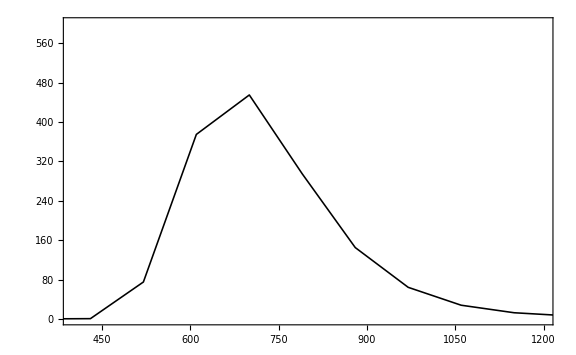

```mathematica
ListLinePlot[{#1,#2}&@@@(Cases[Import["acetylannilinepossiblebyproduct2_uvvis.txt","Table"],{_Real,_Real,_Real}]),PlotRange->{{400,1200},{0,600}},Frame->True,PlotStyle->{Black,Thickness[0.002]},ImageSize->Large,Axes->False]
```

```mathematica
Export["/Users/Apple/Documents/GitHub/LaTeX-Files/基础化学实验报告/figures/byproductuv.eps",%]
```

/Users/Apple/Documents/GitHub/LaTeX-Files/基础化学实验报告/figures/byproductuv.eps

```mathematica
{#1,#2}&@@@(Cases[Import["acetylannilinepossiblebyproduct2_uvvis.txt","Table"],{_Real,_Real,_Real}])
```

{{-20000.,28.7821},{-19910.,28.7554},{-19820.,28.7285},{-19730.,28.7014},{-19640.,28.6739},{-19550.,28.6463},{-19460.,28.6184},{-19370.,28.5902},{-19280.,28.5617},{-19190.,28.533},{-19100.,28.504},{-19010.,28.4747},{-18920.,28.4452},{-18830.,28.4153},{-18740.,28.3852},{-18650.,28.3548},{-18560.,28.3241},{-18470.,28.293},{-18380.,28.2617},{-18290.,28.23},{-18200.,28.1981},{-18110.,28.1658},{-18020.,28.1332},{-17930.,28.1002},{-17840.,28.067},{-17750.,28.0333},{-17660.,27.9994},{-17570.,27.9651},{-17480.,27.9304},{-17390.,27.8954},{-17300.,27.86},{-17210.,27.8242},{-17120.,27.788},{-17030.,27.7515},{-16940.,27.7146},{-16850.,27.6772},{-16760.,27.6395},{-16670.,27.6014},{-16580.,27.5628},{-16490.,27.5238},{-16400.,27.4844},{-16310.,27.4446},{-16220.,27.4043},{-16130.,27.3635},{-16040.,27.3223},{-15950.,27.2807},{-15860.,27.2385},{-15770.,27.1959},{-15680.,27.1528},{-15590.,27.1092},{-15500.,27.0651},{-15410.,27.0204},{-15320.,26.9753},{-15230.,26.9296},{-15140.,26.8833},{-15050.,26.8366},{-14960.,26.7892},{-14870.,26.7413},{-14780.,26.6928},{-14690.,26.6437},{-14600.,26.594},{-14510.,26.5437},{-14420.,26.4927},{-14330.,26.4412},{-14240.,26.389},{-14150.,26.3361},{-14060.,26.2825},{-13970.,26.2283},{-13880.,26.1734},{-13790.,26.1177},{-13700.,26.0614},{-13610.,26.0043},{-13520.,25.9464},{-13430.,25.8878},{-13340.,25.8284},{-13250.,25.7682},{-13160.,25.7072},{-13070.,25.6454},{-12980.,25.5827},{-12890.,25.5191},{-12800.,25.4547},{-12710.,25.3894},{-12620.,25.3232},{-12530.,25.2561},{-12440.,25.188},{-12350.,25.1189},{-12260.,25.0488},{-12170.,24.9778},{-12080.,24.9057},{-11990.,24.8325},{-11900.,24.7583},{-11810.,24.683},{-11720.,24.6065},{-11630.,24.5289},{-11540.,24.4502},{-11450.,24.3702},{-11360.,24.289},{-11270.,24.2066},{-11180.,24.1229},{-11090.,24.0379},{-11000.,23.9516},{-10910.,23.8639},{-10820.,23.7748},{-10730.,23.6843},{-10640.,23.5923},{-10550.,23.4989},{-10460.,23.4039},{-10370.,23.3073},{-10280.,23.2092},{-10190.,23.1094},{-10100.,23.008},{-10010.,22.9048},{-9920.,22.7999},{-9830.,22.6932},{-9740.,22.5846},{-9650.,22.4742},{-9560.,22.3618},{-9470.,22.2475},{-9380.,22.1311},{-9290.,22.0127},{-9200.,21.8921},{-9110.,21.7694},{-9020.,21.6444},{-8930.,21.5171},{-8840.,21.3875},{-8750.,21.2555},{-8660.,21.121},{-8570.,20.9839},{-8480.,20.8443},{-8390.,20.702},{-8300.,20.5569},{-8210.,20.4091},{-8120.,20.2584},{-8030.,20.1047},{-7940.,19.948},{-7850.,19.7882},{-7760.,19.6251},{-7670.,19.4588},{-7580.,19.2892},{-7490.,19.116},{-7400.,18.9394},{-7310.,18.759},{-7220.,18.575},{-7130.,18.3871},{-7040.,18.1952},{-6950.,17.9994},{-6860.,17.7993},{-6770.,17.595},{-6680.,17.3864},{-6590.,17.1732},{-6500.,16.9555},{-6410.,16.733},{-6320.,16.5057},{-6230.,16.2735},{-6140.,16.0361},{-6050.,15.7936},{-5960.,15.5457},{-5870.,15.2924},{-5780.,15.0336},{-5690.,14.769},{-5600.,14.4986},{-5510.,14.2223},{-5420.,13.94},{-5330.,13.6515},{-5240.,13.3568},{-5150.,13.0557},{-5060.,12.7482},{-4970.,12.4341},{-4880.,12.1135},{-4790.,11.7863},{-4700.,11.4525},{-4610.,11.112},{-4520.,10.7649},{-4430.,10.4113},{-4340.,10.0512},{-4250.,9.68471},{-4160.,9.31208},{-4070.,8.93352},{-3980.,8.54931},{-3890.,8.15982},{-3800.,7.76547},{-3710.,7.36681},{-3620.,6.96446},{-3530.,6.55915},{-3440.,6.15173},{-3350.,5.74322},{-3260.,5.33474},{-3170.,4.92761},{-3080.,4.52329},{-2990.,4.12344},{-2900.,3.7299},{-2810.,3.3447},{-2720.,2.97004},{-2630.,2.6083},{-2540.,2.262},{-2450.,1.93372},{-2360.,1.62612},{-2270.,1.34176},{-2180.,1.08305},{-2090.,0.852091},{-2000.,0.650485},{-1910.,0.479188},{-1820.,0.338302},{-1730.,0.22692},{-1640.,0.143029},{-1550.,0.0835177},{-1460.,0.0443457},{-1370.,0.0208875},{-1280.,0.00843941},{-1190.,0.00279243},{-1100.,0.000708557},{-1010.,0.000125311},{-920.,0.0000133816},{-830.,6.898×10^-7},{-740.,1.19×10^-8},{-650.,0.},{-560.,0.},{-470.,0.},{-380.,0.},{-290.,0.},{-200.,0.},{-110.,0.},{-20.,0.},{70.,0.},{160.,0.},{250.,0.},{340.,6.869×10^-7},{430.,0.538571},{520.,75.0212},{610.,374.939},{700.,455.094},{790.,294.707},{880.,145.021},{970.,64.1889},{1060.,27.8441},{1150.,12.546},{1240.,6.38438},{1330.,4.23873},{1420.,3.99638},{1510.,4.76164},{1600.,6.11961},{1690.,7.84848},{1780.,9.80941},{1870.,11.9045},{1960.,14.0607},{2050.,16.2222},{2140.,18.3473},{2230.,20.4056},{2320.,22.3759},{2410.,24.2442},{2500.,26.0024},{2590.,27.6469},{2680.,29.1773},{2770.,30.5955},{2860.,31.9053},{2950.,33.1115},{3040.,34.2196},{3130.,35.2355},{3220.,36.1652},{3310.,37.0148},{3400.,37.79},{3490.,38.4965},{3580.,39.1396},{3670.,39.7244},{3760.,40.2556},{3850.,40.7375},{3940.,41.1743},{4030.,41.5697},{4120.,41.9271},{4210.,42.2498},{4300.,42.5407},{4390.,42.8024},{4480.,43.0374},{4570.,43.248},{4660.,43.4363},{4750.,43.604},{4840.,43.753},{4930.,43.8848},{5020.,44.0008},{5110.,44.1024},{5200.,44.1909},{5290.,44.2672},{5380.,44.3324},{5470.,44.3874},{5560.,44.4331},{5650.,44.4703},{5740.,44.4997},{5830.,44.5218},{5920.,44.5374},{6010.,44.547},{6100.,44.5511},{6190.,44.5501},{6280.,44.5445},{6370.,44.5346},{6460.,44.5209},{6550.,44.5036},{6640.,44.4831},{6730.,44.4596},{6820.,44.4334},{6910.,44.4048},{7000.,44.3739},{7090.,44.341},{7180.,44.3063},{7270.,44.2699},{7360.,44.2319},{7450.,44.1926},{7540.,44.1521},{7630.,44.1105},{7720.,44.0678},{7810.,44.0243},{7900.,43.98},{7990.,43.935},{8080.,43.8894},{8170.,43.8432},{8260.,43.7966},{8350.,43.7496},{8440.,43.7023},{8530.,43.6547},{8620.,43.6068},{8710.,43.5588},{8800.,43.5107},{8890.,43.4625},{8980.,43.4142},{9070.,43.3659},{9160.,43.3176},{9250.,43.2693},{9340.,43.2212},{9430.,43.1731},{9520.,43.1251},{9610.,43.0773},{9700.,43.0297},{9790.,42.9822},{9880.,42.9349},{9970.,42.8878},{10060.,42.841},{10150.,42.7944},{10240.,42.748},{10330.,42.7019},{10420.,42.6561},{10510.,42.6105},{10600.,42.5652},{10690.,42.5202},{10780.,42.4755},{10870.,42.4311},{10960.,42.387},{11050.,42.3432},{11140.,42.2998},{11230.,42.2566},{11320.,42.2138},{11410.,42.1713},{11500.,42.1291},{11590.,42.0872},{11680.,42.0457},{11770.,42.0045},{11860.,41.9636},{11950.,41.923},{12040.,41.8828},{12130.,41.8429},{12220.,41.8033},{12310.,41.7641},{12400.,41.7252},{12490.,41.6866},{12580.,41.6483},{12670.,41.6103},{12760.,41.5727},{12850.,41.5354},{12940.,41.4984},{13030.,41.4617},{13120.,41.4253},{13210.,41.3893},{13300.,41.3535},{13390.,41.3181},{13480.,41.2829},{13570.,41.2481},{13660.,41.2135},{13750.,41.1793},{13840.,41.1454},{13930.,41.1117},{14020.,41.0783},{14110.,41.0453},{14200.,41.0125},{14290.,40.98},{14380.,40.9477},{14470.,40.9158},{14560.,40.8841},{14650.,40.8527},{14740.,40.8216},{14830.,40.7907},{14920.,40.7601},{15010.,40.7298},{15100.,40.6997},{15190.,40.6699},{15280.,40.6403},{15370.,40.611},{15460.,40.5819},{15550.,40.5531},{15640.,40.5245},{15730.,40.4962},{15820.,40.4681},{15910.,40.4403},{16000.,40.4126},{16090.,40.3853},{16180.,40.3581},{16270.,40.3312},{16360.,40.3045},{16450.,40.278},{16540.,40.2517},{16630.,40.2257},{16720.,40.1998},{16810.,40.1742},{16900.,40.1488},{16990.,40.1236},{17080.,40.0986},{17170.,40.0739},{17260.,40.0493},{17350.,40.0249},{17440.,40.0007},{17530.,39.9767},{17620.,39.9529},{17710.,39.9293},{17800.,39.9059},{17890.,39.8827},{17980.,39.8596},{18070.,39.8368},{18160.,39.8141},{18250.,39.7916},{18340.,39.7693},{18430.,39.7471},{18520.,39.7252},{18610.,39.7034},{18700.,39.6817},{18790.,39.6603},{18880.,39.639},{18970.,39.6179},{19060.,39.5969},{19150.,39.5761},{19240.,39.5555},{19330.,39.535},{19420.,39.5147},{19510.,39.4945},{19600.,39.4745},{19690.,39.4546},{19780.,39.4349},{19870.,39.4153},{19960.,39.3959},{20050.,39.3766},{20140.,39.3575},{20230.,39.3385},{20320.,39.3196},{20410.,39.3009},{20500.,39.2824},{20590.,39.2639},{20680.,39.2456},{20770.,39.2275},{20860.,39.2094},{20950.,39.1915},{21040.,39.1738},{21130.,39.1561},{21220.,39.1386},{21310.,39.1212},{21400.,39.1039},{21490.,39.0868},{21580.,39.0698},{21670.,39.0529},{21760.,39.0361},{21850.,39.0194},{21940.,39.0029},{22030.,38.9864},{22120.,38.9701},{22210.,38.9539},{22300.,38.9378},{22390.,38.9219},{22480.,38.906},{22570.,38.8902},{22660.,38.8746},{22750.,38.859},{22840.,38.8436},{22930.,38.8283},{23020.,38.8131},{23110.,38.7979},{23200.,38.7829},{23290.,38.768},{23380.,38.7532},{23470.,38.7384},{23560.,38.7238},{23650.,38.7093},{23740.,38.6949},{23830.,38.6805},{23920.,38.6663},{24010.,38.6521},{24100.,38.6381},{24190.,38.6241},{24280.,38.6103},{24370.,38.5965},{24460.,38.5828},{24550.,38.5692},{24640.,38.5557},{24730.,38.5422},{24820.,38.5289},{24910.,38.5156}}

```mathematica
"/Users/Apple/Documents/NMR.eps"~Export~-Graphics-
```

/Users/Apple/Documents/NMR.eps

```mathematica
Solve[xA*Exp[-HA/(R T)]/Exp[-HA/(R TA)]+xB*Exp[-HB/(R T)]/Exp[-HB/(R TB)]/.R->8.314==1,T]
```

Solve::naqs: ⅇ^(-HA/(False T)+HA/(False TA)) xA+ⅇ^(-HB/(False T)+HB/(False TB)) xB is not a quantified system of equations and inequalities.

Solve[ⅇ^(-HA/(False T)+HA/(False TA)) xA+ⅇ^(-HB/(False T)+HB/(False TB)) xB,T]

```mathematica
Solve[[(xA*Exp[-HA/(R T)]/Exp[-HA/(R TA)]+xB*Exp[-HB/(R T)]/Exp[-HB/(R TB)]/.R->8.314),T]
```

Reduce::naqs: ⅇ^(-(0.120279 HA)/T+(0.120279 HA)/TA) xA+ⅇ^(-(0.120279 HB)/T+(0.120279 HB)/TB) xB is not a quantified system of equations and inequalities.

Reduce[ⅇ^(-(0.120279 HA)/T+(0.120279 HA)/TA) xA+ⅇ^(-(0.120279 HB)/T+(0.120279 HB)/TB) xB,T]

```mathematica
DSolve[D[c[x,t],t]==R*D[D[c[x,t],x],x],c,{x,t}]
```

DSolve[c^(0,1)[x,t]==R c^(2,0)[x,t],c,{x,t}]

```mathematica
DSolve[0==R*D[D[c[x,t],x],x],c[x,t],{x,t}]
```

{{c[x,t]→C[1][t]+x C[2][t]}}

```mathematica
1.35/4.32
```

0.3125

```mathematica
model=First[c/.NDSolve[{D[c[x,t],t]==D[c[x,t],x,x],c[0,t]==1,c[x,0]==DiscreteDelta[x],c[20,t]==0},c,{x,0,20},{t,0,100}]];
Animate[Plot[model[x,t],{x,0,20},PlotRange->{{0,20},{0,1}}],{t,0,100}]
```

```mathematica
Export["diffusion.eps",Plot3D[model[x,t],{x,0,20},{t,0,100},AxesLabel->{"x","t","c"}]]
```

diffusion.eps

```mathematica
D[c[x,t],x]/.x->1
```

c^(1,0)[1,t]

```mathematica
function[x_,y_]:=Exp[88/R]*Exp[-x/R/T]+Exp[88/R]*Exp[-y/R/T]==1/.R->8.314;
```

```mathematica
graph=Plot3D[First[Flatten[T/.NSolve[function[a,b],T]]],{a,1000,8000},{b,1000,8000}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

ReplaceAll::reps: {NSolve[ⅇ^(10.5846-127.797 Power[«2»])+ⅇ^(10.5846-120.279 Power[«2»])==1,T]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

ReplaceAll::reps: {NSolve[ⅇ^(10.5846-124.038 Power[«2»])+ⅇ^(10.5846-120.279 Power[«2»])==1,T]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NSolve[ⅇ^(10.5846-122.158 Power[«2»])+ⅇ^(10.5846-120.279 Power[«2»])==1,T]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

```mathematica
-120.27904738994467/((ⅇ^(-1))[0.5/(2.718281828459045[10.584556170315132])])//N
```

-120.279/(ⅇ^(-1)[0.5/(2.71828[10.5846])])

```mathematica
function[1000,1000]
```

2 ⅇ[10.5846] ⅇ[-120.279/T]==1

```mathematica
4000000/(4157 (ⅇ^(-1))[1/(2 ⅇ[10.584556170315132])])
```

962.232/(ⅇ^(-1)[0.5/(2.71828[10.5846])])

```mathematica
Reduce[function[8000,8000]]
```

ⅇ[-962.232/T]≠0&&ⅇ[10.5846]==1/(2 ⅇ[-962.232/T])

```mathematica
function[8000,8000]
```

2 ⅇ[10.5846] ⅇ[-962.232/T]==1

```mathematica
Cases[#,_Real]&/@Flatten/@Table[T/.Solve[function[a,b],T],{a,1000,2000,1000},{b,1000,2000,1000}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{10.6652},{21.3304}}

```mathematica
Plot3D[First@Flatten[T/.Solve[function[a,b],T,Reals]],{a,1000,2000},{b,1000,2000}]//Quiet
```

-Graphics3D-

```mathematica
Solve[function[1000,2000],T]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{T→ConditionalExpression[120.279/((-0.0000253028+3.14159 ⅈ)+(0.+6.28319 ⅈ) C[1]),C[1]∈ℤ]},{T→ConditionalExpression[120.279/(10.5846+(0.+6.28319 ⅈ) C[1]),C[1]∈ℤ]}}

```mathematica
Solve[function[1000,2000],T,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{T→11.3636}}

```mathematica
list=Table[{a,b,First@Flatten[T/.Solve[function[a,b],T,Reals]]},{a,1000,10000,100},{b,1000,10000,100}]//Quiet
```

{{{1000,1000,10.6652},{1000,1100,11.0601},{1000,1200,11.2454},{1000,1300,11.3204},{1000,1400,11.3483},82,{1000,9700,11.3636},{1000,9800,11.3636},{1000,9900,11.3636},{1000,10000,11.3636}},89,{1}}
 |  |  |  |

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/基础化学实验报告/figures"];
```

```mathematica
"Solutionsurface.eps"~Export~ListPointPlot3D[Flatten[%5,1]]
```

Solutionsurface.eps

```mathematica
Directory[]
```

/Users/Apple

```mathematica
"TwPlot.eps"~Export~ListPlot[{#4,#3}&@@@({#1,#2,#3,Exp[88/8.314]*Exp[-#1/(8.314*#3)]}&@@@Flatten[datalist,1]),Axes->False,Frame->True,FrameLabel->{"w","T/^oC"}]
```

TwPlot.eps

```mathematica
"expratio.eps"~Export~ListPlot[Partition[{#4,#3}&@@@(SortBy[{#1,#2,#3,Exp[88/8.314]*Exp[-#1/(8.314*#3)]}&@@@Flatten[datalist,1],Exp[#1[[1]]]/Exp[#1[[2]]]>Exp[#2[[1]]]/Exp[#2[[2]]]&]),91],Frame->True,FrameLabel->{"w","T/^oC"}]//Quiet
```

expratio.eps

```mathematica
8281/91
```

91

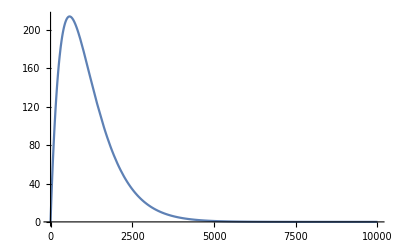

```mathematica
Plot[Exp[-x/8.314/70]x,{x,0,10000}]
```

```mathematica
"wHvap.eps"~Export~ListPointPlot3D[{#1,#2,#4}&@@@({#1,#2,#3,Exp[88/8.314]*Exp[-#1/(8.314*#3)]}&@@@Flatten[datalist,1])]
```

wHvap.eps

```mathematica
0.13/0.23
```

0.565217

```mathematica
SetDirectory["/Users/Apple/Downloads/537刘老师班/原始数据/SDB-10.D"];
```

```mathematica
FileNames[]
```

{acqmeth.txt,cnorm.ini,DATA.MS,GC.ini,PRE_POST.INI,RESULTS.CSV,rteres.txt,runstart.txt,tic_front.csv,tmplibrp.txt}

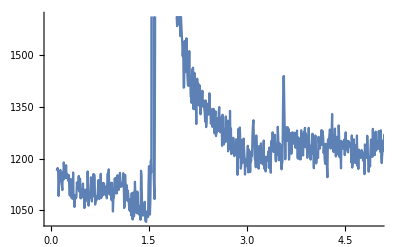

```mathematica
ListLinePlot[Drop[a,2],PlotRange->{{0,5},Automatic}]
```

```mathematica
a=Import["tic_front.csv"]
```

{{E:\Êý.beÝ\2018\0409\CXY\0510\SDB-10.d 21 May 18  10:56 pm},{Start of data points},{0.0947167,1165},{0.101883,1170},{0.109033,1173},{0.1162,1161},{0.123367,1092},{0.130533,1130},3324,{23.9476,1543},{23.9548,1526},{23.962,1550},{23.9691,1534},{23.9763,1516},{23.9835,1513},{23.9906,1509}}
 |  |  |  |

```mathematica
datalist={{{1000,1000,10.665207591278929},{1000,1100,11.060114598744196},{1000,1200,11.245367044454827},{1000,1300,11.320378797258291},{1000,1400,11.348292502110688},{1000,1500,11.358265328192664},{1000,1600,11.36176631764085},{1000,1700,11.362986631441466},{1000,1800,11.36341080162217},{1000,1900,11.363558081179779},{1000,2000,11.363609198442033},{1000,2100,11.36362693731064},{1000,2200,11.363633092752716},{1000,2300,11.363635228664315},{1000,2400,11.363635969810455},{1000,2500,11.363636226982141},{1000,2600,11.363636316218532},{1000,2700,11.363636347182789},{1000,2800,11.363636357927117},{1000,2900,11.363636361655304},{1000,3000,11.363636362948954},{1000,3100,11.363636363397838},{1000,3200,11.363636363553598},{1000,3300,11.363636363607645},{1000,3400,11.363636363626398},{1000,3500,11.363636363632907},{1000,3600,11.363636363635164},{1000,3700,11.363636363635948},{1000,3800,11.36363636363622},{1000,3900,11.363636363636314},{1000,4000,11.363636363636346},{1000,4100,11.363636363636358},{1000,4200,11.363636363636362},{1000,4300,11.363636363636363},{1000,4400,11.363636363636363},{1000,4500,11.363636363636363},{1000,4600,11.363636363636363},{1000,4700,11.363636363636363},{1000,4800,11.363636363636363},{1000,4900,11.363636363636363},{1000,5000,11.363636363636363},{1000,5100,11.363636363636363},{1000,5200,11.363636363636363},{1000,5300,11.363636363636363},{1000,5400,11.363636363636363},{1000,5500,11.363636363636363},{1000,5600,11.363636363636363},{1000,5700,11.363636363636363},{1000,5800,11.363636363636363},{1000,5900,11.363636363636363},{1000,6000,11.363636363636363},{1000,6100,11.363636363636363},{1000,6200,11.363636363636363},{1000,6300,11.363636363636363},{1000,6400,11.363636363636363},{1000,6500,11.363636363636363},{1000,6600,11.363636363636363},{1000,6700,11.363636363636363},{1000,6800,11.363636363636363},{1000,6900,11.363636363636363},{1000,7000,11.363636363636363},{1000,7100,11.363636363636363},{1000,7200,11.363636363636363},{1000,7300,11.363636363636363},{1000,7400,11.363636363636363},{1000,7500,11.363636363636363},{1000,7600,11.363636363636363},{1000,7700,11.363636363636363},{1000,7800,11.363636363636363},{1000,7900,11.363636363636363},{1000,8000,11.363636363636363},{1000,8100,11.363636363636363},{1000,8200,11.363636363636363},{1000,8300,11.363636363636363},{1000,8400,11.363636363636363},{1000,8500,11.363636363636363},{1000,8600,11.363636363636363},{1000,8700,11.363636363636363},{1000,8800,11.363636363636363},{1000,8900,11.363636363636363},{1000,9000,11.363636363636363},{1000,9100,11.363636363636363},{1000,9200,11.363636363636363},{1000,9300,11.363636363636363},{1000,9400,11.363636363636363},{1000,9500,11.363636363636363},{1000,9600,11.363636363636363},{1000,9700,11.363636363636363},{1000,9800,11.363636363636363},{1000,9900,11.363636363636363},{1000,10000,11.363636363636363}},{{1100,1000,11.060114598744196},{1100,1100,11.73172835040682},{1100,1200,12.137958050867898},{1100,1300,12.344666972185676},{1100,1400,12.437141096535946},{1100,1500,12.475342090315225},{1100,1600,12.490469932070873},{1100,1700,12.496341107435612},{1100,1800,12.498599259279876},{1100,1900,12.49946440155278},{1100,2000,12.499795307887311},{1100,2100,12.499921788252509},{1100,2200,12.499970118286237},{1100,2300,12.499988583743063},{1100,2400,12.499995638501286},{1100,2500,12.499998333730515},{1100,2600,12.499999363418938},{1100,2700,12.499999756801005},{1100,2800,12.499999907088457},{1100,2900,12.499999964504156},{1100,3000,12.4999999864392},{1100,3100,12.499999994819245},{1100,3200,12.49999999802075},{1100,3300,12.49999999924385},{1100,3400,12.49999999971112},{1100,3500,12.499999999889637},{1100,3600,12.499999999957836},{1100,3700,12.499999999983892},{1100,3800,12.499999999993847},{1100,3900,12.499999999997648},{1100,4000,12.499999999999101},{1100,4100,12.499999999999657},{1100,4200,12.499999999999869},{1100,4300,12.49999999999995},{1100,4400,12.49999999999998},{1100,4500,12.499999999999993},{1100,4600,12.499999999999996},{1100,4700,12.499999999999998},{1100,4800,12.5},{1100,4900,12.5},{1100,5000,12.5},{1100,5100,12.5},{1100,5200,12.5},{1100,5300,12.5},{1100,5400,12.5},{1100,5500,12.5},{1100,5600,12.5},{1100,5700,12.5},{1100,5800,12.5},{1100,5900,12.5},{1100,6000,12.5},{1100,6100,12.5},{1100,6200,12.5},{1100,6300,12.5},{1100,6400,12.5},{1100,6500,12.5},{1100,6600,12.5},{1100,6700,12.5},{1100,6800,12.5},{1100,6900,12.5},{1100,7000,12.5},{1100,7100,12.5},{1100,7200,12.5},{1100,7300,12.5},{1100,7400,12.5},{1100,7500,12.5},{1100,7600,12.5},{1100,7700,12.5},{1100,7800,12.5},{1100,7900,12.5},{1100,8000,12.5},{1100,8100,12.5},{1100,8200,12.5},{1100,8300,12.5},{1100,8400,12.5},{1100,8500,12.5},{1100,8600,12.5},{1100,8700,12.5},{1100,8800,12.5},{1100,8900,12.5},{1100,9000,12.5},{1100,9100,12.5},{1100,9200,12.5},{1100,9300,12.5},{1100,9400,12.5},{1100,9500,12.5},{1100,9600,12.5},{1100,9700,12.5},{1100,9800,12.5},{1100,9900,12.5},{1100,10000,12.5}},{{1200,1000,11.245367044454827},{1200,1100,12.137958050867898},{1200,1200,12.798249109534714},{1200,1300,13.214133412953014},{1200,1400,13.440272838395755},{1200,1500,13.550060944288052},{1200,1600,13.599534531816317},{1200,1700,13.62089662992476},{1200,1800,13.629918393831197},{1200,1900,13.63368762391097},{1200,2000,13.635254432376108},{1200,2100,13.635904219491174},{1200,2200,13.63617341655099},{1200,2300,13.636284888400326},{1200,2400,13.63633103813044},{1200,2500,13.636350142507046},{1200,2600,13.636358050728742},{1200,2700,13.636361324263914},{1200,2800,13.636362679302865},{1200,2900,13.636363240202373},{1200,3000,13.636363472378571},{1200,3100,13.63636356848447},{1200,3200,13.636363608266072},{1200,3300,13.636363624733072},{1200,3400,13.636363631549338},{1200,3500,13.63636363437083},{1200,3600,13.636363635538745},{1200,3700,13.636363636022185},{1200,3800,13.636363636222297},{1200,3900,13.63636363630513},{1200,4000,13.63636363633942},{1200,4100,13.636363636353613},{1200,4200,13.636363636359487},{1200,4300,13.636363636361919},{1200,4400,13.636363636362926},{1200,4500,13.636363636363342},{1200,4600,13.636363636363514},{1200,4700,13.636363636363585},{1200,4800,13.636363636363615},{1200,4900,13.636363636363628},{1200,5000,13.636363636363633},{1200,5100,13.636363636363635},{1200,5200,13.636363636363635},{1200,5300,13.636363636363637},{1200,5400,13.636363636363637},{1200,5500,13.636363636363637},{1200,5600,13.636363636363637},{1200,5700,13.636363636363637},{1200,5800,13.636363636363637},{1200,5900,13.636363636363637},{1200,6000,13.636363636363637},{1200,6100,13.636363636363637},{1200,6200,13.636363636363637},{1200,6300,13.636363636363637},{1200,6400,13.636363636363637},{1200,6500,13.636363636363637},{1200,6600,13.636363636363637},{1200,6700,13.636363636363637},{1200,6800,13.636363636363637},{1200,6900,13.636363636363637},{1200,7000,13.636363636363637},{1200,7100,13.636363636363637},{1200,7200,13.636363636363637},{1200,7300,13.636363636363637},{1200,7400,13.636363636363637},{1200,7500,13.636363636363637},{1200,7600,13.636363636363637},{1200,7700,13.636363636363637},{1200,7800,13.636363636363637},{1200,7900,13.636363636363637},{1200,8000,13.636363636363637},{1200,8100,13.636363636363637},{1200,8200,13.636363636363637},{1200,8300,13.636363636363637},{1200,8400,13.636363636363637},{1200,8500,13.636363636363637},{1200,8600,13.636363636363637},{1200,8700,13.636363636363637},{1200,8800,13.636363636363637},{1200,8900,13.636363636363637},{1200,9000,13.636363636363637},{1200,9100,13.636363636363637},{1200,9200,13.636363636363637},{1200,9300,13.636363636363637},{1200,9400,13.636363636363637},{1200,9500,13.636363636363637},{1200,9600,13.636363636363637},{1200,9700,13.636363636363637},{1200,9800,13.636363636363637},{1200,9900,13.636363636363637},{1200,10000,13.636363636363637}},{{1300,1000,11.320378797258291},{1300,1100,12.344666972185676},{1300,1200,13.214133412953014},{1300,1300,13.864769868662608},{1300,1400,14.288975335653218},{1300,1500,14.532692087489009},{1300,1600,14.659347330312572},{1300,1700,14.720761041632981},{1300,1800,14.749304911043696},{1300,1900,14.762262271808925},{1300,2000,14.76807207119546},{1300,2100,14.77066093576899},{1300,2200,14.771811028606432},{1300,2300,14.77232119919991},{1300,2400,14.772547346183671},{1300,2500,14.7726475582596},{1300,2600,14.772691957974644},{1300,2700,14.772711628127745},{1300,2800,14.77272034217707},{1300,2900,14.772724202513345},{1300,3000,14.772725912634687},{1300,3100,14.772726670212355},{1300,3200,14.772727005816009},{1300,3300,14.772727154486873},{1300,3400,14.772727220347353},{1300,3500,14.772727249523225},{1300,3600,14.772727262447994},{1300,3700,14.772727268173602},{1300,3800,14.77272727071002},{1300,3900,14.77272727183364},{1300,4000,14.772727272331398},{1300,4100,14.772727272551903},{1300,4200,14.772727272649584},{1300,4300,14.772727272692856},{1300,4400,14.772727272712027},{1300,4500,14.77272727272052},{1300,4600,14.77272727272428},{1300,4700,14.772727272725946},{1300,4800,14.772727272726685},{1300,4900,14.772727272727012},{1300,5000,14.772727272727158},{1300,5100,14.772727272727222},{1300,5200,14.77272727272725},{1300,5300,14.772727272727263},{1300,5400,14.772727272727268},{1300,5500,14.772727272727272},{1300,5600,14.772727272727272},{1300,5700,14.772727272727272},{1300,5800,14.772727272727273},{1300,5900,14.772727272727273},{1300,6000,14.772727272727273},{1300,6100,14.772727272727273},{1300,6200,14.772727272727273},{1300,6300,14.772727272727273},{1300,6400,14.772727272727273},{1300,6500,14.772727272727273},{1300,6600,14.772727272727273},{1300,6700,14.772727272727273},{1300,6800,14.772727272727273},{1300,6900,14.772727272727273},{1300,7000,14.772727272727273},{1300,7100,14.772727272727273},{1300,7200,14.772727272727273},{1300,7300,14.772727272727273},{1300,7400,14.772727272727273},{1300,7500,14.772727272727273},{1300,7600,14.772727272727273},{1300,7700,14.772727272727273},{1300,7800,14.772727272727273},{1300,7900,14.772727272727273},{1300,8000,14.772727272727273},{1300,8100,14.772727272727273},{1300,8200,14.772727272727273},{1300,8300,14.772727272727273},{1300,8400,14.772727272727273},{1300,8500,14.772727272727273},{1300,8600,14.772727272727273},{1300,8700,14.772727272727273},{1300,8800,14.772727272727273},{1300,8900,14.772727272727273},{1300,9000,14.772727272727273},{1300,9100,14.772727272727273},{1300,9200,14.772727272727273},{1300,9300,14.772727272727273},{1300,9400,14.772727272727273},{1300,9500,14.772727272727273},{1300,9600,14.772727272727273},{1300,9700,14.772727272727273},{1300,9800,14.772727272727273},{1300,9900,14.772727272727273},{1300,10000,14.772727272727273}},{{1400,1000,11.348292502110688},{1400,1100,12.437141096535946},{1400,1200,13.440272838395755},{1400,1300,14.288975335653218},{1400,1400,14.9312906277905},{1400,1500,15.362736708995785},{1400,1600,15.622364857921923},{1400,1700,15.7652538178009},{1400,1800,15.839000729623688},{1400,1900,15.875517592536626},{1400,2000,15.893161701416243},{1400,2100,15.901571459469729},{1400,2200,15.905550701887284},{1400,2300,15.907426413651214},{1400,2400,15.908308852574304},{1400,2500,15.908723589977432},{1400,2600,15.908918415173618},{1400,2700,15.909009912524265},{1400,2800,15.909052877818846},{1400,2900,15.909073052197895},{1400,3000,15.909082524798777},{1400,3100,15.909086972460235},{1400,3200,15.909089060750986},{1400,3300,15.909090041253279},{1400,3400,15.909090501621652},{1400,3500,15.909090717775},{1400,3600,15.909090819263833},{1400,3700,15.9090908669151},{1400,3800,15.90909088928843},{1400,3900,15.909090899793206},{1400,4000,15.909090904725431},{1400,4100,15.90909090704122},{1400,4200,15.909090908128535},{1400,4300,15.909090908639053},{1400,4400,15.909090908878753},{1400,4500,15.909090908991297},{1400,4600,15.909090909044139},{1400,4700,15.909090909068949},{1400,4800,15.909090909080598},{1400,4900,15.909090909086068},{1400,5000,15.909090909088636},{1400,5100,15.909090909089842},{1400,5200,15.909090909090407},{1400,5300,15.909090909090674},{1400,5400,15.909090909090798},{1400,5500,15.909090909090857},{1400,5600,15.909090909090885},{1400,5700,15.909090909090898},{1400,5800,15.909090909090903},{1400,5900,15.909090909090907},{1400,6000,15.909090909090908},{1400,6100,15.909090909090908},{1400,6200,15.909090909090908},{1400,6300,15.909090909090908},{1400,6400,15.909090909090908},{1400,6500,15.909090909090908},{1400,6600,15.909090909090908},{1400,6700,15.909090909090908},{1400,6800,15.909090909090908},{1400,6900,15.909090909090908},{1400,7000,15.909090909090908},{1400,7100,15.909090909090908},{1400,7200,15.909090909090908},{1400,7300,15.909090909090908},{1400,7400,15.909090909090908},{1400,7500,15.909090909090908},{1400,7600,15.909090909090908},{1400,7700,15.909090909090908},{1400,7800,15.909090909090908},{1400,7900,15.909090909090908},{1400,8000,15.909090909090908},{1400,8100,15.909090909090908},{1400,8200,15.909090909090908},{1400,8300,15.909090909090908},{1400,8400,15.909090909090908},{1400,8500,15.909090909090908},{1400,8600,15.909090909090908},{1400,8700,15.909090909090908},{1400,8800,15.909090909090908},{1400,8900,15.909090909090908},{1400,9000,15.909090909090908},{1400,9100,15.909090909090908},{1400,9200,15.909090909090908},{1400,9300,15.909090909090908},{1400,9400,15.909090909090908},{1400,9500,15.909090909090908},{1400,9600,15.909090909090908},{1400,9700,15.909090909090908},{1400,9800,15.909090909090908},{1400,9900,15.909090909090908},{1400,10000,15.909090909090908}},{{1500,1000,11.358265328192664},{1500,1100,12.475342090315225},{1500,1200,13.550060944288052},{1500,1300,14.532692087489009},{1500,1400,15.362736708995785},{1500,1500,15.997811386918393},{1500,1600,16.435611557203227},{1500,1700,16.70966730557993},{1500,1800,16.86805056668224},{1500,1900,16.95429896330561},{1500,2000,16.999418164770397},{1500,2100,17.022438753166032},{1500,2200,17.03401315720103},{1500,2300,17.039784632963272},{1500,2400,17.042649476461275},{1500,2500,17.044068040470137},{1500,2600,17.044769540911368},{1500,2700,17.045116202433253},{1500,2800,17.045287450117},{1500,2900,17.045372028747728},{1500,3000,17.04541379766305},{1500,3100,17.045434424049958},{1500,3200,17.045444609527625},{1500,3300,17.04544963912907},{1500,3400,17.04545212273455},{1500,3500,17.04545334912858},{1500,3600,17.045453954715683},{1500,3700,17.0454542537512},{1500,3800,17.04545440141319},{1500,3900,17.045454474327798},{1500,4000,17.04545451033259},{1500,4100,17.045454528111538},{1500,4200,17.045454536890674},{1500,4300,17.04545454122576},{1500,4400,17.045454543366397},{1500,4500,17.04545454442343},{1500,4600,17.045454544945386},{1500,4700,17.045454545203125},{1500,4800,17.045454545330397},{1500,4900,17.04545454539324},{1500,5000,17.045454545424274},{1500,5100,17.045454545439597},{1500,5200,17.045454545447164},{1500,5300,17.0454545454509},{1500,5400,17.045454545452746},{1500,5500,17.045454545453655},{1500,5600,17.045454545454106},{1500,5700,17.04545454545433},{1500,5800,17.04545454545444},{1500,5900,17.045454545454493},{1500,6000,17.04545454545452},{1500,6100,17.045454545454533},{1500,6200,17.04545454545454},{1500,6300,17.045454545454543},{1500,6400,17.045454545454543},{1500,6500,17.045454545454543},{1500,6600,17.045454545454547},{1500,6700,17.045454545454547},{1500,6800,17.045454545454547},{1500,6900,17.045454545454547},{1500,7000,17.045454545454547},{1500,7100,17.045454545454547},{1500,7200,17.045454545454547},{1500,7300,17.045454545454547},{1500,7400,17.045454545454547},{1500,7500,17.045454545454547},{1500,7600,17.045454545454547},{1500,7700,17.045454545454547},{1500,7800,17.045454545454547},{1500,7900,17.045454545454547},{1500,8000,17.045454545454547},{1500,8100,17.045454545454547},{1500,8200,17.045454545454547},{1500,8300,17.045454545454547},{1500,8400,17.045454545454547},{1500,8500,17.045454545454547},{1500,8600,17.045454545454547},{1500,8700,17.045454545454547},{1500,8800,17.045454545454547},{1500,8900,17.045454545454547},{1500,9000,17.045454545454547},{1500,9100,17.045454545454547},{1500,9200,17.045454545454547},{1500,9300,17.045454545454547},{1500,9400,17.045454545454547},{1500,9500,17.045454545454547},{1500,9600,17.045454545454547},{1500,9700,17.045454545454547},{1500,9800,17.045454545454547},{1500,9900,17.045454545454547},{1500,10000,17.045454545454547}},{{1600,1000,11.36176631764085},{1600,1100,12.490469932070873},{1600,1200,13.599534531816317},{1600,1300,14.659347330312572},{1600,1400,15.622364857921923},{1600,1500,16.435611557203227},{1600,1600,17.064332146046286},{1600,1700,17.507750867384143},{1600,1800,17.794918586111617},{1600,1900,17.96800661324001},{1600,2000,18.0667479257174},{1600,2100,18.120943880555398},{1600,2200,18.149952050050793},{1600,2300,18.165240354219133},{1600,2400,18.17322452510826},{1600,2500,18.17737232269065},{1600,2600,18.179520725617433},{1600,2700,18.180631675096578},{1600,2800,18.181205625988234},{1600,2900,18.181501997349198},{1600,3000,18.18165499259171},{1600,3100,18.18173396116684},{1600,3200,18.181774717507253},{1600,3300,18.18179575126277},{1600,3400,18.18180660621859},{1600,3500,18.181812208097107},{1600,3600,18.18181509901855},{1600,3700,18.181816590910156},{1600,3800,18.18181736081558},{1600,3900,18.18181775813246},{1600,4000,18.181817963171426},{1600,4100,18.181818068983606},{1600,4200,18.181818123588915},{1600,4300,18.18181815176846},{1600,4400,18.181818166310762},{1600,4500,18.181818173815444},{1600,4600,18.1818181776883},{1600,4700,18.18181817968692},{1600,4800,18.181818180718324},{1600,4900,18.18181818125059},{1600,5000,18.181818181525273},{1600,5100,18.181818181667023},{1600,5200,18.181818181740176},{1600,5300,18.181818181777924},{1600,5400,18.181818181797407},{1600,5500,18.18181818180746},{1600,5600,18.18181818181265},{1600,5700,18.181818181815327},{1600,5800,18.18181818181671},{1600,5900,18.181818181817423},{1600,6000,18.18181818181779},{1600,6100,18.18181818181798},{1600,6200,18.181818181818077},{1600,6300,18.181818181818127},{1600,6400,18.181818181818155},{1600,6500,18.18181818181817},{1600,6600,18.181818181818173},{1600,6700,18.181818181818176},{1600,6800,18.18181818181818},{1600,6900,18.18181818181818},{1600,7000,18.18181818181818},{1600,7100,18.18181818181818},{1600,7200,18.181818181818183},{1600,7300,18.181818181818183},{1600,7400,18.181818181818183},{1600,7500,18.181818181818183},{1600,7600,18.181818181818183},{1600,7700,18.181818181818183},{1600,7800,18.181818181818183},{1600,7900,18.181818181818183},{1600,8000,18.181818181818183},{1600,8100,18.181818181818183},{1600,8200,18.181818181818183},{1600,8300,18.181818181818183},{1600,8400,18.181818181818183},{1600,8500,18.181818181818183},{1600,8600,18.181818181818183},{1600,8700,18.181818181818183},{1600,8800,18.181818181818183},{1600,8900,18.181818181818183},{1600,9000,18.181818181818183},{1600,9100,18.181818181818183},{1600,9200,18.181818181818183},{1600,9300,18.181818181818183},{1600,9400,18.181818181818183},{1600,9500,18.181818181818183},{1600,9600,18.181818181818183},{1600,9700,18.181818181818183},{1600,9800,18.181818181818183},{1600,9900,18.181818181818183},{1600,10000,18.181818181818183}},{{1700,1000,11.362986631441466},{1700,1100,12.496341107435612},{1700,1200,13.62089662992476},{1700,1300,14.720761041632981},{1700,1400,15.7652538178009},{1700,1500,16.70966730557993},{1700,1600,17.507750867384143},{1700,1700,18.130852905174176},{1700,1800,18.579273686778368},{1700,1900,18.87838875028195},{1700,2000,19.0653794141137},{1700,2100,19.176470615283353},{1700,2200,19.240077015632636},{1700,2300,19.275596679921424},{1700,2400,19.295116691931067},{1700,2500,19.30573866261011},{1700,2600,19.311484605124086},{1700,2700,19.314582072362782},{1700,2800,19.316248456631747},{1700,2900,19.317143901965515},{1700,3000,19.317624757558512},{1700,3100,19.317882880322543},{1700,3200,19.318021410716774},{1700,3300,19.318095748806392},{1700,3400,19.318135637351457},{1700,3500,19.318157040043797},{1700,3600,19.318168523677297},{1700,3700,19.3181746851572},{1700,3800,19.318177991042965},{1700,3900,19.318179764779163},{1700,4000,19.31818071645559},{1700,4100,19.31818122706533},{1700,4200,19.31818150102624},{1700,4300,19.318181648016292},{1700,4400,19.318181726881818},{1700,4500,19.318181769196045},{1700,4600,19.31818179189917},{1700,4700,19.318181804080222},{1700,4800,19.318181810615798},{1700,4900,19.318181814122372},{1700,5000,19.31818181600378},{1700,5100,19.318181817013222},{1700,5200,19.318181817554823},{1700,5300,19.318181817845414},{1700,5400,19.318181818001325},{1700,5500,19.318181818084977},{1700,5600,19.318181818129858},{1700,5700,19.318181818153942},{1700,5800,19.31818181816686},{1700,5900,19.318181818173795},{1700,6000,19.31818181817751},{1700,6100,19.318181818179507},{1700,6200,19.31818181818058},{1700,6300,19.318181818181152},{1700,6400,19.31818181818146},{1700,6500,19.31818181818163},{1700,6600,19.318181818181717},{1700,6700,19.318181818181763},{1700,6800,19.318181818181788},{1700,6900,19.318181818181802},{1700,7000,19.31818181818181},{1700,7100,19.318181818181813},{1700,7200,19.318181818181817},{1700,7300,19.318181818181817},{1700,7400,19.318181818181817},{1700,7500,19.318181818181817},{1700,7600,19.318181818181817},{1700,7700,19.318181818181817},{1700,7800,19.318181818181817},{1700,7900,19.318181818181817},{1700,8000,19.318181818181817},{1700,8100,19.318181818181817},{1700,8200,19.318181818181817},{1700,8300,19.318181818181817},{1700,8400,19.318181818181817},{1700,8500,19.318181818181817},{1700,8600,19.318181818181817},{1700,8700,19.318181818181817},{1700,8800,19.318181818181817},{1700,8900,19.318181818181817},{1700,9000,19.318181818181817},{1700,9100,19.318181818181817},{1700,9200,19.318181818181817},{1700,9300,19.318181818181817},{1700,9400,19.318181818181817},{1700,9500,19.318181818181817},{1700,9600,19.318181818181817},{1700,9700,19.318181818181817},{1700,9800,19.318181818181817},{1700,9900,19.318181818181817},{1700,10000,19.318181818181817}},{{1800,1000,11.36341080162217},{1800,1100,12.498599259279876},{1800,1200,13.629918393831197},{1800,1300,14.749304911043696},{1800,1400,15.839000729623688},{1800,1500,16.86805056668224},{1800,1600,17.794918586111617},{1800,1700,18.579273686778368},{1800,1800,19.19737366430207},{1800,1900,19.65027501822439},{1800,2000,19.96030630031928},{1800,2100,20.16040925759363},{1800,2200,20.283608420592554},{1800,2300,20.35683586861358},{1800,2400,20.399301797724476},{1800,2500,20.423528582215607},{1800,2600,20.437206000062137},{1800,2700,20.444877590746795},{1800,2800,20.449163500595983},{1800,2900,20.45155221323841},{1800,3000,20.452881648564162},{1800,3100,20.45362092217044},{1800,3200,20.454031814668756},{1800,3300,20.454260124826487},{1800,3400,20.454386962614763},{1800,3500,20.45445742043694},{1800,3600,20.45449655719566},{1800,3700,20.454518295519044},{1800,3800,20.454530369733103},{1800,3900,20.45453707609311},{1800,4000,20.454540800971227},{1800,4100,20.45454286985295},{1800,4200,20.454544018954298},{1800,4300,20.454544657189086},{1800,4400,20.454545011677716},{1800,4500,20.454545208567854},{1800,4600,20.454545317924588},{1800,4700,20.454545378663504},{1800,4800,20.45454541239911},{1800,4900,20.454545431136534},{1800,5000,20.454545441543676},{1800,5100,20.45454544732401},{1800,5200,20.454545450534518},{1800,5300,20.454545452317703},{1800,5400,20.454545453308118},{1800,5500,20.454545453858213},{1800,5600,20.454545454163746},{1800,5700,20.454545454333445},{1800,5800,20.454545454427702},{1800,5900,20.45454545448005},{1800,6000,20.45454545450913},{1800,6100,20.454545454525277},{1800,6200,20.454545454534248},{1800,6300,20.45454545453923},{1800,6400,20.454545454541996},{1800,6500,20.454545454543535},{1800,6600,20.454545454544387},{1800,6700,20.454545454544864},{1800,6800,20.454545454545126},{1800,6900,20.454545454545272},{1800,7000,20.454545454545354},{1800,7100,20.454545454545396},{1800,7200,20.454545454545425},{1800,7300,20.454545454545435},{1800,7400,20.454545454545446},{1800,7500,20.45454545454545},{1800,7600,20.454545454545453},{1800,7700,20.454545454545453},{1800,7800,20.454545454545453},{1800,7900,20.454545454545453},{1800,8000,20.454545454545453},{1800,8100,20.454545454545453},{1800,8200,20.454545454545453},{1800,8300,20.454545454545453},{1800,8400,20.454545454545453},{1800,8500,20.454545454545453},{1800,8600,20.454545454545453},{1800,8700,20.454545454545453},{1800,8800,20.454545454545453},{1800,8900,20.454545454545453},{1800,9000,20.454545454545453},{1800,9100,20.454545454545453},{1800,9200,20.454545454545453},{1800,9300,20.454545454545453},{1800,9400,20.454545454545453},{1800,9500,20.454545454545453},{1800,9600,20.454545454545453},{1800,9700,20.454545454545453},{1800,9800,20.454545454545453},{1800,9900,20.454545454545453},{1800,10000,20.454545454545453}},{{1900,1000,11.363558081179779},{1900,1100,12.49946440155278},{1900,1200,13.63368762391097},{1900,1300,14.762262271808925},{1900,1400,15.875517592536626},{1900,1500,16.95429896330561},{1900,1600,17.96800661324001},{1900,1700,18.87838875028195},{1900,1800,19.65027501822439},{1900,1900,20.263894423429964},{1900,2000,20.720831520284975},{1900,2100,21.0408649124407},{1900,2200,21.253316798055035},{1900,2300,21.38831188401941},{1900,2400,21.471266395382308},{1900,2500,21.521026912763773},{1900,2600,21.550385721848993},{1900,2700,21.56751895884114},{1900,2800,21.57744751513085},{1900,2900,21.58317559200062},{1900,3000,21.586471209416782},{1900,3100,21.588364120777687},{1900,3200,21.58945023524322},{1900,3300,21.59007303574235},{1900,3400,21.59043002731825},{1900,3500,21.590634609600308},{1900,3600,21.590751834167875},{1900,3700,21.59081899771991},{1900,3800,21.59085747703986},{1900,3900,21.59087952195434},{1900,4000,21.590892151329996},{1900,4100,21.590899386535042},{1900,4200,21.590903531464384},{1900,4300,21.5909059060172},{1900,4400,21.590907266351334},{1900,4500,21.590908045658733},{1900,4600,21.590908492107552},{1900,4700,21.590908747868575},{1900,4800,21.59090889438858},{1900,4900,21.590908978326738},{1900,5000,21.590909026413097},{1900,5100,21.590909053960733},{1900,5200,21.590909069742175},{1900,5300,21.590909078783024},{1900,5400,21.59090908396233},{1900,5500,21.590909086929443},{1900,5600,21.590909088629235},{1900,5700,21.590909089603013},{1900,5800,21.590909090160867},{1900,5900,21.590909090480448},{1900,6000,21.59090909066353},{1900,6100,21.590909090768417},{1900,6200,21.5909090908285},{1900,6300,21.590909090862922},{1900,6400,21.590909090882644},{1900,6500,21.590909090893938},{1900,6600,21.59090909090041},{1900,6700,21.59090909090412},{1900,6800,21.59090909090624},{1900,6900,21.59090909090746},{1900,7000,21.590909090908156},{1900,7100,21.590909090908557},{1900,7200,21.590909090908784},{1900,7300,21.590909090908916},{1900,7400,21.59090909090899},{1900,7500,21.590909090909033},{1900,7600,21.590909090909058},{1900,7700,21.590909090909072},{1900,7800,21.59090909090908},{1900,7900,21.590909090909086},{1900,8000,21.590909090909086},{1900,8100,21.59090909090909},{1900,8200,21.59090909090909},{1900,8300,21.59090909090909},{1900,8400,21.59090909090909},{1900,8500,21.59090909090909},{1900,8600,21.59090909090909},{1900,8700,21.59090909090909},{1900,8800,21.59090909090909},{1900,8900,21.59090909090909},{1900,9000,21.59090909090909},{1900,9100,21.59090909090909},{1900,9200,21.59090909090909},{1900,9300,21.59090909090909},{1900,9400,21.59090909090909},{1900,9500,21.59090909090909},{1900,9600,21.59090909090909},{1900,9700,21.59090909090909},{1900,9800,21.59090909090909},{1900,9900,21.59090909090909},{1900,10000,21.59090909090909}},{{2000,1000,11.363609198442033},{2000,1100,12.499795307887311},{2000,1200,13.635254432376108},{2000,1300,14.76807207119546},{2000,1400,15.893161701416243},{2000,1500,16.999418164770397},{2000,1600,18.0667479257174},{2000,1700,19.0653794141137},{2000,1800,19.96030630031928},{2000,1900,20.720831520284975},{2000,2000,21.330415182557857},{2000,2100,21.791005680777346},{2000,2200,22.120229197488392},{2000,2300,22.34430251305612},{2000,2400,22.490734088909655},{2000,2500,22.583434907146753},{2000,2600,22.640757594516582},{2000,2700,22.675620312277196},{2000,2800,22.696585004221376},{2000,2900,22.709098142369243},{2000,3000,22.716530656385327},{2000,3100,22.72093171773046},{2000,3200,22.7235326352817},{2000,3300,22.725067820209876},{2000,3400,22.72597326288293},{2000,3500,22.72650703248529},{2000,3600,22.72682160324434},{2000,3700,22.72700695795846},{2000,3800,22.727116162359557},{2000,3900,22.72718049726632},{2000,4000,22.727218396884066},{2000,4100,22.72724072292566},{2000,4200,22.72725387462128},{2000,4300,22.727261621871232},{2000,4400,22.72726618550543},{2000,4500,22.72726887377319},{2000,4600,22.72727045732863},{2000,4700,22.727271390139165},{2000,4800,22.72727193962091},{2000,4900,22.72727226329868},{2000,5000,22.727272453964282},{2000,5100,22.72727256627773},{2000,5200,22.727272632437064},{2000,5300,22.727272671408862},{2000,5400,22.727272694365578},{2000,5500,22.727272707888453},{2000,5600,22.727272715854234},{2000,5700,22.72727272054655},{2000,5800,22.72727272331061},{2000,5900,22.727272724938803},{2000,6000,22.727272725897908},{2000,6100,22.727272726462875},{2000,6200,22.727272726795675},{2000,6300,22.727272726991718},{2000,6400,22.727272727107195},{2000,6500,22.72727272717522},{2000,6600,22.72727272721529},{2000,6700,22.727272727238894},{2000,6800,22.727272727252796},{2000,6900,22.72727272726099},{2000,7000,22.727272727265813},{2000,7100,22.727272727268655},{2000,7200,22.72727272727033},{2000,7300,22.727272727271313},{2000,7400,22.727272727271895},{2000,7500,22.727272727272236},{2000,7600,22.72727272727244},{2000,7700,22.727272727272556},{2000,7800,22.727272727272627},{2000,7900,22.72727272727267},{2000,8000,22.72727272727269},{2000,8100,22.727272727272705},{2000,8200,22.727272727272716},{2000,8300,22.72727272727272},{2000,8400,22.727272727272723},{2000,8500,22.727272727272723},{2000,8600,22.727272727272727},{2000,8700,22.727272727272727},{2000,8800,22.727272727272727},{2000,8900,22.727272727272727},{2000,9000,22.727272727272727},{2000,9100,22.727272727272727},{2000,9200,22.727272727272727},{2000,9300,22.727272727272727},{2000,9400,22.727272727272727},{2000,9500,22.727272727272727},{2000,9600,22.727272727272727},{2000,9700,22.727272727272727},{2000,9800,22.727272727272727},{2000,9900,22.727272727272727},{2000,10000,22.727272727272727}},{{2100,1000,11.36362693731064},{2100,1100,12.499921788252509},{2100,1200,13.635904219491174},{2100,1300,14.77066093576899},{2100,1400,15.901571459469729},{2100,1500,17.022438753166032},{2100,1600,18.120943880555398},{2100,1700,19.176470615283353},{2100,1800,20.16040925759363},{2100,1900,21.0408649124407},{2100,2000,21.791005680777346},{2100,2100,22.39693594168575},{2100,2200,22.86084891362974},{2100,2300,23.19853953752246},{2100,2400,23.433547286882884},{2100,2500,23.591026098618848},{2100,2600,23.693421967902953},{2100,2700,23.75850109443553},{2100,2800,23.799185430678556},{2100,2900,23.824327229244954},{2100,3000,23.839742552124367},{2100,3100,23.849144857189795},{2100,3200,23.854859944843348},{2100,3300,23.858326052830925},{2100,3400,23.860425172033953},{2100,3500,23.86169525665819},{2100,3600,23.862463278861455},{2100,3700,23.862927530474362},{2100,3800,23.863208093800065},{2100,3900,23.863377622760428},{2100,4000,23.86348005019264},{2100,4100,23.863541932021736},{2100,4200,23.86357931672827},{2100,4300,23.86360190145127},{2100,4400,23.86361554506064},{2100,4500,23.863623787198165},{2100,4600,23.86362876626533},{2100,4700,23.863631774104302},{2100,4800,23.86363359112648},{2100,4900,23.863634688780014},{2100,5000,23.863635351866172},{2100,5100,23.86363575243248},{2100,5200,23.863635994412064},{2100,5300,23.863636140590376},{2100,5400,23.86363622889575},{2100,5500,23.863636282240446},{2100,5600,23.863636314465626},{2100,5700,23.863636333932646},{2100,5800,23.863636345692544},{2100,5900,23.86363635279662},{2100,6000,23.863636357088147},{2100,6100,23.86363635968063},{2100,6200,23.86363636124673},{2100,6300,23.863636362192803},{2100,6400,23.863636362764318},{2100,6500,23.863636363109567},{2100,6600,23.86363636331813},{2100,6700,23.86363636344412},{2100,6800,23.863636363520232},{2100,6900,23.863636363566208},{2100,7000,23.863636363593983},{2100,7100,23.863636363610762},{2100,7200,23.8636363636209},{2100,7300,23.86363636362702},{2100,7400,23.863636363630718},{2100,7500,23.863636363632953},{2100,7600,23.863636363634303},{2100,7700,23.86363636363512},{2100,7800,23.863636363635614},{2100,7900,23.86363636363591},{2100,8000,23.86363636363609},{2100,8100,23.863636363636196},{2100,8200,23.863636363636264},{2100,8300,23.863636363636303},{2100,8400,23.863636363636328},{2100,8500,23.863636363636342},{2100,8600,23.86363636363635},{2100,8700,23.863636363636356},{2100,8800,23.86363636363636},{2100,8900,23.86363636363636},{2100,9000,23.863636363636363},{2100,9100,23.863636363636363},{2100,9200,23.863636363636363},{2100,9300,23.863636363636363},{2100,9400,23.863636363636363},{2100,9500,23.863636363636363},{2100,9600,23.863636363636363},{2100,9700,23.863636363636363},{2100,9800,23.863636363636363},{2100,9900,23.863636363636363},{2100,10000,23.863636363636363}},{{2200,1000,11.363633092752716},{2200,1100,12.499970118286237},{2200,1200,13.63617341655099},{2200,1300,14.771811028606432},{2200,1400,15.905550701887284},{2200,1500,17.03401315720103},{2200,1600,18.149952050050793},{2200,1700,19.240077015632636},{2200,1800,20.283608420592554},{2200,1900,21.253316798055035},{2200,2000,22.120229197488392},{2200,2100,22.86084891362974},{2200,2200,23.46345670081364},{2200,2300,23.930403885859864},{2200,2400,24.275916101735795},{2200,2500,24.521213607353594},{2200,2600,24.689333944371352},{2200,2700,24.80131745885137},{2200,2800,24.874282193071892},{2200,2900,24.921052909886118},{2200,3000,24.95068418063045},{2200,3100,24.969304235619585},{2200,3200,24.980939864141746},{2200,3300,24.98818372202386},{2200,3400,24.992682214871223},{2200,3500,24.995471226036997},{2200,3600,24.997198518559753},{2200,3700,24.998267516314026},{2200,3800,24.99892880310556},{2200,3900,24.999337757479232},{2200,4000,24.999590615774622},{2200,4100,24.999746940008386},{2200,4200,24.999843576505018},{2200,4300,24.999903312220653},{2200,4400,24.999940236572474},{2200,4500,24.999963060095066},{2200,4600,24.999977167486126},{2200,4700,24.999985887296795},{2200,4800,24.99999127700257},{2200,4900,24.999994608362552},{2200,5000,24.99999666746103},{2200,5100,24.999997940178673},{2200,5200,24.999998726837877},{2200,5300,24.999999213066975},{2200,5400,24.99999951360201},{2200,5500,24.999999699360714},{2200,5600,24.999999814176913},{2200,5700,24.999999885144025},{2200,5800,24.99999992900831},{2200,5900,24.999999956120526},{2200,6000,24.9999999728784},{2200,6100,24.999999983236325},{2200,6200,24.99999998963849},{2200,6300,24.999999993595623},{2200,6400,24.9999999960415},{2200,6500,24.999999997553278},{2200,6600,24.9999999984877},{2200,6700,24.999999999065256},{2200,6800,24.99999999942224},{2200,6900,24.999999999642892},{2200,7000,24.999999999779273},{2200,7100,24.999999999863572},{2200,7200,24.999999999915673},{2200,7300,24.999999999947878},{2200,7400,24.999999999967784},{2200,7500,24.999999999980087},{2200,7600,24.999999999987693},{2200,7700,24.999999999992394},{2200,7800,24.999999999995296},{2200,7900,24.999999999997094},{2200,8000,24.999999999998202},{2200,8100,24.999999999998888},{2200,8200,24.999999999999314},{2200,8300,24.999999999999577},{2200,8400,24.999999999999737},{2200,8500,24.999999999999837},{2200,8600,24.9999999999999},{2200,8700,24.99999999999994},{2200,8800,24.99999999999996},{2200,8900,24.999999999999975},{2200,9000,24.999999999999986},{2200,9100,24.99999999999999},{2200,9200,24.999999999999993},{2200,9300,24.999999999999996},{2200,9400,24.999999999999996},{2200,9500,25.},{2200,9600,25.},{2200,9700,25.},{2200,9800,25.},{2200,9900,25.},{2200,10000,25.}},{{2300,1000,11.363635228664315},{2300,1100,12.499988583743063},{2300,1200,13.636284888400326},{2300,1300,14.77232119919991},{2300,1400,15.907426413651214},{2300,1500,17.039784632963272},{2300,1600,18.165240354219133},{2300,1700,19.275596679921424},{2300,1800,20.35683586861358},{2300,1900,21.38831188401941},{2300,2000,22.34430251305612},{2300,2100,23.19853953752246},{2300,2200,23.930403885859864},{2300,2300,24.529977459941534},{2300,2400,24.99970628674607},{2300,2500,25.352462162267557},{2300,2600,25.607447053711418},{2300,2700,25.785796750665984},{2300,2800,25.907216692335023},{2300,2900,25.988139443704576},{2300,3000,26.041210995515705},{2300,3100,26.075609142791414},{2300,3200,26.09771761091645},{2300,3300,26.111844047883054},{2300,3400,26.1208339138193},{2300,3500,26.126539261773125},{2300,3600,26.130153429943338},{2300,3700,26.132440068473045},{2300,3800,26.133885605450164},{2300,3900,26.134798927453566},{2300,4000,26.135375776330225},{2300,4100,26.13574002417428},{2300,4200,26.135969990408952},{2300,4300,26.136115163667853},{2300,4400,26.136206802595726},{2300,4500,26.13626464605842},{2300,4600,26.136301156416675},{2300,4700,26.136324201048094},{2300,4800,26.136338746195687},{2300,4900,26.136347926626115},{2300,5000,26.136353720989227},{2300,5100,26.136357378174065},{2300,5200,26.136359686447026},{2300,5300,26.13636114333716},{2300,5400,26.13636206286746},{2300,5500,26.13636264323755},{2300,5600,26.136363009543384},{2300,5700,26.136363240740568},{2300,5800,26.136363386662705},{2300,5900,26.136363478762732},{2300,6000,26.136363536892464},{2300,6100,26.136363573581548},{2300,6200,26.13636359673818},{2300,6300,26.136363611353687},{2300,6400,26.136363620578393},{2300,6500,26.136363626400644},{2300,6600,26.136363630075408},{2300,6700,26.136363632394765},{2300,6800,26.13636363385865},{2300,6900,26.136363634782594},{2300,7000,26.136363635365747},{2300,7100,26.13636363573381},{2300,7200,26.136363635966116},{2300,7300,26.136363636112737},{2300,7400,26.136363636205278},{2300,7500,26.136363636263688},{2300,7600,26.136363636300555},{2300,7700,26.13636363632382},{2300,7800,26.136363636338505},{2300,7900,26.136363636347774},{2300,8000,26.136363636353625},{2300,8100,26.136363636357316},{2300,8200,26.136363636359647},{2300,8300,26.136363636361118},{2300,8400,26.13636363636205},{2300,8500,26.136363636362635},{2300,8600,26.136363636363004},{2300,8700,26.136363636363235},{2300,8800,26.136363636363384},{2300,8900,26.136363636363477},{2300,9000,26.136363636363537},{2300,9100,26.136363636363573},{2300,9200,26.136363636363598},{2300,9300,26.136363636363612},{2300,9400,26.13636363636362},{2300,9500,26.136363636363626},{2300,9600,26.13636363636363},{2300,9700,26.136363636363633},{2300,9800,26.136363636363633},{2300,9900,26.136363636363633},{2300,10000,26.136363636363637}},{{2400,1000,11.363635969810455},{2400,1100,12.499995638501286},{2400,1200,13.63633103813044},{2400,1300,14.772547346183671},{2400,1400,15.908308852574304},{2400,1500,17.042649476461275},{2400,1600,18.17322452510826},{2400,1700,19.295116691931067},{2400,1800,20.399301797724476},{2400,1900,21.471266395382308},{2400,2000,22.490734088909655},{2400,2100,23.433547286882884},{2400,2200,24.275916101735795},{2400,2300,24.99970628674607},{2400,2400,25.596498219069428},{2400,2500,26.068786187760214},{2400,2600,26.42826682590603},{2400,2700,26.692377879167427},{2400,2800,26.88054567679151},{2400,2900,27.011217424396495},{2400,3000,27.100121888576105},{2400,3100,27.159661969996208},{2400,3200,27.199069063632635},{2400,3300,27.224928075076186},{2400,3400,27.24179325984952},{2400,3500,27.252745531754893},{2400,3600,27.259836787662394},{2400,3700,27.264418763414337},{2400,3800,27.26737524782194},{2400,3900,27.26928108842615},{2400,4000,27.270508864752216},{2400,4100,27.271299478748503},{2400,4200,27.271808438982347},{2400,4300,27.272136020087945},{2400,4400,27.27234683310198},{2400,4500,27.27248248888757},{2400,4600,27.27256977680065},{2400,4700,27.272625940173302},{2400,4800,27.27266207626088},{2400,4900,27.272685326193308},{2400,5000,27.272700285014093},{2400,5100,27.272709909327883},{2400,5200,27.272716101457483},{2400,5300,27.27272008536159},{2400,5400,27.27272264852783},{2400,5500,27.27272429761665},{2400,5600,27.27272535860573},{2400,5700,27.272726041223365},{2400,5800,27.272726480404746},{2400,5900,27.272726762964442},{2400,6000,27.272726944757142},{2400,6100,27.27272706171855},{2400,6200,27.27272713696894},{2400,6300,27.27272718538337},{2400,6400,27.272727216532143},{2400,6500,27.272727236572575},{2400,6600,27.272727249466143},{2400,6700,27.272727257761577},{2400,6800,27.272727263098677},{2400,6900,27.27272726653245},{2400,7000,27.27272726874166},{2400,7100,27.272727270163017},{2400,7200,27.27272727107749},{2400,7300,27.272727271665836},{2400,7400,27.27272727204437},{2400,7500,27.27272727228791},{2400,7600,27.272727272444595},{2400,7700,27.272727272545403},{2400,7800,27.27272727261026},{2400,7900,27.27272727265199},{2400,8000,27.27272727267884},{2400,8100,27.272727272696113},{2400,8200,27.272727272707225},{2400,8300,27.272727272714373},{2400,8400,27.272727272718974},{2400,8500,27.272727272721934},{2400,8600,27.272727272723838},{2400,8700,27.272727272725064},{2400,8800,27.272727272725852},{2400,8900,27.272727272726357},{2400,9000,27.272727272726684},{2400,9100,27.272727272726893},{2400,9200,27.27272727272703},{2400,9300,27.272727272727117},{2400,9400,27.27272727272717},{2400,9500,27.27272727272721},{2400,9600,27.27272727272723},{2400,9700,27.272727272727245},{2400,9800,27.272727272727256},{2400,9900,27.272727272727263},{2400,10000,27.272727272727266}},{{2500,1000,11.363636226982141},{2500,1100,12.499998333730515},{2500,1200,13.636350142507046},{2500,1300,14.7726475582596},{2500,1400,15.908723589977432},{2500,1500,17.044068040470137},{2500,1600,18.17737232269065},{2500,1700,19.30573866261011},{2500,1800,20.423528582215607},{2500,1900,21.521026912763773},{2500,2000,22.583434907146753},{2500,2100,23.591026098618848},{2500,2200,24.521213607353594},{2500,2300,25.352462162267557},{2500,2400,26.068786187760214},{2500,2500,26.66301897819732},{2500,2600,27.13766909869793},{2500,2700,27.50340728448268},{2500,2800,27.776122572840166},{2500,2900,27.973703430761212},{2500,3000,28.113417611137066},{2500,3100,28.21028626236856},{2500,3200,28.276419869251384},{2500,3300,28.321043269643727},{2500,3400,28.35089170511453},{2500,3500,28.37073125527672},{2500,3600,28.383858562879904},{2500,3700,28.392516809315637},{2500,3800,28.398214666488926},{2500,3900,28.401958506507405},{2500,4000,28.404415794102125},{2500,4100,28.40602745411609},{2500,4200,28.407083956924104},{2500,4300,28.4077762936317},{2500,4400,28.408229881490687},{2500,4500,28.408527004055422},{2500,4600,28.40872161282036},{2500,4700,28.408849067847335},{2500,4800,28.408932537717284},{2500,4900,28.408987199998368},{2500,5000,28.409022996105083},{2500,5100,28.409046437157443},{2500,5200,28.40906178735166},{2500,5300,28.40907183923834},{2500,5400,28.409078421561983},{2500,5500,28.40908273188179},{2500,5600,28.409085554413455},{2500,5700,28.40908740269244},{2500,5800,28.40908861300017},{2500,5900,28.409089405544947},{2500,6000,28.409089924526135},{2500,6100,28.409090264369897},{2500,6200,28.40909048690929},{2500,6300,28.409090632634417},{2500,6400,28.409090728059365},{2500,6500,28.40909079054633},{2500,6600,28.409090831464564},{2500,6700,28.40909085825898},{2500,6800,28.409090875804726},{2500,6900,28.409090887294173},{2500,7000,28.40909089481779},{2500,7100,28.409090899744466},{2500,7200,28.409090902970593},{2500,7300,28.409090905083154},{2500,7400,28.409090906466517},{2500,7500,28.409090907372384},{2500,7600,28.40909090796557},{2500,7700,28.409090908354006},{2500,7800,28.409090908608363},{2500,7900,28.409090908774925},{2500,8000,28.409090908883993},{2500,8100,28.409090908955417},{2500,8200,28.409090909002185},{2500,8300,28.40909090903281},{2500,8400,28.409090909052864},{2500,8500,28.409090909065995},{2500,8600,28.409090909074596},{2500,8700,28.409090909080227},{2500,8800,28.409090909083915},{2500,8900,28.409090909086327},{2500,9000,28.409090909087908},{2500,9100,28.409090909088945},{2500,9200,28.409090909089624},{2500,9300,28.409090909090068},{2500,9400,28.409090909090356},{2500,9500,28.409090909090548},{2500,9600,28.409090909090672},{2500,9700,28.409090909090754},{2500,9800,28.409090909090807},{2500,9900,28.409090909090843},{2500,10000,28.409090909090864}},{{2600,1000,11.363636316218532},{2600,1100,12.499999363418938},{2600,1200,13.636358050728742},{2600,1300,14.772691957974644},{2600,1400,15.908918415173618},{2600,1500,17.044769540911368},{2600,1600,18.179520725617433},{2600,1700,19.311484605124086},{2600,1800,20.437206000062137},{2600,1900,21.550385721848993},{2600,2000,22.640757594516582},{2600,2100,23.693421967902953},{2600,2200,24.689333944371352},{2600,2300,25.607447053711418},{2600,2400,26.42826682590603},{2600,2500,27.13766909869793},{2600,2600,27.729539737325215},{2600,2700,28.206376795761127},{2600,2800,28.577950671306436},{2600,2900,28.858785337356927},{2600,3000,29.065384174978018},{2600,3100,29.213913765525014},{2600,3200,29.318694660625145},{2600,3300,29.391508368711165},{2600,3400,29.441522083265962},{2600,3500,29.475574707023615},{2600,3600,29.498609822087392},{2600,3700,29.514118537453403},{2600,3800,29.52452454361785},{2600,3900,29.531489853300926},{2600,4000,29.53614414239092},{2600,4100,29.539250446348298},{2600,4200,29.54132187153798},{2600,4300,29.542702383042922},{2600,4400,29.543622057212865},{2600,4500,29.544234556255915},{2600,4600,29.54464239839982},{2600,4700,29.544913929943817},{2600,4800,29.545094692367343},{2600,4900,29.54521502080182},{2600,5000,29.5452951165192},{2600,5100,29.545348430022326},{2600,5200,29.545383915949287},{2600,5300,29.545407535352837},{2600,5400,29.54542325625549},{2600,5500,29.545433719904008},{2600,5600,29.54544068435414},{2600,5700,29.545445319775034},{2600,5800,29.54544840502669},{2600,5900,29.545450458510985},{2600,6000,29.545451825269375},{2600,6100,29.54545273495602},{2600,6200,29.54545334042471},{2600,6300,29.54545374341207},{2600,6400,29.545454011632017},{2600,6500,29.54545419015357},{2600,6600,29.545454308973746},{2600,6700,29.54545438805794},{2600,6800,29.545454440694705},{2600,6900,29.54545447572862},{2600,7000,29.54545449904645},{2600,7100,29.545454514566302},{2600,7200,29.545454524895987},{2600,7300,29.545454531771206},{2600,7400,29.545454536347204},{2600,7500,29.545454539392892},{2600,7600,29.54545454142004},{2600,7700,29.545454542769264},{2600,7800,29.54545454366728},{2600,7900,29.545454544264977},{2600,8000,29.545454544662796},{2600,8100,29.545454544927573},{2600,8200,29.545454545103805},{2600,8300,29.545454545221098},{2600,8400,29.54545454529917},{2600,8500,29.54545454535113},{2600,8600,29.545454545385713},{2600,8700,29.545454545408735},{2600,8800,29.545454545424054},{2600,8900,29.54545454543425},{2600,9000,29.54545454544104},{2600,9100,29.545454545445555},{2600,9200,29.54545454544856},{2600,9300,29.545454545450564},{2600,9400,29.545454545451893},{2600,9500,29.54545454545278},{2600,9600,29.54545454545337},{2600,9700,29.545454545453765},{2600,9800,29.545454545454024},{2600,9900,29.5454545454542},{2600,10000,29.545454545454316}},{{2700,1000,11.363636347182789},{2700,1100,12.499999756801005},{2700,1200,13.636361324263914},{2700,1300,14.772711628127745},{2700,1400,15.909009912524265},{2700,1500,17.045116202433253},{2700,1600,18.180631675096578},{2700,1700,19.314582072362782},{2700,1800,20.444877590746795},{2700,1900,21.56751895884114},{2700,2000,22.675620312277196},{2700,2100,23.75850109443553},{2700,2200,24.80131745885137},{2700,2300,25.785796750665984},{2700,2400,26.692377879167427},{2700,2500,27.50340728448268},{2700,2600,28.206376795761127},{2700,2700,28.796060496453105},{2700,2800,29.27492797666403},{2700,2900,29.6519555961286},{2700,3000,29.940459450478922},{2700,3100,30.15569369198666},{2700,3200,30.31279978948801},{2700,3300,30.425412630888832},{2700,3400,30.504958879432042},{2700,3500,30.560505425204237},{2700,3600,30.598952696586714},{2700,3700,30.6253886770014},{2700,3800,30.643476867975078},{2700,3900,30.655809000093207},{2700,4000,30.66419499956609},{2700,4100,30.66988697191949},{2700,4200,30.673745250893976},{2700,4300,30.676358101740554},{2700,4400,30.67812635985308},{2700,4500,30.679322472846245},{2700,4600,30.68013129847799},{2700,4700,30.68067810870133},{2700,4800,30.681047722003136},{2700,4900,30.681297531567},{2700,5000,30.681466356252574},{2700,5100,30.68158044392214},{2700,5200,30.68165753864487},{2700,5300,30.681709633985584},{2700,5400,30.681744835793488},{2700,5500,30.68176862201138},{2700,5600,30.681784694454038},{2700,5700,30.681795554599656},{2700,5800,30.68180289276545},{2700,5900,30.681807851125726},{2700,6000,30.681811201456842},{2700,6100,30.681813465250055},{2700,6200,30.681814994876355},{2700,6300,30.681816028431445},{2700,6400,30.68181672679523},{2700,6500,30.681817198673137},{2700,6600,30.681817517516574},{2700,6700,30.681817732956034},{2700,6800,30.6818178785264},{2700,6900,30.681817976886883},{2700,7000,30.681818043348105},{2700,7100,30.681818088255305},{2700,7200,30.681818118598663},{2700,7300,30.68181813910137},{2700,7400,30.68181815295485},{2700,7500,30.681818162315512},{2700,7600,30.68181816864042},{2700,7700,30.681818172914095},{2700,7800,30.68181817580178},{2700,7900,30.68181817775296},{2700,8000,30.68181817907135},{2700,8100,30.681818179962175},{2700,8200,30.681818180564097},{2700,8300,30.681818180970808},{2700,8400,30.68181818124562},{2700,8500,30.681818181431307},{2700,8600,30.681818181556775},{2700,8700,30.681818181641553},{2700,8800,30.681818181698834},{2700,8900,30.68181818173754},{2700,9000,30.681818181763692},{2700,9100,30.681818181781363},{2700,9200,30.681818181793304},{2700,9300,30.681818181801372},{2700,9400,30.681818181806825},{2700,9500,30.681818181810506},{2700,9600,30.681818181812996},{2700,9700,30.681818181814677},{2700,9800,30.681818181815814},{2700,9900,30.68181818181658},{2700,10000,30.6818181818171}},{{2800,1000,11.363636357927117},{2800,1100,12.499999907088457},{2800,1200,13.636362679302865},{2800,1300,14.77272034217707},{2800,1400,15.909052877818846},{2800,1500,17.045287450117},{2800,1600,18.181205625988234},{2800,1700,19.316248456631747},{2800,1800,20.449163500595983},{2800,1900,21.57744751513085},{2800,2000,22.696585004221376},{2800,2100,23.799185430678556},{2800,2200,24.874282193071892},{2800,2300,25.907216692335023},{2800,2400,26.88054567679151},{2800,2500,27.776122572840166},{2800,2600,28.577950671306436},{2800,2700,29.27492797666403},{2800,2800,29.862581255581},{2800,2900,30.34333878324453},{2800,3000,30.72547341799157},{2800,3100,31.02122849865768},{2800,3200,31.244729715843846},{2800,3300,31.410166176069744},{2800,3400,31.5305076356018},{2800,3500,31.616808870005453},{2800,3600,31.678001459247376},{2800,3700,31.72100987977875},{2800,3800,31.751035185073253},{2800,3900,31.771890994928892},{2800,4000,31.786323402832487},{2800,4100,31.796283301574654},{2800,4200,31.803142918939457},{2800,4300,31.807860442565847},{2800,4400,31.81110140377457},{2800,4500,31.81332628834493},{2800,4600,31.814852827302428},{2800,4700,31.81589981580799},{2800,4800,31.81661770514861},{2800,4900,31.817109845479408},{2800,5000,31.817447179954865},{2800,5100,31.817678381231083},{2800,5200,31.817836830347236},{2800,5300,31.817945414959},{2800,5400,31.81801982504853},{2800,5500,31.81807081502955},{2800,5600,31.818105755637692},{2800,5700,31.81812969821227},{2800,5800,31.81814610439579},{2800,5900,31.818157346347085},{2800,6000,31.818165049597553},{2800,6100,31.818170328031176},{2800,6200,31.81817394492047},{2800,6300,31.818176423282466},{2800,6400,31.818178121501973},{2800,6500,31.818179285152585},{2800,6600,31.818180082506558},{2800,6700,31.81818062886741},{2800,6800,31.818181003243303},{2800,6900,31.818181259772093},{2800,7000,31.81818143555},{2800,7100,31.81818155599601},{2800,7200,31.818181638527665},{2800,7300,31.818181695079755},{2800,7400,31.8181817338302},{2800,7500,31.818181760382664},{2800,7600,31.81818177857686},{2800,7700,31.818181791043834},{2800,7800,31.818181799586412},{2800,7900,31.81818180543993},{2800,8000,31.818181809450863},{2800,8100,31.81818181219922},{2800,8200,31.81818181408244},{2800,8300,31.818181815372856},{2800,8400,31.81818181625707},{2800,8500,31.818181816862946},{2800,8600,31.818181817278106},{2800,8700,31.81818181756258},{2800,8800,31.818181817757505},{2800,8900,31.818181817891073},{2800,9000,31.818181817982595},{2800,9100,31.818181818045307},{2800,9200,31.818181818088277},{2800,9300,31.818181818117722},{2800,9400,31.818181818137898},{2800,9500,31.818181818151725},{2800,9600,31.818181818161197},{2800,9700,31.818181818167687},{2800,9800,31.818181818172135},{2800,9900,31.818181818175184},{2800,10000,31.818181818177273}},{{2900,1000,11.363636361655304},{2900,1100,12.499999964504156},{2900,1200,13.636363240202373},{2900,1300,14.772724202513345},{2900,1400,15.909073052197895},{2900,1500,17.045372028747728},{2900,1600,18.181501997349198},{2900,1700,19.317143901965515},{2900,1800,20.45155221323841},{2900,1900,21.58317559200062},{2900,2000,22.709098142369243},{2900,2100,23.824327229244954},{2900,2200,24.921052909886118},{2900,2300,25.988139443704576},{2900,2400,27.011217424396495},{2900,2500,27.973703430761212},{2900,2600,28.858785337356927},{2900,2700,29.6519555961286},{2900,2800,30.34333878324453},{2900,2900,30.929102014708892},{2900,3000,31.411623221651677},{2900,3100,31.79854930419257},{2900,3200,32.10116748195624},{2900,3300,32.332582362287255},{2900,3400,32.50609949549923},{2900,3500,32.63404783409282},{2900,3600,32.72710041322335},{2900,3700,32.79402531723956},{2900,3800,32.84173818568144},{2900,3900,32.87552395183511},{2900,4000,32.89932437453166},{2900,4100,32.91602546064827},{2900,4200,32.927710911059314},{2900,4300,32.935869515587044},{2900,4400,32.94155678058856},{2900,4500,32.94551675548056},{2900,4600,32.948271737803836},{2900,4700,32.95018723898446},{2900,4800,32.951518478230035},{2900,4900,32.95244337412815},{2900,5000,32.953085811852084},{2900,5100,32.95353197983409},{2900,5200,32.9538418037651},{2900,5300,32.954056930859764},{2900,5400,32.954206295984534},{2900,5500,32.95430999739607},{2900,5600,32.95438199313934},{2900,5700,32.95443197581161},{2900,5800,32.954466675481896},{2900,5900,32.954490764904826},{2900,6000,32.95450748828282},{2900,6100,32.95451909793393},{2900,6200,32.95452715751727},{2900,6300,32.95453275257761},{2900,6400,32.95453663672839},{2900,6500,32.954539333143565},{2900,6600,32.95454120501924},{2900,6700,32.95454250449123},{2900,6800,32.95454340659526},{2900,6900,32.954544032843},{2900,7000,32.95454446758901},{2900,7100,32.95454476939298},{2900,7200,32.954544978907556},{2900,7300,32.954545124354134},{2900,7400,32.954545225324225},{2900,7500,32.9545452954184},{2900,7600,32.95454534407829},{2900,7700,32.954545377858345},{2900,7800,32.95454540130871},{2900,7900,32.954545417588115},{2900,8000,32.9545454288894},{2900,8100,32.95454543673483},{2900,8200,32.95454544218119},{2900,8300,32.9545454459621},{2900,8400,32.95454544858682},{2900,8500,32.95454545040893},{2900,8600,32.95454545167385},{2900,8700,32.95454545255196},{2900,8800,32.95454545316156},{2900,8900,32.95454545358474},{2900,9000,32.954545453878524},{2900,9100,32.954545454082464},{2900,9200,32.954545454224046},{2900,9300,32.95454545432233},{2900,9400,32.95454545439056},{2900,9500,32.95454545443793},{2900,9600,32.954545454470804},{2900,9700,32.95454545449363},{2900,9800,32.95454545450948},{2900,9900,32.95454545452048},{2900,10000,32.954545454528116}},{{3000,1000,11.363636362948954},{3000,1100,12.4999999864392},{3000,1200,13.636363472378571},{3000,1300,14.772725912634687},{3000,1400,15.909082524798777},{3000,1500,17.04541379766305},{3000,1600,18.18165499259171},{3000,1700,19.317624757558512},{3000,1800,20.452881648564162},{3000,1900,21.586471209416782},{3000,2000,22.716530656385327},{3000,2100,23.839742552124367},{3000,2200,24.95068418063045},{3000,2300,26.041210995515705},{3000,2400,27.100121888576105},{3000,2500,28.113417611137066},{3000,2600,29.065384174978018},{3000,2700,29.940459450478922},{3000,2800,30.72547341799157},{3000,2900,31.411623221651677},{3000,3000,31.995622773836786},{3000,3100,32.47979350266876},{3000,3200,32.871223114406455},{3000,3300,33.180343796232584},{3000,3400,33.41933461115986},{3000,3500,33.600682095989384},{3000,3600,33.73610113336448},{3000,3700,33.83587894601576},{3000,3800,33.90859792661122},{3000,3900,33.96113639177487},{3000,4000,33.998836329540794},{3000,4100,34.02574634164866},{3000,4200,34.044877506332064},{3000,4300,34.05843725474374},{3000,4400,34.06802631440206},{3000,4500,34.07479598457799},{3000,4600,34.079569265926544},{3000,4700,34.082931806257356},{3000,4800,34.08529895292255},{3000,4900,34.086964544839084},{3000,5000,34.088136080940274},{3000,5100,34.0889598943244},{3000,5200,34.089539081822736},{3000,5300,34.08994622706835},{3000,5400,34.090232404866505},{3000,5500,34.09043354137747},{3000,5600,34.090574900234},{3000,5700,34.09067424353934},{3000,5800,34.090744057495456},{3000,5900,34.09079311859469},{3000,6000,34.0908275953261},{3000,6100,34.09085182292735},{3000,6200,34.090868848099916},{3000,6300,34.09088081193192},{3000,6400,34.09088921905525},{3000,6500,34.090895126821856},{3000,6600,34.09089927825814},{3000,6700,34.09090219550248},{3000,6800,34.0909042454691},{3000,6900,34.090905685992944},{3000,7000,34.09090669825716},{3000,7100,34.09090740958066},{3000,7200,34.090907909431365},{3000,7300,34.09090826067897},{3000,7400,34.0909085075024},{3000,7500,34.09090868094643},{3000,7600,34.09090880282638},{3000,7700,34.09090888847201},{3000,7800,34.090908948655596},{3000,7900,34.090908990946886},{3000,8000,34.09090902066518},{3000,8100,34.090909041548365},{3000,8200,34.090909056223076},{3000,8300,34.09090906653507},{3000,8400,34.09090907378135},{3000,8500,34.090909078873345},{3000,8600,34.09090908245152},{3000,8700,34.090909084965915},{3000,8800,34.09090908673279},{3000,8900,34.09090908797439},{3000,9000,34.09090908884686},{3000,9100,34.09090908945995},{3000,9200,34.09090908989077},{3000,9300,34.09090909019351},{3000,9400,34.09090909040625},{3000,9500,34.09090909055574},{3000,9600,34.090909090660794},{3000,9700,34.09090909073461},{3000,9800,34.09090909078648},{3000,9900,34.09090909082293},{3000,10000,34.09090909084855}},{{3100,1000,11.363636363397838},{3100,1100,12.499999994819245},{3100,1200,13.63636356848447},{3100,1300,14.772726670212355},{3100,1400,15.909086972460235},{3100,1500,17.045434424049958},{3100,1600,18.18173396116684},{3100,1700,19.317882880322543},{3100,1800,20.45362092217044},{3100,1900,21.588364120777687},{3100,2000,22.72093171773046},{3100,2100,23.849144857189795},{3100,2200,24.969304235619585},{3100,2300,26.075609142791414},{3100,2400,27.159661969996208},{3100,2500,28.21028626236856},{3100,2600,29.213913765525014},{3100,2700,30.15569369198666},{3100,2800,31.02122849865768},{3100,2900,31.79854930419257},{3100,3000,32.47979350266876},{3100,3100,33.062143532964676},{3100,3200,33.54786031925485},{3100,3300,33.94353014153004},{3100,3400,34.25881810179656},{3100,3500,34.50506280924552},{3100,3600,34.69399196453389},{3100,3700,34.836734461938185},{3100,3800,34.94319222521563},{3100,3900,35.021744951620924},{3100,4000,35.07920927046008},{3100,4100,35.12095987144914},{3100,4200,35.15113187773492},{3100,4300,35.172846526182866},{3100,4400,35.188425250054145},{3100,4500,35.19957521464659},{3100,4600,35.20754110787585},{3100,4700,35.21322454848454},{3100,4800,35.217275462071036},{3100,4900,35.22016063323566},{3100,5000,35.222214399875476},{3100,5100,35.223675749352374},{3100,5200,35.22471525542177},{3100,5300,35.225454527530054},{3100,5400,35.22598019532725},{3100,5500,35.22635393302934},{3100,5600,35.226619628844844},{3100,5700,35.226808504031034},{3100,5800,35.22694276349511},{3100,5900,35.227038196844774},{3100,6000,35.22710603041317},{3100,6100,35.22715424531766},{3100,6200,35.227188515170305},{3100,6300,35.22721287302282},{3100,6400,35.22723018563989},{3100,6500,35.22724249071426},{3100,6600,35.22725123660724},{3100,6700,35.22725745277759},{3100,6800,35.227261870931194},{3100,6900,35.22726501113689},{3100,7000,35.22726724303796},{3100,7100,35.227268829360355},{3100,7200,35.22726995683748},{3100,7300,35.22727075819046},{3100,7400,35.22727132775093},{3100,7500,35.22727173256513},{3100,7600,35.227272020286144},{3100,7700,35.22727222478334},{3100,7800,35.227272370129356},{3100,7900,35.22727247343376},{3100,8000,35.22727254685717},{3100,8100,35.22727259904272},{3100,8200,35.2272726361335},{3100,8300,35.2272726624957},{3100,8400,35.227272681232584},{3100,8500,35.22727269454978},{3100,8600,35.22727270401496},{3100,8700,35.22727271074231},{3100,8800,35.22727271552377},{3100,8900,35.22727271892218},{3100,9000,35.22727272133759},{3100,9100,35.22727272305434},{3100,9200,35.22727272427452},{3100,9300,35.22727272514175},{3100,9400,35.22727272575814},{3100,9500,35.22727272619624},{3100,9600,35.227272726507614},{3100,9700,35.22727272672893},{3100,9800,35.22727272688622},{3100,9900,35.22727272699802},{3100,10000,35.22727272707748}},{{3200,1000,11.363636363553598},{3200,1100,12.49999999802075},{3200,1200,13.636363608266072},{3200,1300,14.772727005816009},{3200,1400,15.909089060750986},{3200,1500,17.045444609527625},{3200,1600,18.181774717507253},{3200,1700,19.318021410716774},{3200,1800,20.454031814668756},{3200,1900,21.58945023524322},{3200,2000,22.7235326352817},{3200,2100,23.854859944843348},{3200,2200,24.980939864141746},{3200,2300,26.09771761091645},{3200,2400,27.199069063632635},{3200,2500,28.276419869251384},{3200,2600,29.318694660625145},{3200,2700,30.31279978948801},{3200,2800,31.244729715843846},{3200,2900,32.10116748195624},{3200,3000,32.871223114406455},{3200,3100,33.54786031925485},{3200,3200,34.12866429209257},{3200,3300,34.615833074355066},{3200,3400,35.015501734768286},{3200,3500,35.33664508914179},{3200,3600,35.589837172223234},{3200,3700,35.7861027049276},{3200,3800,35.93601322648002},{3200,3900,36.04908945886439},{3200,4000,36.1334958514348},{3200,4100,36.19596677670395},{3200,4200,36.241887761110796},{3200,4300,36.275461309809344},{3200,4400,36.299904100101585},{3200,4500,36.31764142981028},{3200,4600,36.330480708438266},{3200,4700,36.33975684799019},{3200,4800,36.34644905021652},{3200,4900,36.35127185997373},{3200,5000,36.3547446453813},{3200,5100,36.35724379044608},{3200,5200,36.359041451234866},{3200,5300,36.36033408991604},{3200,5400,36.361263350193155},{3200,5500,36.36193125807902},{3200,5600,36.36241125197647},{3200,5700,36.362756165644505},{3200,5800,36.363003994698396},{3200,5900,36.36318205608299},{3200,6000,36.36330998518342},{3200,6100,36.363401893693045},{3200,6200,36.36346792233368},{3200,6300,36.36351535765119},{3200,6400,36.363549435014505},{3200,6500,36.36357391585202},{3200,6600,36.36359150252554},{3200,6700,36.36360413647199},{3200,6800,36.36361321243718},{3200,6900,36.3636197324054},{3200,7000,36.36362441619421},{3200,7100,36.363627780911074},{3200,7200,36.3636301980371},{3200,7300,36.36363193443695},{3200,7400,36.36363318182031},{3200,7500,36.363634077906895},{3200,7600,36.36363472163116},{3200,7700,36.363635184065075},{3200,7800,36.36363551626492},{3200,7900,36.363635754908145},{3200,8000,36.36363592634285},{3200,8100,36.36363604949682},{3200,8200,36.36363613796721},{3200,8300,36.3636362015219},{3200,8400,36.36363624717783},{3200,8500,36.36363627997578},{3200,8600,36.36363630353692},{3200,8700,36.36363632046259},{3200,8800,36.363636332621525},{3200,8900,36.36363634135616},{3200,9000,36.36363634763089},{3200,9100,36.36363635213847},{3200,9200,36.3636363553766},{3200,9300,36.363636357702774},{3200,9400,36.36363635937384},{3200,9500,36.36363636057428},{3200,9600,36.36363636143665},{3200,9700,36.36363636205615},{3200,9800,36.36363636250118},{3200,9900,36.363636362820884},{3200,10000,36.363636363050546}},{{3300,1000,11.363636363607645},{3300,1100,12.49999999924385},{3300,1200,13.636363624733072},{3300,1300,14.772727154486873},{3300,1400,15.909090041253279},{3300,1500,17.04544963912907},{3300,1600,18.18179575126277},{3300,1700,19.318095748806392},{3300,1800,20.454260124826487},{3300,1900,21.59007303574235},{3300,2000,22.725067820209876},{3300,2100,23.858326052830925},{3300,2200,24.98818372202386},{3300,2300,26.111844047883054},{3300,2400,27.224928075076186},{3300,2500,28.321043269643727},{3300,2600,29.391508368711165},{3300,2700,30.425412630888832},{3300,2800,31.410166176069744},{3300,2900,32.332582362287255},{3300,3000,33.180343796232584},{3300,3100,33.94353014153004},{3300,3200,34.615833074355066},{3300,3300,35.19518505122046},{3300,3400,35.68372006903257},{3300,3500,36.08716582562433},{3300,3600,36.4138741526037},{3300,3700,36.673722271950005},{3300,3800,36.87708359992604},{3300,3900,37.03400091655703},{3300,4000,37.15362059200815},{3300,4100,37.24388305268155},{3300,4200,37.31142328960784},{3300,4300,37.36161823746204},{3300,4400,37.39871996249487},{3300,4500,37.42602627094568},{3300,4600,37.446055989061605},{3300,4700,37.460710053956234},{3300,4800,37.47140979621262},{3300,4900,37.47921033568551},{3300,5000,37.484890627017165},{3300,5100,37.489023322306835},{3300,5200,37.49202805963642},{3300,5300,37.494211600286604},{3300,5400,37.49579777783963},{3300,5500,37.496949689034295},{3300,5600,37.497786050008095},{3300,5700,37.49839320465834},{3300,5800,37.49883391491654},{3300,5900,37.49915378112203},{3300,6000,37.49938592366193},{3300,6100,37.49955439251425},{3300,6200,37.49967664803996},{3300,6300,37.49976536475753},{3300,6400,37.49982974217812},{3300,6500,37.49987645704252},{3300,6600,37.499910354858706},{3300,6700,37.49993495200452},{3300,6800,37.499952800228826},{3300,6900,37.49996575122918},{3300,7000,37.499975148681564},{3300,7100,37.49998196760561},{3300,7200,37.49998691550386},{3300,7300,37.49999050575694},{3300,7400,37.49999311088408},{3300,7500,37.49999500119154},{3300,7600,37.49999637281763},{3300,7700,37.49999736808288},{3300,7800,37.49999809025682},{3300,7900,37.49999861427298},{3300,8000,37.49999899450395},{3300,8100,37.499999270403016},{3300,8200,37.49999947059788},{3300,8300,37.499999615861086},{3300,8400,37.49999972126537},{3300,8500,37.49999979774766},{3300,8600,37.4999998532439},{3300,8700,37.49999989351247},{3300,8800,37.499999922731696},{3300,8900,37.49999994393343},{3300,9000,37.4999999593176},{3300,9100,37.49999997048049},{3300,9200,37.49999997858038},{3300,9300,37.49999998445773},{3300,9400,37.499999988722394},{3300,9500,37.49999999181687},{3300,9600,37.49999999406225},{3300,9700,37.49999999569151},{3300,9800,37.499999996873726},{3300,9900,37.49999999773155},{3300,10000,37.49999999835399}},{{3400,1000,11.363636363626398},{3400,1100,12.49999999971112},{3400,1200,13.636363631549338},{3400,1300,14.772727220347353},{3400,1400,15.909090501621652},{3400,1500,17.04545212273455},{3400,1600,18.18180660621859},{3400,1700,19.318135637351457},{3400,1800,20.454386962614763},{3400,1900,21.59043002731825},{3400,2000,22.72597326288293},{3400,2100,23.860425172033953},{3400,2200,24.992682214871223},{3400,2300,26.1208339138193},{3400,2400,27.24179325984952},{3400,2500,28.35089170511453},{3400,2600,29.441522083265962},{3400,2700,30.504958879432042},{3400,2800,31.5305076356018},{3400,2900,32.50609949549923},{3400,3000,33.41933461115986},{3400,3100,34.25881810179656},{3400,3200,35.015501734768286},{3400,3300,35.68372006903257},{3400,3400,36.26170581034835},{3400,3500,36.751528658727004},{3400,3600,37.158547373556736},{3400,3700,37.490549982395},{3400,3800,37.7567775005639},{3400,3900,37.966999732195006},{3400,4000,38.1307588282274},{3400,4100,38.25683572649122},{3400,4200,38.35294123056671},{3400,4300,38.42559691524472},{3400,4400,38.48015403126527},{3400,4500,38.52089778133275},{3400,4600,38.55119335984285},{3400,4700,38.5736427668967},{3400,4800,38.590233383862135},{3400,4900,38.60246863009808},{3400,5000,38.61147732522022},{3400,5100,38.61810211585505},{3400,5200,38.62296921024817},{3400,5300,38.62654236998713},{3400,5400,38.629164144725564},{3400,5500,38.631087042843404},{3400,5600,38.632496913263495},{3400,5700,38.633530382900254},{3400,5800,38.63428780393103},{3400,5900,38.63484283522215},{3400,6000,38.635249515117025},{3400,6100,38.635547472495205},{3400,6200,38.635765760645086},{3400,6300,38.63592567485664},{3400,6400,38.63604282143355},{3400,6500,38.63612863606952},{3400,6600,38.636191497612785},{3400,6700,38.63623754475151},{3400,6800,38.636271274702914},{3400,6900,38.63629598200802},{3400,7000,38.636314080087594},{3400,7100,38.636327336857},{3400,7200,38.636337047354594},{3400,7300,38.63634416021364},{3400,7400,38.6363493703144},{3400,7500,38.636353186657814},{3400,7600,38.63635598208593},{3400,7700,38.63635802970365},{3400,7800,38.63635952955833},{3400,7900,38.63636062818288},{3400,8000,38.63636143291118},{3400,8100,38.636362022364146},{3400,8200,38.63636245413066},{3400,8300,38.63636277039389},{3400,8400,38.63636300205248},{3400,8500,38.63636317173928},{3400,8600,38.636363296032584},{3400,8700,38.63636338707575},{3400,8800,38.636363453763636},{3400,8900,38.63636350261161},{3400,9000,38.63636353839209},{3400,9100,38.636363564600806},{3400,9200,38.63636358379834},{3400,9300,38.63636359786027},{3400,9400,38.636363608160444},{3400,9500,38.63636361570518},{3400,9600,38.636363621231595},{3400,9700,38.63636362527962},{3400,9800,38.636363628244744},{3400,9900,38.63636363041666},{3400,10000,38.63636363200756}},{{3500,1000,11.363636363632907},{3500,1100,12.499999999889637},{3500,1200,13.63636363437083},{3500,1300,14.772727249523225},{3500,1400,15.909090717775},{3500,1500,17.04545334912858},{3500,1600,18.181812208097107},{3500,1700,19.318157040043797},{3500,1800,20.45445742043694},{3500,1900,21.590634609600308},{3500,2000,22.72650703248529},{3500,2100,23.86169525665819},{3500,2200,24.995471226036997},{3500,2300,26.126539261773125},{3500,2400,27.252745531754893},{3500,2500,28.37073125527672},{3500,2600,29.475574707023615},{3500,2700,30.560505425204237},{3500,2800,31.616808870005453},{3500,2900,32.63404783409282},{3500,3000,33.600682095989384},{3500,3100,34.50506280924552},{3500,3200,35.33664508914179},{3500,3300,36.08716582562433},{3500,3400,36.751528658727004},{3500,3500,37.32822656947625},{3500,3600,37.8192653837445},{3500,3700,38.2296687449395},{3500,3800,38.56671308473036},{3500,3900,38.83905750657545},{3500,4000,39.05591214480481},{3500,4100,39.22634588202699},{3500,4200,39.3587846555919},{3500,4300,39.46070669051},{3500,4400,39.538508854022645},{3500,4500,39.59750182405922},{3500,4600,39.64198894206398},{3500,4700,39.67538974200741},{3500,4800,39.70037917526305},{3500,4900,39.71902375738741},{3500,5000,39.73290425354061},{3500,5100,39.74322048909657},{3500,5200,39.750877624262294},{3500,5300,39.756555291350445},{3500,5400,39.76076191350149},{3500,5500,39.76387675471821},{3500,5600,39.76618211174298},{3500,5700,39.767887751961254},{3500,5800,39.769149346567886},{3500,5900,39.770082306843896},{3500,6000,39.770772131435756},{3500,6100,39.77128212257045},{3500,6200,39.77165912782746},{3500,6300,39.771937805677595},{3500,6400,39.77214379036978},{3500,6500,39.77229603793405},{3500,6600,39.77240856391775},{3500,6700,39.7724917298555},{3500,6800,39.77255319526104},{3500,6900,39.77259862187996},{3500,7000,39.772632194547114},{3500,7100,39.7726570063362},{3500,7200,39.77267534332016},{3500,7300,39.77268889508663},{3500,7400,39.77269891035386},{3500,7500,39.77270631199694},{3500,7600,39.77271178206786},{3500,7700,39.7727158246345},{3500,7800,39.77271881222436},{3500,7900,39.772721020149945},{3500,8000,39.772722651877466},{3500,8100,39.77272385777569},{3500,8200,39.77272474897231},{3500,8300,39.77272540759441},{3500,8400,39.77272589433659},{3500,8500,39.77272625405413},{3500,8600,39.7727265198965},{3500,8700,39.7727267163622},{3500,8800,39.77272686155641},{3500,8900,39.77272696885938},{3500,9000,39.77272704815958},{3500,9100,39.77272710676486},{3500,9200,39.77272715007596},{3500,9300,39.772727182084196},{3500,9400,39.77272720573926},{3500,9500,39.772727223221075},{3500,9600,39.772727236140675},{3500,9700,39.77272724568866},{3500,9800,39.77272725274491},{3500,9900,39.772727257959694},{3500,10000,39.77272726181358}},{{3600,1000,11.363636363635164},{3600,1100,12.499999999957836},{3600,1200,13.636363635538745},{3600,1300,14.772727262447994},{3600,1400,15.909090819263833},{3600,1500,17.045453954715683},{3600,1600,18.18181509901855},{3600,1700,19.318168523677297},{3600,1800,20.45449655719566},{3600,1900,21.590751834167875},{3600,2000,22.72682160324434},{3600,2100,23.862463278861455},{3600,2200,24.997198518559753},{3600,2300,26.130153429943338},{3600,2400,27.259836787662394},{3600,2500,28.383858562879904},{3600,2600,29.498609822087392},{3600,2700,30.598952696586714},{3600,2800,31.678001459247376},{3600,2900,32.72710041322335},{3600,3000,33.73610113336448},{3600,3100,34.69399196453389},{3600,3200,35.589837172223234},{3600,3300,36.4138741526037},{3600,3400,37.158547373556736},{3600,3500,37.8192653837445},{3600,3600,38.39474732860414},{3600,3700,38.88693607878779},{3600,3800,39.30055003644878},{3600,3900,39.64240023885905},{3600,4000,39.92061260063856},{3600,4100,40.14387802679577},{3600,4200,40.32081851518726},{3600,4300,40.45951649609519},{3600,4400,40.56721684118511},{3600,4500,40.650182832864154},{3600,4600,40.71367173722716},{3600,4700,40.7619914574491},{3600,4800,40.79860359544895},{3600,4900,40.826246085772084},{3600,5000,40.84705716443121},{3600,5100,40.86268988977428},{3600,5200,40.87441200012427},{3600,5300,40.883189581025626},{3600,5400,40.88975518149359},{3600,5500,40.89466210542842},{3600,5600,40.898327001191966},{3600,5700,40.90106287173291},{3600,5800,40.90310442647682},{3600,5900,40.904627415751975},{3600,6000,40.905763297128324},{3600,6100,40.90661031502628},{3600,6200,40.90724184434088},{3600,6300,40.90771265847352},{3600,6400,40.90806362933751},{3600,6500,40.90832524656086},{3600,6600,40.90852024965297},{3600,6700,40.90866559506083},{3600,6800,40.908773925229525},{3600,6900,40.90885466520098},{3600,7000,40.90891484087388},{3600,7100,40.90895968939559},{3600,7200,40.90899311439132},{3600,7300,40.90901802541546},{3600,7400,40.90903659103809},{3600,7500,40.90905042752114},{3600,7600,40.909060739466206},{3600,7700,40.90906842465361},{3600,7800,40.90907415218622},{3600,7900,40.90907842073354},{3600,8000,40.909081601942454},{3600,8100,40.90908397279174},{3600,8200,40.9090857397059},{3600,8300,40.90908705652696},{3600,8400,40.909088037908596},{3600,8500,40.909088769298535},{3600,8600,40.90908931437817},{3600,8700,40.90908972060712},{3600,8800,40.90909002335543},{3600,8900,40.909090248983205},{3600,9000,40.90909041713571},{3600,9100,40.9090905424539},{3600,9200,40.909090635849175},{3600,9300,40.90909070545341},{3600,9400,40.90909075732701},{3600,9500,40.909090795986586},{3600,9600,40.90909082479822},{3600,9700,40.909090846270516},{3600,9800,40.90909086227307},{3600,9900,40.909090874199215},{3600,10000,40.90909088308735}},{{3700,1000,11.363636363635948},{3700,1100,12.499999999983892},{3700,1200,13.636363636022185},{3700,1300,14.772727268173602},{3700,1400,15.9090908669151},{3700,1500,17.0454542537512},{3700,1600,18.181816590910156},{3700,1700,19.3181746851572},{3700,1800,20.454518295519044},{3700,1900,21.59081899771991},{3700,2000,22.72700695795846},{3700,2100,23.862927530474362},{3700,2200,24.998267516314026},{3700,2300,26.132440068473045},{3700,2400,27.264418763414337},{3700,2500,28.392516809315637},{3700,2600,29.514118537453403},{3700,2700,30.6253886770014},{3700,2800,31.72100987977875},{3700,2900,32.79402531723956},{3700,3000,33.83587894601576},{3700,3100,34.836734461938185},{3700,3200,35.7861027049276},{3700,3300,36.673722271950005},{3700,3400,37.490549982395},{3700,3500,38.2296687449395},{3700,3600,38.88693607878779},{3700,3700,39.46126808773204},{3700,3800,39.95454596533978},{3700,3900,40.37120935197994},{3700,4000,40.71764489889284},{3700,4100,41.00148913039229},{3700,4200,41.23095091304358},{3700,4300,41.41423063159458},{3700,4400,41.55907940230979},{3700,4500,41.67250974948163},{3700,4600,41.76064460041171},{3700,4700,41.82867685596845},{3700,4800,41.880906790496304},{3700,4900,41.9208266329148},{3700,5000,41.95122768426286},{3700,5100,41.974312489619564},{3700,5200,41.99180113287755},{3700,5300,42.00502584781059},{3700,5400,42.015011699257116},{3700,5500,42.02254330269654},{3700,5600,42.02821876000415},{3700,5700,42.032492523483654},{3700,5800,42.03570902238317},{3700,5900,42.03812878242588},{3700,6000,42.03994856027617},{3700,6100,42.04131677349851},{3700,6200,42.04234527175147},{3700,6300,42.0431182853768},{3700,6400,42.04369920980659},{3700,6500,42.0441357384206},{3700,6600,42.04446373960771},{3700,6700,42.044710181605566},{3700,6800,42.04489533685238},{3700,6900,42.04503444208929},{3700,7000,42.04513894786554},{3700,7100,42.045217458581156},{3700,7200,42.04527643946822},{3700,7300,42.04532074815183},{3700,7400,42.04535403423552},{3700,7500,42.045379039630646},{3700,7600,42.04539782425745},{3700,7700,42.04541193564627},{3700,7800,42.04542253637379},{3700,7900,42.04543049981193},{3700,8000,42.045436482065305},{3700,8100,42.04544097601726},{3700,8200,42.0454443519331},{3700,8300,42.04544688796354},{3700,8400,42.0454487930604},{3700,8500,42.04545022419165},{3700,8600,42.04545129927396},{3700,8700,42.045452106887986},{3700,8800,42.045452713576694},{3700,8900,42.04545316932798},{3700,9000,42.045453511693346},{3700,9100,42.045453768881956},{3700,9200,42.04545396208484},{3700,9300,42.04545410722094},{3700,9400,42.04545421624874},{3700,9500,42.04545429815161},{3700,9600,42.045454359677926},{3700,9700,42.04545440589715},{3700,9800,42.04545444061753},{3700,9900,42.04545446669986},{3700,10000,42.04545448629318}},{{3800,1000,11.36363636363622},{3800,1100,12.499999999993847},{3800,1200,13.636363636222297},{3800,1300,14.77272727071002},{3800,1400,15.90909088928843},{3800,1500,17.04545440141319},{3800,1600,18.18181736081558},{3800,1700,19.318177991042965},{3800,1800,20.454530369733103},{3800,1900,21.59085747703986},{3800,2000,22.727116162359557},{3800,2100,23.863208093800065},{3800,2200,24.99892880310556},{3800,2300,26.133885605450164},{3800,2400,27.26737524782194},{3800,2500,28.398214666488926},{3800,2600,29.52452454361785},{3800,2700,30.643476867975078},{3800,2800,31.751035185073253},{3800,2900,32.84173818568144},{3800,3000,33.90859792661122},{3800,3100,34.94319222521563},{3800,3200,35.93601322648002},{3800,3300,36.87708359992604},{3800,3400,37.7567775005639},{3800,3500,38.56671308473036},{3800,3600,39.30055003644878},{3800,3700,39.95454596533978},{3800,3800,40.52778884685993},{3800,3900,41.02209972994338},{3800,4000,41.44166304056995},{3800,4100,41.79247754740882},{3800,4200,42.0817298248814},{3800,4300,42.3171808905064},{3800,4400,42.50663359611007},{3800,4500,42.65752034845456},{3800,4600,42.77662376803882},{3800,4700,42.86992148208264},{3800,4800,42.942532790764616},{3800,4900,42.99873948068391},{3800,5000,43.042053825527546},{3800,5100,43.075311301655134},{3800,5200,43.10077144369799},{3800,5300,43.1202159633494},{3800,5400,43.13503791768228},{3800,5500,43.1463190988505},{3800,5600,43.1548950302617},{3800,5700,43.16140824713212},{3800,5800,43.16635118400124},{3800,5900,43.170100220137094},{3800,6000,43.172942418833564},{3800,6100,43.1750963560445},{3800,6200,43.176728241555374},{3800,6300,43.17796433485284},{3800,6400,43.17890047048644},{3800,6500,43.179609343935155},{3800,6600,43.1801460714847},{3800,6700,43.180552425275515},{3800,6800,43.1808600546365},{3800,6900,43.18109293364817},{3800,7000,43.181269219200615},{3800,7100,43.1814026605894},{3800,7200,43.18150366833575},{3800,7300,43.18158012428836},{3800,7400,43.18163799543982},{3800,7500,43.18168179890416},{3800,7600,43.18171495407972},{3800,7700,43.18174004932996},{3800,7800,43.18175904390868},{3800,7900,43.181773420840344},{3800,8000,43.18178430265999},{3800,8100,43.18179253903084},{3800,8200,43.181798773070085},{3800,8300,43.181803491555414},{3800,8400,43.18180706292877},{3800,8500,43.181809766062706},{3800,8600,43.1818118120344},{3800,8700,43.18181336060667},{3800,8800,43.18181453270267},{3800,8900,43.181815419848},{3800,9000,43.181816091317465},{3800,9100,43.18181659954443},{3800,9200,43.181816984215104},{3800,9300,43.18181727536753},{3800,9400,43.18181749573715},{3800,9500,43.18181766253214},{3800,9600,43.18181778877716},{3800,9700,43.18181788433042},{3800,9800,43.181817956653475},{3800,9900,43.18181801139388},{3800,10000,43.181818052826195}},{{3900,1000,11.363636363636314},{3900,1100,12.499999999997648},{3900,1200,13.63636363630513},{3900,1300,14.77272727183364},{3900,1400,15.909090899793206},{3900,1500,17.045454474327798},{3900,1600,18.18181775813246},{3900,1700,19.318179764779163},{3900,1800,20.45453707609311},{3900,1900,21.59087952195434},{3900,2000,22.72718049726632},{3900,2100,23.863377622760428},{3900,2200,24.999337757479232},{3900,2300,26.134798927453566},{3900,2400,27.26928108842615},{3900,2500,28.401958506507405},{3900,2600,29.531489853300926},{3900,2700,30.655809000093207},{3900,2800,31.771890994928892},{3900,2900,32.87552395183511},{3900,3000,33.96113639177487},{3900,3100,35.021744951620924},{3900,3200,36.04908945886439},{3900,3300,37.03400091655703},{3900,3400,37.966999732195006},{3900,3500,38.83905750657545},{3900,3600,39.64240023885905},{3900,3700,40.37120935197994},{3900,3800,41.02209972994338},{3900,3900,41.59430960598782},{3900,4000,42.08960159082028},{3900,4100,42.5119259014836},{3900,4200,42.86692600695965},{3900,4300,43.16137410976942},{3900,4400,43.402614805121026},{3900,4500,43.598076262467025},{3900,4600,43.75488496766608},{3900,4700,43.879597226444034},{3900,4800,43.97804199093772},{3900,4900,44.05525727726591},{3900,5000,44.115496787867926},{3900,5100,44.16228312489894},{3900,5200,44.19848722840303},{3900,5300,44.226418468944246},{3900,5400,44.24791473313108},{3900,5500,44.26442603953937},{3900,5600,44.277088400258066},{3900,5700,44.28678681542678},{3900,5800,44.29420762963528},{3900,5900,44.29988120870768},{3900,6000,44.30421621358638},{3900,6100,44.30752681242122},{3900,6200,44.31005409481067},{3900,6300,44.31198280730697},{3900,6400,44.3134543619568},{3900,6500,44.31457690522235},{3900,6600,44.3154330858193},{3900,6700,44.31608603182984},{3900,6800,44.31658394057383},{3900,6900,44.31696359759973},{3900,7000,44.317253071283695},{3900,7100,44.317473774151836},{3900,7200,44.317642038551014},{3900,7300,44.31777032036783},{3900,7400,44.31786811816801},{3900,7500,44.3179426747788},{3900,7600,44.31799951265606},{3900,7700,44.318042842323734},{3900,7800,44.31807587392393},{3900,7900,44.31810105482925},{3900,8000,44.31812025084523},{3900,8100,44.318134884383234},{3900,8200,44.31814603981522},{3900,8300,44.31815454380102},{3900,8400,44.31816102653121},{3900,8500,44.31816596841825},{3900,8600,44.318169735692635},{3900,8700,44.318172607540035},{3900,8800,44.31817479678928},{3900,8900,44.31817646568367},{3900,9000,44.31817773790406},{3900,9100,44.31817870773431},{3900,9200,44.31817944704844},{3900,9300,44.318180010637064},{3900,9400,44.31818044026783},{3900,9500,44.31818076778079},{3900,9600,44.318181017448026},{3900,9700,44.31818120777249},{3900,9800,44.318181352859206},{3900,9900,44.31818146346062},{3900,10000,44.31818154777345}},{{4000,1000,11.363636363636346},{4000,1100,12.499999999999101},{4000,1200,13.63636363633942},{4000,1300,14.772727272331398},{4000,1400,15.909090904725431},{4000,1500,17.04545451033259},{4000,1600,18.181817963171426},{4000,1700,19.31818071645559},{4000,1800,20.454540800971227},{4000,1900,21.590892151329996},{4000,2000,22.727218396884066},{4000,2100,23.86348005019264},{4000,2200,24.999590615774622},{4000,2300,26.135375776330225},{4000,2400,27.270508864752216},{4000,2500,28.404415794102125},{4000,2600,29.53614414239092},{4000,2700,30.66419499956609},{4000,2800,31.786323402832487},{4000,2900,32.89932437453166},{4000,3000,33.998836329540794},{4000,3100,35.07920927046008},{4000,3200,36.1334958514348},{4000,3300,37.15362059200815},{4000,3400,38.1307588282274},{4000,3500,39.05591214480481},{4000,3600,39.92061260063856},{4000,3700,40.71764489889284},{4000,3800,41.44166304056995},{4000,3900,42.08960159082028},{4000,4000,42.660830365115714},{4000,4100,43.15705535480114},{4000,4200,43.58201136155469},{4000,4300,43.94101571485279},{4000,4400,44.240458394976784},{4000,4500,44.487296465279044},{4000,4600,44.68860502611224},{4000,4700,44.851217437559924},{4000,4800,44.98146817781931},{4000,4900,45.085035489861404},{4000,5000,45.166869814293506},{4000,5100,45.231188357022816},{4000,5200,45.281515189033165},{4000,5300,45.32074851870964},{4000,5400,45.35124062455439},{4000,5500,45.37488012512698},{4000,5600,45.39317000844275},{4000,5700,45.40729779205092},{4000,5800,45.418196284738485},{4000,5900,45.4265947812411},{4000,6000,45.433061312770654},{4000,6100,45.4380369682955},{4000,6200,45.44186343546092},{4000,6300,45.4448048909848},{4000,6400,45.4470652705634},{4000,6500,45.448801814043584},{4000,6600,45.45013564041975},{4000,6700,45.451159974086934},{4000,6800,45.45194652576586},{4000,6900,45.45255043091726},{4000,7000,45.45301406497058},{4000,7100,45.45336998670135},{4000,7200,45.45364320648868},{4000,7300,45.45385293278614},{4000,7400,45.45401391591692},{4000,7500,45.45413748147928},{4000,7600,45.454232324719115},{4000,7700,45.45430512095569},{4000,7800,45.45436099453264},{4000,7900,45.45440387900885},{4000,8000,45.45443679376813},{4000,8100,45.454462056415636},{4000,8200,45.45448144585132},{4000,8300,45.45449632746456},{4000,8400,45.45450774924256},{4000,8500,45.45451651554647},{4000,8600,45.454523243742464},{4000,8700,45.454528407670736},{4000,8800,45.45453237101086},{4000,8900,45.4545354128914},{4000,9000,45.45453774754638},{4000,9100,45.45453953940219},{4000,9200,45.45454091465726},{4000,9300,45.45454197016962},{4000,9400,45.45454278027833},{4000,9500,45.454543402038944},{4000,9600,45.45454387924182},{4000,9700,45.454544245496216},{4000,9800,45.45454452659736},{4000,9900,45.45454474234316},{4000,10000,45.454544907928565}},{{4100,1000,11.363636363636358},{4100,1100,12.499999999999657},{4100,1200,13.636363636353613},{4100,1300,14.772727272551903},{4100,1400,15.90909090704122},{4100,1500,17.045454528111538},{4100,1600,18.181818068983606},{4100,1700,19.31818122706533},{4100,1800,20.45454286985295},{4100,1900,21.590899386535042},{4100,2000,22.72724072292566},{4100,2100,23.863541932021736},{4100,2200,24.999746940008386},{4100,2300,26.13574002417428},{4100,2400,27.271299478748503},{4100,2500,28.40602745411609},{4100,2600,29.539250446348298},{4100,2700,30.66988697191949},{4100,2800,31.796283301574654},{4100,2900,32.91602546064827},{4100,3000,34.02574634164866},{4100,3100,35.12095987144914},{4100,3200,36.19596677670395},{4100,3300,37.24388305268155},{4100,3400,38.25683572649122},{4100,3500,39.22634588202699},{4100,3600,40.14387802679577},{4100,3700,41.00148913039229},{4100,3800,41.79247754740882},{4100,3900,42.5119259014836},{4100,4000,43.15705535480114},{4100,4100,43.727351124243604},{4100,4200,44.22446446616783},{4100,4300,44.65193162900546},{4100,4400,45.01476996586986},{4100,4500,45.31901633659876},{4100,4600,45.571266839073274},{4100,4700,45.77826389512244},{4100,4800,45.94656040379004},{4100,4900,46.082274193245915},{4100,5000,46.19093190037207},{4100,5100,46.277391338772176},{4100,5200,46.34582590572922},{4100,5300,46.39975311607194},{4100,5400,46.4420907896048},{4100,5500,46.475227457215006},{4100,5600,46.50109709187939},{4100,5700,46.521251582144416},{4100,5800,46.53692707487228},{4100,5900,46.54910231767532},{4100,6000,46.55854848586691},{4100,6100,46.56587081116595},{4100,6200,46.57154278037973},{4100,6300,46.575933866010296},{4100,6400,46.57933178406839},{4100,6500,46.58196021671641},{4100,6600,46.58399283502281},{4100,6700,46.58556433903611},{4100,6800,46.58677911535731},{4100,6900,46.58771800516407},{4100,7000,46.58844358198532},{4100,7100,46.58900425928026},{4100,7200,46.58943748229898},{4100,7300,46.589772205305145},{4100,7400,46.59003081228071},{4100,7500,46.59023060498076},{4100,7600,46.59038495508625},{4100,7700,46.59050419584427},{4100,7800,46.59059631183406},{4100,7900,46.590667472402004},{4100,8000,46.59072244409738},{4100,8100,46.590764909494524},{4100,8200,46.59079771361234},{4100,8300,46.59082305435071},{4100,8400,46.59084262964867},{4100,8500,46.59085775119112},{4100,8600,46.59086943226314},{4100,8700,46.59087845562642},{4100,8800,46.590885425959016},{4100,8900,46.590890810367824},{4100,9000,46.59089496968588},{4100,9100,46.590898182650214},{4100,9200,46.5909006645796},{4100,9300,46.59090258180306},{4100,9400,46.59090406280588},{4100,9500,46.59090520683984},{4100,9600,46.590906090574414},{4100,9700,46.5909067732348},{4100,9800,46.59090730057089},{4100,9900,46.59090770792326},{4100,10000,46.59090802259153}},{{4200,1000,11.363636363636362},{4200,1100,12.499999999999869},{4200,1200,13.636363636359487},{4200,1300,14.772727272649584},{4200,1400,15.909090908128535},{4200,1500,17.045454536890674},{4200,1600,18.181818123588915},{4200,1700,19.31818150102624},{4200,1800,20.454544018954298},{4200,1900,21.590903531464384},{4200,2000,22.72725387462128},{4200,2100,23.86357931672827},{4200,2200,24.999843576505018},{4200,2300,26.135969990408952},{4200,2400,27.271808438982347},{4200,2500,28.407083956924104},{4200,2600,29.54132187153798},{4200,2700,30.673745250893976},{4200,2800,31.803142918939457},{4200,2900,32.927710911059314},{4200,3000,34.044877506332064},{4200,3100,35.15113187773492},{4200,3200,36.241887761110796},{4200,3300,37.31142328960784},{4200,3400,38.35294123056671},{4200,3500,39.3587846555919},{4200,3600,40.32081851518726},{4200,3700,41.23095091304358},{4200,3800,42.0817298248814},{4200,3900,42.86692600695965},{4200,4000,43.58201136155469},{4200,4100,44.22446446616783},{4200,4200,44.7938718833715},{4200,4300,45.291832048714376},{4200,4400,45.72169782725948},{4200,4500,46.088210126987356},{4200,4600,46.39707907504492},{4200,4700,46.6545642434506},{4200,4800,46.86709457376577},{4200,4900,47.04095493438514},{4200,5000,47.182052197237695},{4200,5100,47.295761453402704},{4200,5200,47.386843935805906},{4200,5300,47.45942293535389},{4200,5400,47.51700218887106},{4200,5500,47.56251201903824},{4200,5600,47.59837086135711},{4200,5700,47.626552777609874},{4200,5800,47.64865445848991},{4200,5900,47.66595768443385},{4200,6000,47.679485104248734},{4200,6100,47.69004851907945},{4200,6200,47.69828971437959},{4200,6300,47.704714378409186},{4200,6400,47.709719889686696},{4200,6500,47.713617835611664},{4200,6600,47.71665210566185},{4200,6700,47.71901333064294},{4200,6800,47.720850344067905},{4200,6900,47.72227924095364},{4200,7000,47.72339051331638},{4200,7100,47.724254655465366},{4200,7200,47.72492655772291},{4200,7300,47.72544894451017},{4200,7400,47.725855060948724},{4200,7500,47.726170769932295},{4200,7600,47.72641618760013},{4200,7700,47.72660695792847},{4200,7800,47.726755245520856},{4200,7900,47.72687050855936},{4200,8000,47.72696010038528},{4200,8100,47.7270297375728},{4200,8200,47.72708386404347},{4200,8300,47.72712593426065},{4200,8400,47.72715863345654},{4200,8500,47.7271840488733},{4200,8600,47.72720380290254},{4200,8700,47.727219156593684},{4200,8800,47.72723109012128},{4200,8900,47.727240365337444},{4200,9000,47.72724757439633},{4200,9100,47.727253177550594},{4200,9200,47.72725753253066},{4200,9300,47.727260917380704},{4200,9400,47.727263548208605},{4200,9500,47.727265592982256},{4200,9600,47.72726718225296},{4200,9700,47.72726841749024},{4200,9800,47.72726937756003},{4200,9900,47.72727012375984},{4200,10000,47.727270703732344}},{{4300,1000,11.363636363636363},{4300,1100,12.49999999999995},{4300,1200,13.636363636361919},{4300,1300,14.772727272692856},{4300,1400,15.909090908639053},{4300,1500,17.04545454122576},{4300,1600,18.18181815176846},{4300,1700,19.318181648016292},{4300,1800,20.454544657189086},{4300,1900,21.5909059060172},{4300,2000,22.727261621871232},{4300,2100,23.86360190145127},{4300,2200,24.999903312220653},{4300,2300,26.136115163667853},{4300,2400,27.272136020087945},{4300,2500,28.4077762936317},{4300,2600,29.542702383042922},{4300,2700,30.676358101740554},{4300,2800,31.807860442565847},{4300,2900,32.935869515587044},{4300,3000,34.05843725474374},{4300,3100,35.172846526182866},{4300,3200,36.275461309809344},{4300,3300,37.36161823746204},{4300,3400,38.42559691524472},{4300,3500,39.46070669051},{4300,3600,40.45951649609519},{4300,3700,41.41423063159458},{4300,3800,42.3171808905064},{4300,3900,43.16137410976942},{4300,4000,43.94101571485279},{4300,4100,44.65193162900546},{4300,4200,45.291832048714376},{4300,4300,45.86039264249939},{4300,4400,46.35916094209766},{4300,4500,46.79132011168375},{4300,4600,47.16135582762495},{4300,4700,47.47467545134064},{4300,4800,47.73722452411293},{4300,4900,47.95513655444579},{4300,5000,48.134440498804814},{4300,5100,48.280838338226566},{4300,5200,48.39955447755269},{4300,5300,48.49525058172369},{4300,5400,48.57199446612197},{4300,5500,48.6332696325138},{4300,5600,48.682012346301654},{4300,5700,48.720664932912584},{4300,5800,48.75123642738207},{4300,5900,48.77536423608669},{4300,6000,48.794372696163656},{4300,6100,48.80932618442356},{4300,6200,48.82107571282036},{4300,6300,48.83029880963485},{4300,6400,48.837533013516975},{4300,6500,48.84320359244087},{4300,6600,48.847646219863265},{4300,6700,48.851125356859384},{4300,6800,48.85384904565085},{4300,6900,48.85598074646085},{4300,7000,48.8576487649795},{4300,7100,48.85895373317588},{4300,7200,48.85997452787709},{4300,7300,48.86077294226952},{4300,7400,48.86139736608864},{4300,7500,48.86188568044487},{4300,7600,48.862267532106415},{4300,7700,48.86256611851309},{4300,7800,48.862799587680435},{4300,7900,48.86298213539096},{4300,8000,48.86312486469847},{4300,8100,48.86323645896532},{4300,8200,48.86332370871647},{4300,8300,48.86339192395514},{4300,8400,48.86344525677431},{4300,8500,48.8634869537389},{4300,8600,48.86351955330074},{4300,8700,48.86354504020189},{4300,8800,48.863564966227095},{4300,8900,48.86358054463312},{4300,9000,48.86359272398932},{4300,9100,48.86360224591584},{4300,9200,48.863609690229595},{4300,9300,48.863615510243136},{4300,9400,48.863620060363765},{4300,9500,48.86362361767202},{4300,9600,48.86362639879268},{4300,9700,48.86362857308513},{4300,9800,48.86363027295596},{4300,9900,48.863631601921604},{4300,10000,48.86363264091189}},{{4400,1000,11.363636363636363},{4400,1100,12.49999999999998},{4400,1200,13.636363636362926},{4400,1300,14.772727272712027},{4400,1400,15.909090908878753},{4400,1500,17.045454543366397},{4400,1600,18.181818166310762},{4400,1700,19.318181726881818},{4400,1800,20.454545011677716},{4400,1900,21.590907266351334},{4400,2000,22.72726618550543},{4400,2100,23.86361554506064},{4400,2200,24.999940236572474},{4400,2300,26.136206802595726},{4400,2400,27.27234683310198},{4400,2500,28.408229881490687},{4400,2600,29.543622057212865},{4400,2700,30.67812635985308},{4400,2800,31.81110140377457},{4400,2900,32.94155678058856},{4400,3000,34.06802631440206},{4400,3100,35.188425250054145},{4400,3200,36.299904100101585},{4400,3300,37.39871996249487},{4400,3400,38.48015403126527},{4400,3500,39.538508854022645},{4400,3600,40.56721684118511},{4400,3700,41.55907940230979},{4400,3800,42.50663359611007},{4400,3900,43.402614805121026},{4400,4000,44.240458394976784},{4400,4100,45.01476996586986},{4400,4200,45.72169782725948},{4400,4300,46.35916094209766},{4400,4400,46.92691340162728},{4400,4500,47.4264537333604},{4400,4600,47.86080777171973},{4400,4700,48.23422512848097},{4400,4800,48.55183220347159},{4400,4900,48.81928122552874},{4400,5000,49.04242721470719},{4400,5100,49.227054966661115},{4400,5200,49.378667888742704},{4400,5300,49.50234122056029},{4400,5400,49.60263491770274},{4400,5500,49.68355679572286},{4400,5600,49.748564386143784},{4400,5700,49.80059387736495},{4400,5800,49.842105819772236},{4400,5900,49.87513928668651},{4400,6000,49.9013683612609},{4400,6100,49.92215681401376},{4400,6200,49.93860847123917},{4400,6300,49.95161200463481},{4400,6400,49.96187972828349},{4400,6500,49.969980537838126},{4400,6600,49.97636744404772},{4400,6700,49.98140030752703},{4400,6800,49.98536442974245},{4400,6900,49.98848563830139},{4400,7000,49.990942452073995},{4400,7100,49.99287584283817},{4400,7200,49.994397037119505},{4400,7300,49.995593731709626},{4400,7400,49.99653503262805},{4400,7500,49.99727537155191},{4400,7600,49.99785760621112},{4400,7700,49.99831547146764},{4400,7800,49.998675514958464},{4400,7900,49.99895862435485},{4400,8000,49.999181231549244},{4400,8100,49.999356261573055},{4400,8200,49.99949388001677},{4400,8300,49.999602081523165},{4400,8400,49.999687153010036},{4400,8500,49.99975403820174},{4400,8600,49.999806624441305},{4400,8700,49.999847968318626},{4400,8800,49.99988047314495},{4400,8900,49.999906028536756},{4400,9000,49.99992612019013},{4400,9100,49.99994191620605},{4400,9200,49.99995433497225},{4400,9300,49.99996409853998},{4400,9400,49.99997177459359},{4400,9500,49.99997780945009},{4400,9600,49.99998255400514},{4400,9700,49.99998628413293},{4400,9800,49.999989216725105},{4400,9900,49.999991522301016},{4400,10000,49.99999333492206}},{{4500,1000,11.363636363636363},{4500,1100,12.499999999999993},{4500,1200,13.636363636363342},{4500,1300,14.77272727272052},{4500,1400,15.909090908991297},{4500,1500,17.04545454442343},{4500,1600,18.181818173815444},{4500,1700,19.318181769196045},{4500,1800,20.454545208567854},{4500,1900,21.590908045658733},{4500,2000,22.72726887377319},{4500,2100,23.863623787198165},{4500,2200,24.999963060095066},{4500,2300,26.13626464605842},{4500,2400,27.27248248888757},{4500,2500,28.408527004055422},{4500,2600,29.544234556255915},{4500,2700,30.679322472846245},{4500,2800,31.81332628834493},{4500,2900,32.94551675548056},{4500,3000,34.07479598457799},{4500,3100,35.19957521464659},{4500,3200,36.31764142981028},{4500,3300,37.42602627094568},{4500,3400,38.52089778133275},{4500,3500,39.59750182405922},{4500,3600,40.650182832864154},{4500,3700,41.67250974948163},{4500,3800,42.65752034845456},{4500,3900,43.598076262467025},{4500,4000,44.487296465279044},{4500,4100,45.31901633659876},{4500,4200,46.088210126987356},{4500,4300,46.79132011168375},{4500,4400,47.4264537333604},{4500,4500,47.99343416075518},{4500,4600,48.4937127843567},{4500,4700,48.93016932047112},{4500,4800,49.30683467160968},{4500,4900,49.62857414455857},{4500,5000,49.9007657507982},{4500,5100,50.129001916739796},{4500,5200,50.318834621909616},{4500,5300,50.4755751706404},{4500,5400,50.60415170004672},{4500,5500,50.709021051481386},{4500,5600,50.79412728068343},{4500,5700,50.862896889916826},{4500,5800,50.91826049708872},{4500,5900,50.962691571584166},{4500,6000,50.99825449431119},{4500,6100,51.02665606403703},{4500,6200,51.04929634579417},{4500,6300,51.0673162594981},{4500,6400,51.081640472724914},{4500,6500,51.09301500015535},{4500,6600,51.10203947160309},{4500,6700,51.10919437224648},{4500,6800,51.11486374225475},{4500,6900,51.11935389888982},{4500,7000,51.12290875148996},{4500,7100,51.12572224690073},{4500,7200,51.12794842938383},{4500,7300,51.129709537451},{4500,7400,51.131102498150405},{4500,7500,51.1322041214104},{4500,7600,51.13307524523806},{4500,7700,51.133764037612714},{4500,7800,51.1343086227341},{4500,7900,51.134739167368274},{4500,8000,51.135079536671896},{4500,8100,51.13534860729976},{4500,8200,51.13556130806664},{4500,8300,51.135729444266275},{4500,8400,51.135862350351005},{4500,8500,51.135967406536906},{4500,8600,51.13605044759274},{4500,8700,51.136116086243184},{4500,8800,51.13616796897588},{4500,8900,51.136208978351945},{4500,9000,51.13624139298915},{4500,9100,51.13626701406179},{4500,9200,51.13628726531737},{4500,9300,51.13630327214988},{4500,9400,51.13631592411197},{4500,9500,51.13632592433276},{4500,9600,51.13633382858287},{4500,9700,51.13634007615473},{4500,9800,51.13634501427254},{4500,9900,51.13634891738722},{4500,10000,51.13635200242807}},{{4600,1000,11.363636363636363},{4600,1100,12.499999999999996},{4600,1200,13.636363636363514},{4600,1300,14.77272727272428},{4600,1400,15.909090909044139},{4600,1500,17.045454544945386},{4600,1600,18.1818181776883},{4600,1700,19.31818179189917},{4600,1800,20.454545317924588},{4600,1900,21.590908492107552},{4600,2000,22.72727045732863},{4600,2100,23.86362876626533},{4600,2200,24.999977167486126},{4600,2300,26.136301156416675},{4600,2400,27.27256977680065},{4600,2500,28.40872161282036},{4600,2600,29.54464239839982},{4600,2700,30.68013129847799},{4600,2800,31.814852827302428},{4600,2900,32.948271737803836},{4600,3000,34.079569265926544},{4600,3100,35.20754110787585},{4600,3200,36.330480708438266},{4600,3300,37.446055989061605},{4600,3400,38.55119335984285},{4600,3500,39.64198894206398},{4600,3600,40.71367173722716},{4600,3700,41.76064460041171},{4600,3800,42.77662376803882},{4600,3900,43.75488496766608},{4600,4000,44.68860502611224},{4600,4100,45.571266839073274},{4600,4200,46.39707907504492},{4600,4300,47.16135582762495},{4600,4400,47.86080777171973},{4600,4500,48.4937127843567},{4600,4600,49.05995491988307},{4600,4700,49.56094025568731},{4600,4800,49.99941257349214},{4600,4900,50.37919981404405},{4600,5000,50.704924324535114},{4600,5100,50.98170751138774},{4600,5200,51.214894107422836},{4600,5300,51.40981418904249},{4600,5400,51.57159350133197},{4600,5500,51.70501557991087},{4600,5600,51.814433384670046},{4600,5700,51.9037241394576},{4600,5800,51.97627888740915},{4600,5900,52.035017689747896},{4600,6000,52.08242199103141},{4600,6100,52.12057697095081},{4600,6200,52.15121828558283},{4600,6300,52.175779167230765},{4600,6400,52.1954352218329},{4600,6500,52.21114535818663},{4600,6600,52.22368809576611},{4600,6700,52.23369305936076},{4600,6800,52.2416678276386},{4600,6900,52.24802050968625},{4600,7000,52.25307852354625},{4600,7100,52.25710407994084},{4600,7200,52.260306859886676},{4600,7300,52.2628543360043},{4600,7400,52.26488013694609},{4600,7500,52.26649080074217},{4600,7600,52.26777121090033},{4600,7700,52.26878896144245},{4600,7800,52.26959785490713},{4600,7900,52.2702407009857},{4600,8000,52.27075155266045},{4600,8100,52.2711574909821},{4600,8200,52.27148004834856},{4600,8300,52.271736342698944},{4600,8400,52.271939980817905},{4600,8500,52.27210177741539},{4600,8600,52.272230327335706},{4600,8700,52.27233246075306},{4600,8800,52.27241360519145},{4600,8900,52.272478073382615},{4600,9000,52.27252929211684},{4600,9100,52.27256998415802},{4600,9200,52.27260231283335},{4600,9300,52.272627996946134},{4600,9400,52.27264840209619},{4600,9500,52.27266461324753},{4600,9600,52.272677492391374},{4600,9700,52.272687724364104},{4600,9800,52.27269585325223},{4600,9900,52.272702311317495},{4600,10000,52.272707441978454}},{{4700,1000,11.363636363636363},{4700,1100,12.499999999999998},{4700,1200,13.636363636363585},{4700,1300,14.772727272725946},{4700,1400,15.909090909068949},{4700,1500,17.045454545203125},{4700,1600,18.18181817968692},{4700,1700,19.318181804080222},{4700,1800,20.454545378663504},{4700,1900,21.590908747868575},{4700,2000,22.727271390139165},{4700,2100,23.863631774104302},{4700,2200,24.999985887296795},{4700,2300,26.136324201048094},{4700,2400,27.272625940173302},{4700,2500,28.408849067847335},{4700,2600,29.544913929943817},{4700,2700,30.68067810870133},{4700,2800,31.81589981580799},{4700,2900,32.95018723898446},{4700,3000,34.082931806257356},{4700,3100,35.21322454848454},{4700,3200,36.33975684799019},{4700,3300,37.460710053956234},{4700,3400,38.5736427668967},{4700,3500,39.67538974200741},{4700,3600,40.7619914574491},{4700,3700,41.82867685596845},{4700,3800,42.86992148208264},{4700,3900,43.879597226444034},{4700,4000,44.851217437559924},{4700,4100,45.77826389512244},{4700,4200,46.6545642434506},{4700,4300,47.47467545134064},{4700,4400,48.23422512848097},{4700,4500,48.93016932047112},{4700,4600,49.56094025568731},{4700,4700,50.126475679010966},{4700,4800,50.62813812765086},{4700,4900,51.06854471825101},{4700,5000,51.451334746964584},{4700,5100,51.780904176877684},{4700,5200,52.06213406694236},{4700,5300,52.30013541743454},{4700,5400,52.50002686843157},{4700,5500,52.66675515754185},{4700,5600,52.804962069088546},{4700,5700,52.91889646322968},{4700,5800,53.01236627599343},{4700,5900,53.0887232434599},{4700,6000,53.15087236886243},{4700,6100,53.20129848829049},{4700,6200,53.24210330562926},{4700,6300,53.27504759927482},{4700,6400,53.301594676761006},{4700,6500,53.32295239387619},{4700,6600,53.34011207578721},{4700,6700,53.35388345734794},{4700,6800,53.36492531591755},{4700,6900,53.37377183959206},{4700,7000,53.38085499900187},{4700,7100,53.38652331123348},{4700,7200,53.39105743302837},{4700,7300,53.394683022812615},{4700,7400,53.39758128604319},{4700,7500,53.39989757882763},{4700,7600,53.401748399368216},{4700,7700,53.40322705085888},{4700,7800,53.404408216124395},{4700,7900,53.405351645131745},{4700,8000,53.40610512214966},{4700,8100,53.40670684982608},{4700,8200,53.40718736250486},{4700,8300,53.407571060257766},{4700,8400,53.40787743785048},{4700,8500,53.40812206867683},{4700,8600,53.4083173921023},{4700,8700,53.40847334322617},{4700,8800,53.4085978564251},{4700,8900,53.408697267860525},{4700,9000,53.408776637148144},{4700,9100,53.40884000437601},{4700,9200,53.40889059543367},{4700,9300,53.40893098602688},{4700,9400,53.40896323267756},{4700,9500,53.40898897734567},{4700,9600,53.40900953097907},{4700,9700,53.40902594023161},{4700,9800,53.40903904073812},{4700,9900,53.40904949965335},{4700,10000,53.409057849617376}},{{4800,1000,11.363636363636363},{4800,1100,12.5},{4800,1200,13.636363636363615},{4800,1300,14.772727272726685},{4800,1400,15.909090909080598},{4800,1500,17.045454545330397},{4800,1600,18.181818180718324},{4800,1700,19.318181810615798},{4800,1800,20.45454541239911},{4800,1900,21.59090889438858},{4800,2000,22.72727193962091},{4800,2100,23.86363359112648},{4800,2200,24.99999127700257},{4800,2300,26.136338746195687},{4800,2400,27.27266207626088},{4800,2500,28.408932537717284},{4800,2600,29.545094692367343},{4800,2700,30.681047722003136},{4800,2800,31.81661770514861},{4800,2900,32.951518478230035},{4800,3000,34.08529895292255},{4800,3100,35.217275462071036},{4800,3200,36.34644905021652},{4800,3300,37.47140979621262},{4800,3400,38.590233383862135},{4800,3500,39.70037917526305},{4800,3600,40.79860359544895},{4800,3700,41.880906790496304},{4800,3800,42.942532790764616},{4800,3900,43.97804199093772},{4800,4000,44.98146817781931},{4800,4100,45.94656040379004},{4800,4200,46.86709457376577},{4800,4300,47.73722452411293},{4800,4400,48.55183220347159},{4800,4500,49.30683467160968},{4800,4600,49.99941257349214},{4800,4700,50.62813812765086},{4800,4800,51.192996438138856},{4800,4900,51.695308218635724},{4800,5000,52.13757237552043},{4800,5100,52.52325260215243},{4800,5200,52.85653365181206},{4800,5300,53.14207125551521},{4800,5400,53.384755758334855},{4800,5500,53.58950437848661},{4800,5600,53.76109135358302},{4800,5700,53.904019839720036},{4800,5800,54.02243484879299},{4800,5900,54.120073122427726},{4800,6000,54.20024377715221},{4800,6100,54.265832716968745},{4800,6200,54.319323939992415},{4800,6300,54.3628316416662},{4800,6400,54.39813812726527},{4800,6500,54.42673374289025},{4800,6600,54.44985615015237},{4800,6700,54.4685272146097},{4800,6800,54.48358651969904},{4800,6900,54.4957210626574},{4800,7000,54.50549106350979},{4800,7100,54.513352057078706},{4800,7200,54.51967357532479},{4800,7300,54.52475479293658},{4800,7400,54.528837526828674},{4800,7500,54.53211696807196},{4800,7600,54.53475049564388},{4800,7700,54.53686488403262},{4800,7800,54.5385621768523},{4800,7900,54.53992445970501},{4800,8000,54.54101772950443},{4800,8100,54.54189502528973},{4800,8200,54.542598957497006},{4800,8300,54.543163748628636},{4800,8400,54.543616877964695},{4800,8500,54.543980405994226},{4800,8600,54.54427204017589},{4800,8700,54.5445059920476},{4800,8800,54.54469366620396},{4800,8900,54.54484421390579},{4800,9000,54.54496497777514},{4800,9100,54.545061848909384},{4800,9200,54.5451395536013},{4800,9300,54.545201883500525},{4800,9400,54.545251880346605},{4800,9500,54.54529198422265},{4800,9600,54.54532415252176},{4800,9700,54.545349955404255},{4800,9800,54.545370652386616},{4800,9900,54.545387253788306},{4800,10000,54.545400570028185}},{{4900,1000,11.363636363636363},{4900,1100,12.5},{4900,1200,13.636363636363628},{4900,1300,14.772727272727012},{4900,1400,15.909090909086068},{4900,1500,17.04545454539324},{4900,1600,18.18181818125059},{4900,1700,19.318181814122372},{4900,1800,20.454545431136534},{4900,1900,21.590908978326738},{4900,2000,22.72727226329868},{4900,2100,23.863634688780014},{4900,2200,24.999994608362552},{4900,2300,26.136347926626115},{4900,2400,27.272685326193308},{4900,2500,28.408987199998368},{4900,2600,29.54521502080182},{4900,2700,30.681297531567},{4900,2800,31.817109845479408},{4900,2900,32.95244337412815},{4900,3000,34.086964544839084},{4900,3100,35.22016063323566},{4900,3200,36.35127185997373},{4900,3300,37.47921033568551},{4900,3400,38.60246863009808},{4900,3500,39.71902375738741},{4900,3600,40.826246085772084},{4900,3700,41.9208266329148},{4900,3800,42.99873948068391},{4900,3900,44.05525727726591},{4900,4000,45.085035489861404},{4900,4100,46.082274193245915},{4900,4200,47.04095493438514},{4900,4300,47.95513655444579},{4900,4400,48.81928122552874},{4900,4500,49.62857414455857},{4900,4600,50.37919981404405},{4900,4700,51.06854471825101},{4900,4800,51.695308218635724},{4900,4900,52.259517197266746},{4900,5000,52.76245220130929},{4900,5100,53.206501653759446},{4900,5200,53.59496554723933},{4900,5300,53.93183133729666},{4900,5400,54.22154331463966},{4900,5500,54.4687834168319},{4900,5600,54.67827700272673},{4900,5700,54.85463223159014},{4900,5800,55.00221696208544},{4900,5900,55.1250730086379},{4900,6000,55.22686449950493},{4900,6100,55.310855109434186},{4900,6200,55.37990803567225},{4900,6300,55.43650255368291},{4900,6400,55.482761563610566},{4900,6500,55.520485454173674},{4900,6600,55.55118864574091},{4900,6700,55.57613617219016},{4900,6800,55.59637852983867},{4900,6900,55.61278372185307},{4900,7000,55.62606595495685},{4900,7100,55.63681081990197},{4900,7200,55.64549703544373},{4900,7300,55.65251498656765},{4900,7400,55.65818236797472},{4900,7500,55.66275727533237},{4900,7600,55.666449086618876},{4900,7700,55.66942745660549},{4900,7800,55.671829717969395},{4900,7900,55.67376694863884},{4900,8000,55.67532893051405},{4900,8100,55.67658819192995},{4900,8200,55.67760329633559},{4900,8300,55.67842151317978},{4900,8400,55.679080984010064},{4900,8500,55.67961247715414},{4900,8600,55.68004080777113},{4900,8700,55.68038598618699},{4900,8800,55.680664145904494},{4900,8900,55.680888293161686},{4900,9000,55.68106891208895},{4900,9100,55.681214453107664},{4900,9200,55.68133172698069},{4900,9300,55.68142622266355},{4900,9400,55.68150236363993},{4900,9500,55.68156371461286},{4900,9600,55.681613148143896},{4900,9700,55.68165297898636},{4900,9800,55.681685072365966},{4900,9900,55.68171093125488},{4900,10000,55.68173176671029}},{{5000,1000,11.363636363636363},{5000,1100,12.5},{5000,1200,13.636363636363633},{5000,1300,14.772727272727158},{5000,1400,15.909090909088636},{5000,1500,17.045454545424274},{5000,1600,18.181818181525273},{5000,1700,19.31818181600378},{5000,1800,20.454545441543676},{5000,1900,21.590909026413097},{5000,2000,22.727272453964282},{5000,2100,23.863635351866172},{5000,2200,24.99999666746103},{5000,2300,26.136353720989227},{5000,2400,27.272700285014093},{5000,2500,28.409022996105083},{5000,2600,29.5452951165192},{5000,2700,30.681466356252574},{5000,2800,31.817447179954865},{5000,2900,32.953085811852084},{5000,3000,34.088136080940274},{5000,3100,35.222214399875476},{5000,3200,36.3547446453813},{5000,3300,37.484890627017165},{5000,3400,38.61147732522022},{5000,3500,39.73290425354061},{5000,3600,40.84705716443121},{5000,3700,41.95122768426286},{5000,3800,43.042053825527546},{5000,3900,44.115496787867926},{5000,4000,45.166869814293506},{5000,4100,46.19093190037207},{5000,4200,47.182052197237695},{5000,4300,48.134440498804814},{5000,4400,49.04242721470719},{5000,4500,49.9007657507982},{5000,4600,50.704924324535114},{5000,4700,51.451334746964584},{5000,4800,52.13757237552043},{5000,4900,52.76245220130929},{5000,5000,53.32603795639464},{5000,5100,53.82957161690582},{5000,5200,54.27533819739586},{5000,5300,54.666484871071354},{5000,5400,55.00681456896536},{5000,5500,55.30057299372098},{5000,5600,55.55224514568033},{5000,5700,55.76637364022363},{5000,5800,55.947406861522424},{5000,5900,56.09958085396317},{5000,6000,56.22683522227413},{5000,6100,56.332760493308726},{5000,6200,56.42057252473712},{5000,6300,56.49310860608576},{5000,6400,56.55283973850277},{5000,6500,56.60189398629145},{5000,6600,56.642086539287455},{5000,6700,56.67495301424076},{5000,6800,56.70178341022906},{5000,6900,56.723654926893396},{5000,7000,56.74146251055344},{5000,7100,56.75594650143597},{5000,7200,56.76771712575981},{5000,7300,56.77727583029684},{5000,7400,56.785033618631275},{5000,7500,56.79132664096332},{5000,7600,56.79642933297785},{5000,7700,56.80056541004941},{5000,7800,56.80391701301481},{5000,7900,56.80663227968085},{5000,8000,56.80883158820425},{5000,8100,56.810612688483445},{5000,8200,56.81205490823218},{5000,8300,56.81322259290539},{5000,8400,56.81416791384821},{5000,8500,56.81493315720733},{5000,8600,56.8155525872634},{5000,8700,56.81605396173266},{5000,8800,56.816459762981374},{5000,8900,56.8167881977012},{5000,9000,56.817054008110844},{5000,9100,56.81726912989771},{5000,9200,56.81744322564072},{5000,9300,56.81758411713672},{5000,9400,56.81769813569467},{5000,9500,56.8177904058989},{5000,9600,56.81786507543457},{5000,9700,56.81792550119936},{5000,9800,56.817974399996736},{5000,9900,56.81801397053843},{5000,10000,56.818045992210166}},{{5100,1000,11.363636363636363},{5100,1100,12.5},{5100,1200,13.636363636363635},{5100,1300,14.772727272727222},{5100,1400,15.909090909089842},{5100,1500,17.045454545439597},{5100,1600,18.181818181667023},{5100,1700,19.318181817013222},{5100,1800,20.45454544732401},{5100,1900,21.590909053960733},{5100,2000,22.72727256627773},{5100,2100,23.86363575243248},{5100,2200,24.999997940178673},{5100,2300,26.136357378174065},{5100,2400,27.272709909327883},{5100,2500,28.409046437157443},{5100,2600,29.545348430022326},{5100,2700,30.68158044392214},{5100,2800,31.817678381231083},{5100,2900,32.95353197983409},{5100,3000,34.0889598943244},{5100,3100,35.223675749352374},{5100,3200,36.35724379044608},{5100,3300,37.489023322306835},{5100,3400,38.61810211585505},{5100,3500,39.74322048909657},{5100,3600,40.86268988977428},{5100,3700,41.974312489619564},{5100,3800,43.075311301655134},{5100,3900,44.16228312489894},{5100,4000,45.231188357022816},{5100,4100,46.277391338772176},{5100,4200,47.295761453402704},{5100,4300,48.280838338226566},{5100,4400,49.227054966661115},{5100,4500,50.129001916739796},{5100,4600,50.98170751138774},{5100,4700,51.780904176877684},{5100,4800,52.52325260215243},{5100,4900,53.206501653759446},{5100,5000,53.82957161690582},{5100,5100,54.39255871552253},{5100,5200,54.89666788786809},{5100,5300,55.34408722978642},{5100,5400,55.7378210603351},{5100,5500,56.08149953010168},{5100,5600,56.37918165825177},{5100,5700,56.63516625084584},{5100,5800,56.85382185817527},{5100,5900,57.039443249079135},{5100,6000,57.19613824234109},{5100,6100,57.32774550276288},{5100,6200,57.437781346918754},{5100,6300,57.529411845850056},{5100,6400,57.605445559574},{5100,6500,57.66834198257856},{5100,6600,57.720231046897915},{5100,6700,57.76293962843921},{5100,6800,57.79802176021935},{5100,6900,57.82679003976427},{5100,7000,57.85034643903682},{5100,7100,57.86961133648532},{5100,7200,57.8853500757932},{5100,7300,57.89819671876702},{5100,7400,57.908674915937326},{5100,7500,57.91721598783033},{5100,7600,57.92417441268654},{5100,7700,57.92984097068667},{5100,7800,57.93445381537226},{5100,7900,57.938207741493606},{5100,8000,57.9412619035683},{5100,8100,57.943746217088346},{5100,8200,57.94576664872738},{5100,8300,57.94740957576356},{5100,8400,57.94874536989525},{5100,8500,57.94983133759846},{5100,8600,57.95071412858662},{5100,8700,57.95143170589655},{5100,8800,57.952014955564735},{5100,8900,57.95248900059066},{5100,9000,57.95287427267554},{5100,9100,57.95318738582364},{5100,9200,57.95344184805449},{5100,9300,57.95364864096763},{5100,9400,57.95381669152226},{5100,9500,57.95395325595966},{5100,9600,57.95406423215032},{5100,9700,57.95415441365639},{5100,9800,57.95422769634939},{5100,9900,57.95428724641918},{5100,10000,57.954335636972225}},{{5200,1000,11.363636363636363},{5200,1100,12.5},{5200,1200,13.636363636363635},{5200,1300,14.77272727272725},{5200,1400,15.909090909090407},{5200,1500,17.045454545447164},{5200,1600,18.181818181740176},{5200,1700,19.318181817554823},{5200,1800,20.454545450534518},{5200,1900,21.590909069742175},{5200,2000,22.727272632437064},{5200,2100,23.863635994412064},{5200,2200,24.999998726837877},{5200,2300,26.136359686447026},{5200,2400,27.272716101457483},{5200,2500,28.40906178735166},{5200,2600,29.545383915949287},{5200,2700,30.68165753864487},{5200,2800,31.817836830347236},{5200,2900,32.9538418037651},{5200,3000,34.089539081822736},{5200,3100,35.22471525542177},{5200,3200,36.359041451234866},{5200,3300,37.49202805963642},{5200,3400,38.62296921024817},{5200,3500,39.750877624262294},{5200,3600,40.87441200012427},{5200,3700,41.99180113287755},{5200,3800,43.10077144369799},{5200,3900,44.19848722840303},{5200,4000,45.281515189033165},{5200,4100,46.34582590572922},{5200,4200,47.386843935805906},{5200,4300,48.39955447755269},{5200,4400,49.378667888742704},{5200,4500,50.318834621909616},{5200,4600,51.214894107422836},{5200,4700,52.06213406694236},{5200,4800,52.85653365181206},{5200,4900,53.59496554723933},{5200,5000,54.27533819739586},{5200,5100,54.89666788786809},{5200,5200,55.45907947465043},{5200,5300,55.96374232905964},{5200,5400,56.412753591522254},{5200,5500,56.808983868449076},{5200,5600,57.15590134261287},{5200,5700,57.45738938636417},{5200,5800,57.717570674713855},{5200,5900,57.940647945617},{5200,6000,58.130768349956035},{5200,6100,58.291915135659856},{5200,6200,58.42782753105003},{5200,6300,58.54194736565228},{5200,6400,58.63738932125029},{5200,6500,58.716930758581555},{5200,6600,58.78301673742233},{5200,6700,58.83777600079236},{5200,6800,58.883044166531924},{5200,6900,58.92039101051504},{5200,7000,58.95114941404723},{5200,7100,58.9764441995035},{5200,7200,58.997219644174784},{5200,7300,59.014264921964504},{5200,7400,59.028237074906805},{5200,7500,59.03968137197146},{5200,7600,59.0490490872357},{5200,7700,59.05671284047528},{5200,7800,59.06297970660185},{5200,7900,59.068102329815915},{5200,8000,59.07228828478184},{5200,8100,59.07570791887833},{5200,8200,59.078500892696596},{5200,8300,59.080781614690686},{5200,8400,59.08264374307596},{5200,8500,59.084163905533124},{5200,8600,59.085404766085844},{5200,8700,59.086417549248594},{5200,8800,59.08724411442573},{5200,8900,59.087918658603634},{5200,9000,59.08846911251183},{5200,9100,59.088918284461755},{5200,9200,59.08928479679964},{5200,9300,59.089583852121216},{5200,9400,59.089827859887635},{5200,9500,59.09002694866691},{5200,9600,59.090189384734686},{5200,9700,59.09032191405561},{5200,9800,59.09043004160364},{5200,9900,59.090518259457994},{5200,10000,59.0905902330384}},{{5300,1000,11.363636363636363},{5300,1100,12.5},{5300,1200,13.636363636363637},{5300,1300,14.772727272727263},{5300,1400,15.909090909090674},{5300,1500,17.0454545454509},{5300,1600,18.181818181777924},{5300,1700,19.318181817845414},{5300,1800,20.454545452317703},{5300,1900,21.590909078783024},{5300,2000,22.727272671408862},{5300,2100,23.863636140590376},{5300,2200,24.999999213066975},{5300,2300,26.13636114333716},{5300,2400,27.27272008536159},{5300,2500,28.40907183923834},{5300,2600,29.545407535352837},{5300,2700,30.681709633985584},{5300,2800,31.817945414959},{5300,2900,32.954056930859764},{5300,3000,34.08994622706835},{5300,3100,35.225454527530054},{5300,3200,36.36033408991604},{5300,3300,37.494211600286604},{5300,3400,38.62654236998713},{5300,3500,39.756555291350445},{5300,3600,40.883189581025626},{5300,3700,42.00502584781059},{5300,3800,43.1202159633494},{5300,3900,44.226418468944246},{5300,4000,45.32074851870964},{5300,4100,46.39975311607194},{5300,4200,47.45942293535389},{5300,4300,48.49525058172369},{5300,4400,49.50234122056029},{5300,4500,50.4755751706404},{5300,4600,51.40981418904249},{5300,4700,52.30013541743454},{5300,4800,53.14207125551521},{5300,4900,53.93183133729666},{5300,5000,54.666484871071354},{5300,5100,55.34408722978642},{5300,5200,55.96374232905964},{5300,5300,56.52560023377832},{5300,5400,57.03079615773231},{5300,5500,57.48134177465348},{5300,5600,57.87998237759734},{5300,5700,58.230034149878016},{5300,5800,58.53521505822807},{5300,5900,58.799481075231675},{5300,6000,59.026876967481854},{5300,6100,59.22140808911786},{5300,6200,59.38693680499411},{5300,6300,59.52710460175096},{5300,6400,59.645278834614345},{5300,6500,59.74452152405826},{5300,6600,59.82757668721478},{5300,6700,59.89687230948283},{5300,6800,59.9545331215844},{5300,6900,60.002400711508585},{5300,7000,60.04205803804054},{5300,7100,60.07485601353623},{5300,7200,60.10194040910282},{5300,7300,60.12427785641259},{5300,7400,60.14268015332801},{5300,7500,60.157826420030396},{5300,7600,60.17028290470846},{5300,7700,60.18052041542841},{5300,7800,60.188929472040826},{5300,7900,60.19583334298814},{5300,8000,60.201499169082645},{5300,8100,60.20614738993973},{5300,8200,60.20995968674293},{5300,8300,60.21308564333938},{5300,8400,60.21564831058927},{5300,8500,60.21774883937092},{5300,8600,60.21947032762093},{5300,8700,60.22088100748139},{5300,8800,60.22203688073316},{5300,8900,60.2229838945627},{5300,9000,60.22375973545474},{5300,9100,60.22439530659556},{5300,9200,60.22491594349714},{5300,9300,60.22534241345228},{5300,9400,60.225691736729864},{5300,9500,60.22597786093947},{5300,9600,60.226212214569145},{5300,9700,60.22640416117367},{5300,9800,60.22656137192753},{5300,9900,60.226690131135406},{5300,10000,60.22679558670975}},{{5400,1000,11.363636363636363},{5400,1100,12.5},{5400,1200,13.636363636363637},{5400,1300,14.772727272727268},{5400,1400,15.909090909090798},{5400,1500,17.045454545452746},{5400,1600,18.181818181797407},{5400,1700,19.318181818001325},{5400,1800,20.454545453308118},{5400,1900,21.59090908396233},{5400,2000,22.727272694365578},{5400,2100,23.86363622889575},{5400,2200,24.99999951360201},{5400,2300,26.13636206286746},{5400,2400,27.27272264852783},{5400,2500,28.409078421561983},{5400,2600,29.54542325625549},{5400,2700,30.681744835793488},{5400,2800,31.81801982504853},{5400,2900,32.954206295984534},{5400,3000,34.090232404866505},{5400,3100,35.22598019532725},{5400,3200,36.361263350193155},{5400,3300,37.49579777783963},{5400,3400,38.629164144725564},{5400,3500,39.76076191350149},{5400,3600,40.88975518149359},{5400,3700,42.015011699257116},{5400,3800,43.13503791768228},{5400,3900,44.24791473313108},{5400,4000,45.35124062455439},{5400,4100,46.4420907896048},{5400,4200,47.51700218887106},{5400,4300,48.57199446612197},{5400,4400,49.60263491770274},{5400,4500,50.60415170004672},{5400,4600,51.57159350133197},{5400,4700,52.50002686843157},{5400,4800,53.384755758334855},{5400,4900,54.22154331463966},{5400,5000,55.00681456896536},{5400,5100,55.7378210603351},{5400,5200,56.412753591522254},{5400,5300,57.03079615773231},{5400,5400,57.59212099290621},{5400,5500,58.09783050240725},{5400,5600,58.54985595332806},{5400,5700,58.950825054673174},{5400,5800,59.3039111922572},{5400,5900,59.61267643879135},{5400,6000,59.880918900957845},{5400,6100,60.11253281839109},{5400,6200,60.31138738397332},{5400,6300,60.4812277727809},{5400,6400,60.62559957897602},{5400,6500,60.747795947353715},{5400,6600,60.850825261777665},{5400,6700,60.93739635117028},{5400,6800,61.009917758864084},{5400,6900,61.07050760584074},{5400,7000,61.121010850408474},{5400,7100,61.16302119261378},{5400,7200,61.19790539317343},{5400,7300,61.22682830016538},{5400,7400,61.2507773540028},{5400,7500,61.270585746646816},{5400,7600,61.286953735950156},{5400,7700,61.300467863169985},{5400,7800,61.311618000186414},{5400,7900,61.320812274723366},{5400,8000,61.32838999913218},{5400,8100,61.33463277224038},{5400,8200,61.33977394383898},{5400,8300,61.34400663514222},{5400,8400,61.34749050178795},{5400,8500,61.3503574129062},{5400,8600,61.35271620348111},{5400,8700,61.35465663971523},{5400,8800,61.35625271970616},{5400,8900,61.35756541527514},{5400,9000,61.35864494569249},{5400,9100,61.359532660527925},{5400,9200,61.36026259695598},{5400,9300,61.360862766511325},{5400,9400,61.36135621740266},{5400,9500,61.36176191091462},{5400,9600,61.36209544400627},{5400,9700,61.362369644802655},{5400,9800,61.362595063134},{5400,9900,61.362780374479456},{5400,10000,61.36293271250515}},{{5500,1000,11.363636363636363},{5500,1100,12.5},{5500,1200,13.636363636363637},{5500,1300,14.772727272727272},{5500,1400,15.909090909090857},{5500,1500,17.045454545453655},{5500,1600,18.18181818180746},{5500,1700,19.318181818084977},{5500,1800,20.454545453858213},{5500,1900,21.590909086929443},{5500,2000,22.727272707888453},{5500,2100,23.863636282240446},{5500,2200,24.999999699360714},{5500,2300,26.13636264323755},{5500,2400,27.27272429761665},{5500,2500,28.40908273188179},{5500,2600,29.545433719904008},{5500,2700,30.68176862201138},{5500,2800,31.81807081502955},{5500,2900,32.95430999739607},{5500,3000,34.09043354137747},{5500,3100,35.22635393302934},{5500,3200,36.36193125807902},{5500,3300,37.496949689034295},{5500,3400,38.631087042843404},{5500,3500,39.76387675471821},{5500,3600,40.89466210542842},{5500,3700,42.02254330269654},{5500,3800,43.1463190988505},{5500,3900,44.26442603953937},{5500,4000,45.37488012512698},{5500,4100,46.475227457215006},{5500,4200,47.56251201903824},{5500,4300,48.6332696325138},{5500,4400,49.68355679572286},{5500,4500,50.709021051481386},{5500,4600,51.70501557991087},{5500,4700,52.66675515754185},{5500,4800,53.58950437848661},{5500,4900,54.4687834168319},{5500,5000,55.30057299372098},{5500,5100,56.08149953010168},{5500,5200,56.808983868449076},{5500,5300,57.48134177465348},{5500,5400,58.09783050240725},{5500,5500,58.65864175203411},{5500,5600,59.164846410804884},{5500,5700,59.61830001127303},{5500,5800,60.02151980180637},{5500,5900,60.37754487597039},{5500,6000,60.68979025433949},{5500,6100,60.96190446205569},{5500,6200,61.197638275694125},{5500,6300,61.40073017052083},{5500,6400,61.57481180788566},{5500,6500,61.72333486092838},{5500,6600,61.84951874450155},{5500,6700,61.95631749599111},{5500,6800,62.046403186549135},{5500,6900,62.122162805126926},{5500,7000,62.18570548267973},{5500,7100,62.238877118016475},{5500,7200,62.28327983223254},{5500,7300,62.32029412825495},{5500,7400,62.351102097614046},{5500,7500,62.37671045157612},{5500,7600,62.39797253140813},{5500,7700,62.41560876160879},{5500,7800,62.43022525014636},{5500,7900,62.44233041741739},{5500,8000,62.45234966035436},{5500,8100,62.46063814033828},{5500,8200,62.46749183325915},{5500,8300,62.47315700587576},{5500,8400,62.477838291664504},{5500,8500,62.481705537178065},{5500,8600,62.48489958074535},{5500,8700,62.487537112167566},{5500,8800,62.48971474702468},{5500,8900,62.49151243372336},{5500,9000,62.492996296399376},{5500,9100,62.494221002771425},{5500,9200,62.49523173330997},{5500,9300,62.49606581674218},{5500,9400,62.49675408696006},{5500,9500,62.4973220077639},{5500,9600,62.49779060444992},{5500,9700,62.49817723491641},{5500,9800,62.49849622758826},{5500,9900,62.49875940892193},{5500,10000,62.498976539436555}},{{5600,1000,11.363636363636363},{5600,1100,12.5},{5600,1200,13.636363636363637},{5600,1300,14.772727272727272},{5600,1400,15.909090909090885},{5600,1500,17.045454545454106},{5600,1600,18.18181818181265},{5600,1700,19.318181818129858},{5600,1800,20.454545454163746},{5600,1900,21.590909088629235},{5600,2000,22.727272715854234},{5600,2100,23.863636314465626},{5600,2200,24.999999814176913},{5600,2300,26.136363009543384},{5600,2400,27.27272535860573},{5600,2500,28.409085554413455},{5600,2600,29.54544068435414},{5600,2700,30.681784694454038},{5600,2800,31.818105755637692},{5600,2900,32.95438199313934},{5600,3000,34.090574900234},{5600,3100,35.226619628844844},{5600,3200,36.36241125197647},{5600,3300,37.497786050008095},{5600,3400,38.632496913263495},{5600,3500,39.76618211174298},{5600,3600,40.898327001191966},{5600,3700,42.02821876000415},{5600,3800,43.1548950302617},{5600,3900,44.277088400258066},{5600,4000,45.39317000844275},{5600,4100,46.50109709187939},{5600,4200,47.59837086135711},{5600,4300,48.682012346301654},{5600,4400,49.748564386143784},{5600,4500,50.79412728068343},{5600,4600,51.814433384670046},{5600,4700,52.804962069088546},{5600,4800,53.76109135358302},{5600,4900,54.67827700272673},{5600,5000,55.55224514568033},{5600,5100,56.37918165825177},{5600,5200,57.15590134261287},{5600,5300,57.87998237759734},{5600,5400,58.54985595332806},{5600,5500,59.164846410804884},{5600,5600,59.725162511162},{5600,5700,60.23184485694037},{5600,5800,60.68667756648906},{5600,5900,61.0920740020654},{5600,6000,61.45094683598314},{5600,6100,61.76657226332881},{5600,6200,62.04245699731536},{5600,6300,62.282215051390665},{5600,6400,62.48945943168769},{5600,6500,62.66771192595716},{5600,6600,62.82033235213949},{5600,6700,62.9504670613524},{5600,6800,63.0610152712036},{5600,6900,63.154610977061644},{5600,7000,63.23361774001091},{5600,7100,63.30013352839268},{5600,7200,63.35600291849475},{5600,7300,63.40283425535603},{5600,7400,63.4420197595575},{5600,7500,63.474756977857915},{5600,7600,63.502070370146505},{5600,7700,63.52483217517777},{5600,7800,63.543781989857784},{5600,7900,63.55954472873211},{5600,8000,63.572646805664974},{5600,8100,63.58353050595741},{5600,8200,63.59256660314931},{5600,8300,63.60006532923702},{5600,8400,63.606285837878914},{5600,8500,63.611444313978474},{5600,8600,63.615720885131694},{5600,8700,63.61926548488031},{5600,8800,63.62220280754914},{5600,8900,63.62463648182894},{5600,9000,63.62665257668986},{5600,9100,63.62832253966102},{5600,9200,63.629705654604855},{5600,9300,63.63085109420223},{5600,9400,63.63179963161598},{5600,9500,63.632585066265676},{5600,9600,63.63323541029722},{5600,9700,63.633773875094505},{5600,9800,63.634219690958815},{5600,9900,63.63458878776756},{5600,10000,63.63489435990973}},{{5700,1000,11.363636363636363},{5700,1100,12.5},{5700,1200,13.636363636363637},{5700,1300,14.772727272727272},{5700,1400,15.909090909090898},{5700,1500,17.04545454545433},{5700,1600,18.181818181815327},{5700,1700,19.318181818153942},{5700,1800,20.454545454333445},{5700,1900,21.590909089603013},{5700,2000,22.72727272054655},{5700,2100,23.863636333932646},{5700,2200,24.999999885144025},{5700,2300,26.136363240740568},{5700,2400,27.272726041223365},{5700,2500,28.40908740269244},{5700,2600,29.545445319775034},{5700,2700,30.681795554599656},{5700,2800,31.81812969821227},{5700,2900,32.95443197581161},{5700,3000,34.09067424353934},{5700,3100,35.226808504031034},{5700,3200,36.362756165644505},{5700,3300,37.49839320465834},{5700,3400,38.633530382900254},{5700,3500,39.767887751961254},{5700,3600,40.90106287173291},{5700,3700,42.032492523483654},{5700,3800,43.16140824713212},{5700,3900,44.28678681542678},{5700,4000,45.40729779205092},{5700,4100,46.521251582144416},{5700,4200,47.626552777609874},{5700,4300,48.720664932912584},{5700,4400,49.80059387736495},{5700,4500,50.862896889916826},{5700,4600,51.9037241394576},{5700,4700,52.91889646322968},{5700,4800,53.904019839720036},{5700,4900,54.85463223159014},{5700,5000,55.76637364022363},{5700,5100,56.63516625084584},{5700,5200,57.45738938636417},{5700,5300,58.230034149878016},{5700,5400,58.950825054673174},{5700,5500,59.61830001127303},{5700,5600,60.23184485694037},{5700,5700,60.791683270289894},{5700,5800,61.29882674748525},{5700,5900,61.75499199348077},{5700,6000,62.162494560854924},{5700,6100,62.52412799347208},{5700,6200,62.84303732192247},{5700,6300,63.1225947373221},{5700,6400,63.366283842660025},{5700,6500,63.57759722721779},{5700,6600,63.75995039416511},{5700,6700,63.9166134423302},{5700,6800,64.05066048342918},{5700,6900,64.16493565205822},{5700,7000,64.26203377910927},{5700,7100,64.3442933468544},{5700,7200,64.41379918614693},{5700,7300,64.47239245028449},{5700,7400,64.52168563465445},{5700,7500,64.56308073829132},{5700,7600,64.59778902612751},{5700,7700,64.62685120702814},{5700,7800,64.65115716554699},{5700,7900,64.6714646603549},{5700,8000,64.6884166247671},{5700,8100,64.70255687652343},{5700,8200,64.71434417053077},{5700,8300,64.72416461694851},{5700,8400,64.73234254539254},{5700,8500,64.73914993122155},{5700,8600,64.74481451796886},{5700,8700,64.74952677600187},{5700,8800,64.75344583536886},{5700,8900,64.75670452351025},{5700,9000,64.75941362825034},{5700,9100,64.7616654947915},{5700,9200,64.76353705335471},{5700,9300,64.76509236233306},{5700,9400,64.76638474076175},{5700,9500,64.76745855378651},{5700,9600,64.76835070572966},{5700,9700,64.76909188732103},{5700,9800,64.76970761663938},{5700,9900,64.77021910722705},{5700,10000,64.77064399160841}},{{5800,1000,11.363636363636363},{5800,1100,12.5},{5800,1200,13.636363636363637},{5800,1300,14.772727272727273},{5800,1400,15.909090909090903},{5800,1500,17.04545454545444},{5800,1600,18.18181818181671},{5800,1700,19.31818181816686},{5800,1800,20.454545454427702},{5800,1900,21.590909090160867},{5800,2000,22.72727272331061},{5800,2100,23.863636345692544},{5800,2200,24.99999992900831},{5800,2300,26.136363386662705},{5800,2400,27.272726480404746},{5800,2500,28.40908861300017},{5800,2600,29.54544840502669},{5800,2700,30.68180289276545},{5800,2800,31.81814610439579},{5800,2900,32.954466675481896},{5800,3000,34.090744057495456},{5800,3100,35.22694276349511},{5800,3200,36.363003994698396},{5800,3300,37.49883391491654},{5800,3400,38.63428780393103},{5800,3500,39.769149346567886},{5800,3600,40.90310442647682},{5800,3700,42.03570902238317},{5800,3800,43.16635118400124},{5800,3900,44.29420762963528},{5800,4000,45.418196284738485},{5800,4100,46.53692707487228},{5800,4200,47.64865445848991},{5800,4300,48.75123642738207},{5800,4400,49.842105819772236},{5800,4500,50.91826049708872},{5800,4600,51.97627888740915},{5800,4700,53.01236627599343},{5800,4800,54.02243484879299},{5800,4900,55.00221696208544},{5800,5000,55.947406861522424},{5800,5100,56.85382185817527},{5800,5200,57.717570674713855},{5800,5300,58.53521505822807},{5800,5400,59.3039111922572},{5800,5500,60.02151980180637},{5800,5600,60.68667756648906},{5800,5700,61.29882674748525},{5800,5800,61.858204029417784},{5800,5900,62.36579292748203},{5800,6000,62.823246443303354},{5800,6100,63.232787943466874},{5800,6200,63.59709860838514},{5800,6300,63.91919944463216},{5800,6400,64.20233496391248},{5800,6500,64.4498643807978},{5800,6600,64.66516472457451},{5800,6700,64.85154873953906},{5800,6800,65.01219899099846},{5800,6900,65.15011830915459},{5800,7000,65.26809566818564},{5800,7100,65.36868585422397},{5800,7200,65.4542008264467},{5800,7300,65.5267104907545},{5800,7400,65.58805063447912},{5800,7500,65.63983595259634},{5800,7600,65.68347637136289},{5800,7700,65.72019519279513},{5800,7800,65.75104790367023},{5800,7900,65.77694078920521},{5800,8000,65.79864874906332},{5800,8100,65.81683192559723},{5800,8200,65.83205092129654},{5800,8300,65.84478050816635},{5800,8400,65.85542182211863},{5800,8500,65.86431309692671},{5800,8600,65.87173903117409},{5800,8700,65.87793890351745},{5800,8800,65.88311356117713},{5800,8900,65.88743140763387},{5800,9000,65.89103351096112},{5800,9100,65.89403794623433},{5800,9200,65.89654347560767},{5800,9300,65.89863265903446},{5800,9400,65.90037447796892},{5800,9500,65.90182654419505},{5800,9600,65.90303695646007},{5800,9700,65.90404585898733},{5800,9800,65.9048867482563},{5800,9900,65.90558756765695},{5800,10000,65.90617162370417}},{{5900,1000,11.363636363636363},{5900,1100,12.5},{5900,1200,13.636363636363637},{5900,1300,14.772727272727273},{5900,1400,15.909090909090907},{5900,1500,17.045454545454493},{5900,1600,18.181818181817423},{5900,1700,19.318181818173795},{5900,1800,20.45454545448005},{5900,1900,21.590909090480448},{5900,2000,22.727272724938803},{5900,2100,23.86363635279662},{5900,2200,24.999999956120526},{5900,2300,26.136363478762732},{5900,2400,27.272726762964442},{5900,2500,28.409089405544947},{5900,2600,29.545450458510985},{5900,2700,30.681807851125726},{5900,2800,31.818157346347085},{5900,2900,32.954490764904826},{5900,3000,34.09079311859469},{5900,3100,35.227038196844774},{5900,3200,36.36318205608299},{5900,3300,37.49915378112203},{5900,3400,38.63484283522215},{5900,3500,39.770082306843896},{5900,3600,40.904627415751975},{5900,3700,42.03812878242588},{5900,3800,43.170100220137094},{5900,3900,44.29988120870768},{5900,4000,45.4265947812411},{5900,4100,46.54910231767532},{5900,4200,47.66595768443385},{5900,4300,48.77536423608669},{5900,4400,49.87513928668651},{5900,4500,50.962691571584166},{5900,4600,52.035017689747896},{5900,4700,53.0887232434599},{5900,4800,54.120073122427726},{5900,4900,55.1250730086379},{5900,5000,56.09958085396317},{5900,5100,57.039443249079135},{5900,5200,57.940647945617},{5900,5300,58.799481075231675},{5900,5400,59.61267643879135},{5900,5500,60.37754487597039},{5900,5600,61.0920740020654},{5900,5700,61.75499199348077},{5900,5800,62.36579292748203},{5900,5900,62.924724788545674},{5900,6000,63.432744185487316},{5900,6100,63.891443861670446},{5900,6200,64.30296020918955},{5900,6300,64.6698683275594},{5900,6400,64.99507186044202},{5900,6500,65.28169406607547},{5900,6600,65.53297547842058},{5900,6700,65.752182230421},{5900,6800,65.94252776023706},{5900,6900,66.10710931693718},{5900,7000,66.24885951882902},{5900,7100,66.37051226599142},{5900,7200,66.4745816083488},{5900,7300,66.5633517290154},{5900,7400,66.63887599843292},{5900,7500,66.7029830467973},{5900,7600,66.75728793916436},{5900,7700,66.80320676735347},{5900,7800,66.84197324915439},{5900,7900,66.87465621190893},{5900,8000,66.90217710862873},{5900,8100,66.92532695480598},{5900,8200,66.94478227555314},{5900,8300,66.96111981423321},{5900,8400,66.97482987776684},{5900,8500,66.98632828494843},{5900,8600,66.99596694787769},{5900,8700,67.00404315856107},{5900,8800,67.01080767793877},{5900,8900,67.01647173740972},{5900,9000,67.0212130669382},{5900,9100,67.02518106185033},{5900,9200,67.0285011946184},{5900,9300,67.03127876987183},{5900,9400,67.03360211170403},{5900,9500,67.0355452628453},{5900,9600,67.03717026596517},{5900,9700,67.03852908857213},{5900,9800,67.03966524488028},{5900,9900,67.04061516069467},{5900,10000,67.04140932085}},{{6000,1000,11.363636363636363},{6000,1100,12.5},{6000,1200,13.636363636363637},{6000,1300,14.772727272727273},{6000,1400,15.909090909090908},{6000,1500,17.04545454545452},{6000,1600,18.18181818181779},{6000,1700,19.31818181817751},{6000,1800,20.45454545450913},{6000,1900,21.59090909066353},{6000,2000,22.727272725897908},{6000,2100,23.863636357088147},{6000,2200,24.9999999728784},{6000,2300,26.136363536892464},{6000,2400,27.272726944757142},{6000,2500,28.409089924526135},{6000,2600,29.545451825269375},{6000,2700,30.681811201456842},{6000,2800,31.818165049597553},{6000,2900,32.95450748828282},{6000,3000,34.0908275953261},{6000,3100,35.22710603041317},{6000,3200,36.36330998518342},{6000,3300,37.49938592366193},{6000,3400,38.635249515117025},{6000,3500,39.770772131435756},{6000,3600,40.905763297128324},{6000,3700,42.03994856027617},{6000,3800,43.172942418833564},{6000,3900,44.30421621358638},{6000,4000,45.433061312770654},{6000,4100,46.55854848586691},{6000,4200,47.679485104248734},{6000,4300,48.794372696163656},{6000,4400,49.9013683612609},{6000,4500,50.99825449431119},{6000,4600,52.08242199103141},{6000,4700,53.15087236886243},{6000,4800,54.20024377715221},{6000,4900,55.22686449950493},{6000,5000,56.22683522227413},{6000,5100,57.19613824234109},{6000,5200,58.130768349956035},{6000,5300,59.026876967481854},{6000,5400,59.880918900957845},{6000,5500,60.68979025433949},{6000,5600,61.45094683598314},{6000,5700,62.162494560854924},{6000,5800,62.823246443303354},{6000,5900,63.432744185487316},{6000,6000,63.99124554767357},{6000,6100,64.49968125820882},{6000,6200,64.95958700533753},{6000,6300,65.37301704233204},{6000,6400,65.74244622881291},{6000,6500,66.07066706476508},{6000,6600,66.36068759246517},{6000,6700,66.61563507484814},{6000,6800,66.83866922231972},{6000,6900,67.03290753916836},{6000,7000,67.20136419197877},{6000,7100,67.34690274918857},{6000,7200,67.47220226672896},{6000,7300,67.57973553745461},{6000,7400,67.67175789203152},{6000,7500,67.75030472144026},{6000,7600,67.81719585322244},{6000,7700,67.87404501192077},{6000,7800,67.92227278354974},{6000,7900,67.96312174306884},{6000,8000,67.99767265908159},{6000,8100,68.0268609368316},{6000,8200,68.05149268329733},{6000,8300,68.0722599685263},{6000,8400,68.08975501266413},{6000,8500,68.10448314962379},{6000,8600,68.11687450948747},{6000,8700,68.12729442710773},{6000,8800,68.13605262880412},{6000,8900,68.14341127710215},{6000,9000,68.14959196915598},{6000,9100,68.15478179120602},{6000,9200,68.15913853185309},{6000,9300,68.16279515319138},{6000,9400,68.16586361251471},{6000,9500,68.16843811955485},{6000,9600,68.1705979058451},{6000,9700,68.17240957438536},{6000,9800,68.17392908967817},{6000,9900,68.17520346062963},{6000,10000,68.17627216188055}},{{6100,1000,11.363636363636363},{6100,1100,12.5},{6100,1200,13.636363636363637},{6100,1300,14.772727272727273},{6100,1400,15.909090909090908},{6100,1500,17.045454545454533},{6100,1600,18.18181818181798},{6100,1700,19.318181818179507},{6100,1800,20.454545454525277},{6100,1900,21.590909090768417},{6100,2000,22.727272726462875},{6100,2100,23.86363635968063},{6100,2200,24.999999983236325},{6100,2300,26.136363573581548},{6100,2400,27.27272706171855},{6100,2500,28.409090264369897},{6100,2600,29.54545273495602},{6100,2700,30.681813465250055},{6100,2800,31.818170328031176},{6100,2900,32.95451909793393},{6100,3000,34.09085182292735},{6100,3100,35.22715424531766},{6100,3200,36.363401893693045},{6100,3300,37.49955439251425},{6100,3400,38.635547472495205},{6100,3500,39.77128212257045},{6100,3600,40.90661031502628},{6100,3700,42.04131677349851},{6100,3800,43.1750963560445},{6100,3900,44.30752681242122},{6100,4000,45.4380369682955},{6100,4100,46.56587081116595},{6100,4200,47.69004851907945},{6100,4300,48.80932618442356},{6100,4400,49.92215681401376},{6100,4500,51.02665606403703},{6100,4600,52.12057697095081},{6100,4700,53.20129848829049},{6100,4800,54.265832716968745},{6100,4900,55.310855109434186},{6100,5000,56.332760493308726},{6100,5100,57.32774550276288},{6100,5200,58.291915135659856},{6100,5300,59.22140808911786},{6100,5400,60.11253281839109},{6100,5500,60.96190446205569},{6100,5600,61.76657226332881},{6100,5700,62.52412799347208},{6100,5800,63.232787943466874},{6100,5900,63.891443861670446},{6100,6000,64.49968125820882},{6100,6100,65.05776630680147},{6100,6200,65.56660483469355},{6100,6300,66.0276784569484},{6100,6400,66.44296378048024},{6100,6500,66.81484086138471},{6100,6600,67.14599686755733},{6100,6700,67.43933030069606},{6100,6800,67.69786027961163},{6100,6900,67.92464438036153},{6100,7000,68.12270745947835},{6100,7100,68.29498283834648},{6100,7200,68.4442662728865},{6100,7300,68.57318233025084},{6100,7400,68.68416217900351},{6100,7500,68.77943138350419},{6100,7600,68.8610060674314},{6100,7700,68.93069574932504},{6100,7800,68.99011121858425},{6100,7900,69.04067597430065},{6100,8000,69.08363995484062},{6100,8100,69.1200945123958},{6100,8200,69.15098781058343},{6100,8300,69.17714002904344},{6100,8400,69.1992579380013},{6100,8500,69.21794855435341},{6100,8600,69.23373170911863},{6100,8700,69.24705144655458},{6100,8800,69.25828624157278},{6100,8900,69.26775806844981},{6100,9000,69.27574038429113},{6100,9100,69.28246510893769},{6100,9200,69.28812869216392},{6100,9300,69.29289736167985},{6100,9400,69.29691164366491},{6100,9500,69.30029024289523},{6100,9600,69.30313336314582},{6100,9700,69.3055255413017},{6100,9800,69.3075380610841},{6100,9900,69.30923100488951},{6100,10000,69.31065499520018}},{{6200,1000,11.363636363636363},{6200,1100,12.5},{6200,1200,13.636363636363637},{6200,1300,14.772727272727273},{6200,1400,15.909090909090908},{6200,1500,17.04545454545454},{6200,1600,18.181818181818077},{6200,1700,19.31818181818058},{6200,1800,20.454545454534248},{6200,1900,21.5909090908285},{6200,2000,22.727272726795675},{6200,2100,23.86363636124673},{6200,2200,24.99999998963849},{6200,2300,26.13636359673818},{6200,2400,27.27272713696894},{6200,2500,28.40909048690929},{6200,2600,29.54545334042471},{6200,2700,30.681814994876355},{6200,2800,31.81817394492047},{6200,2900,32.95452715751727},{6200,3000,34.090868848099916},{6200,3100,35.227188515170305},{6200,3200,36.36346792233368},{6200,3300,37.49967664803996},{6200,3400,38.635765760645086},{6200,3500,39.77165912782746},{6200,3600,40.90724184434088},{6200,3700,42.04234527175147},{6200,3800,43.176728241555374},{6200,3900,44.31005409481067},{6200,4000,45.44186343546092},{6200,4100,46.57154278037973},{6200,4200,47.69828971437959},{6200,4300,48.82107571282036},{6200,4400,49.93860847123917},{6200,4500,51.04929634579417},{6200,4600,52.15121828558283},{6200,4700,53.24210330562926},{6200,4800,54.319323939992415},{6200,4900,55.37990803567225},{6200,5000,56.42057252473712},{6200,5100,57.437781346918754},{6200,5200,58.42782753105003},{6200,5300,59.38693680499411},{6200,5400,60.31138738397332},{6200,5500,61.197638275694125},{6200,5600,62.04245699731536},{6200,5700,62.84303732192247},{6200,5800,63.59709860838514},{6200,5900,64.30296020918955},{6200,6000,64.95958700533753},{6200,6100,65.56660483469355},{6200,6200,66.12428706592935},{6200,6300,66.6335155601167},{6200,6400,67.0957206385097},{6200,6500,67.51280544026471},{6200,6600,67.88706028306008},{6200,6700,68.22107243789051},{6200,6800,68.51763620359311},{6200,6900,68.77966741406702},{6200,7000,69.01012561849105},{6200,7100,69.21194622147604},{6200,7200,69.38798392906779},{6200,7300,69.54096798230538},{6200,7400,69.67346892387637},{6200,7500,69.78787606879062},{6200,7600,69.88638445043127},{6200,7700,69.97098978335714},{6200,7800,70.04348990324185},{6200,7900,70.10549118222794},{6200,8000,70.15841854092017},{6200,8100,70.20352785359673},{6200,8200,70.24191974289828},{6200,8300,70.27455396245767},{6200,8400,70.30226375546984},{6200,8500,70.32576974488076},{6200,8600,70.34569305236573},{6200,8700,70.3625674578024},{6200,8800,70.37685050010829},{6200,8900,70.38893348703378},{6200,9000,70.39915042929319},{6200,9100,70.407785946867},{6200,9200,70.4150822157517},{6200,9300,70.42124503479451},{6200,9400,70.42644909696908},{6200,9500,70.43084254949774},{6200,9600,70.43455092414207},{6200,9700,70.43768051393465},{6200,9800,70.44032126647132},{6200,9900,70.44254925723956},{6200,10000,70.44442879975095}},{{6300,1000,11.363636363636363},{6300,1100,12.5},{6300,1200,13.636363636363637},{6300,1300,14.772727272727273},{6300,1400,15.909090909090908},{6300,1500,17.045454545454543},{6300,1600,18.181818181818127},{6300,1700,19.318181818181152},{6300,1800,20.45454545453923},{6300,1900,21.590909090862922},{6300,2000,22.727272726991718},{6300,2100,23.863636362192803},{6300,2200,24.999999993595623},{6300,2300,26.136363611353687},{6300,2400,27.27272718538337},{6300,2500,28.409090632634417},{6300,2600,29.54545374341207},{6300,2700,30.681816028431445},{6300,2800,31.818176423282466},{6300,2900,32.95453275257761},{6300,3000,34.09088081193192},{6300,3100,35.22721287302282},{6300,3200,36.36351535765119},{6300,3300,37.49976536475753},{6300,3400,38.63592567485664},{6300,3500,39.771937805677595},{6300,3600,40.90771265847352},{6300,3700,42.0431182853768},{6300,3800,43.17796433485284},{6300,3900,44.31198280730697},{6300,4000,45.4448048909848},{6300,4100,46.575933866010296},{6300,4200,47.704714378409186},{6300,4300,48.83029880963485},{6300,4400,49.95161200463481},{6300,4500,51.0673162594981},{6300,4600,52.175779167230765},{6300,4700,53.27504759927482},{6300,4800,54.3628316416662},{6300,4900,55.43650255368291},{6300,5000,56.49310860608576},{6300,5100,57.529411845850056},{6300,5200,58.54194736565228},{6300,5300,59.52710460175096},{6300,5400,60.4812277727809},{6300,5500,61.40073017052083},{6300,5600,62.282215051390665},{6300,5700,63.1225947373221},{6300,5800,63.91919944463216},{6300,5900,64.6698683275594},{6300,6000,65.37301704233204},{6300,6100,66.0276784569484},{6300,6200,66.6335155601167},{6300,6300,67.19080782505725},{6300,6400,67.7004140392154},{6300,6500,68.1637158236384},{6300,6600,68.58254674088923},{6300,6700,68.95911209428405},{6300,6800,69.29590434526115},{6300,6900,69.59561861256738},{6300,7000,69.86107205111749},{6300,7100,70.09513011534327},{6300,7200,70.30064186064865},{6300,7300,70.48038559097213},{6300,7400,70.63702537716782},{6300,7500,70.77307829585654},{6300,7600,70.89089170271788},{6300,7700,70.99262947207394},{6300,7800,71.08026590370886},{6300,7900,71.15558590225287},{6300,8000,71.22019004916562},{6300,8100,71.27550328330659},{6300,8200,71.32278605444222},{6300,8300,71.3631469893436},{6300,8400,71.39755629203567},{6300,8500,71.42685927360515},{6300,8600,71.45178956341648},{6300,8700,71.47298168773486},{6300,8800,71.49098281210394},{6300,8900,71.50626353118669},{6300,9000,71.5192276563731},{6300,9100,71.53022100021748},{6300,9200,71.53953919081542},{6300,9300,71.54743457156938},{6300,9400,71.55412225511114},{6300,9500,71.55978540674462},{6300,9600,71.56457983453005},{6300,9700,71.56863796154474},{6300,9800,71.57207225208595},{6300,9900,71.57497815849278},{6300,10000,71.57743664949228}},{{6400,1000,11.363636363636363},{6400,1100,12.5},{6400,1200,13.636363636363637},{6400,1300,14.772727272727273},{6400,1400,15.909090909090908},{6400,1500,17.045454545454543},{6400,1600,18.181818181818155},{6400,1700,19.31818181818146},{6400,1800,20.454545454541996},{6400,1900,21.590909090882644},{6400,2000,22.727272727107195},{6400,2100,23.863636362764318},{6400,2200,24.9999999960415},{6400,2300,26.136363620578393},{6400,2400,27.272727216532143},{6400,2500,28.409090728059365},{6400,2600,29.545454011632017},{6400,2700,30.68181672679523},{6400,2800,31.818178121501973},{6400,2900,32.95453663672839},{6400,3000,34.09088921905525},{6400,3100,35.22723018563989},{6400,3200,36.363549435014505},{6400,3300,37.49982974217812},{6400,3400,38.63604282143355},{6400,3500,39.77214379036978},{6400,3600,40.90806362933751},{6400,3700,42.04369920980659},{6400,3800,43.17890047048644},{6400,3900,44.3134543619568},{6400,4000,45.4470652705634},{6400,4100,46.57933178406839},{6400,4200,47.709719889686696},{6400,4300,48.837533013516975},{6400,4400,49.96187972828349},{6400,4500,51.081640472724914},{6400,4600,52.1954352218329},{6400,4700,53.301594676761006},{6400,4800,54.39813812726527},{6400,4900,55.482761563610566},{6400,5000,56.55283973850277},{6400,5100,57.605445559574},{6400,5200,58.63738932125029},{6400,5300,59.645278834614345},{6400,5400,60.62559957897602},{6400,5500,61.57481180788566},{6400,5600,62.48945943168769},{6400,5700,63.366283842660025},{6400,5800,64.20233496391248},{6400,5900,64.99507186044202},{6400,6000,65.74244622881291},{6400,6100,66.44296378048024},{6400,6200,67.0957206385097},{6400,6300,67.7004140392154},{6400,6400,68.25732858418515},{6400,6500,68.76730083940487},{6400,6600,69.23166614871013},{6400,6700,69.65219212564095},{6400,6800,70.03100346953657},{6400,6900,70.37050259789264},{6400,7000,70.67329017828358},{6400,7100,70.94208905306729},{6400,7200,71.17967434444647},{6400,7300,71.38881176646129},{6400,7400,71.5722054098552},{6400,7500,71.73245555546787},{6400,7600,71.87202645296004},{6400,7700,71.9932235030785},{6400,7800,72.09817891772877},{6400,7900,72.18884470289936},{6400,8000,72.2669917028696},{6400,8100,72.33421343955575},{6400,8200,72.3919335534079},{6400,8300,72.4414157765862},{6400,8400,72.48377552222159},{6400,8500,72.51999233655503},{6400,8600,72.55092261961869},{6400,8700,72.57731216553724},{6400,8800,72.59980820020317},{6400,8900,72.61897069990597},{6400,9000,72.63528285962056},{6400,9100,72.64916064568175},{6400,9200,72.66096141687653},{6400,9300,72.67099163326584},{6400,9400,72.67951369598038},{6400,9500,72.68675197627672},{6400,9600,72.69289810043304},{6400,9700,72.69811556040014},{6400,9800,72.70254371994746},{6400,9900,72.70630128349474},{6400,10000,72.7094892907626}},{{6500,1000,11.363636363636363},{6500,1100,12.5},{6500,1200,13.636363636363637},{6500,1300,14.772727272727273},{6500,1400,15.909090909090908},{6500,1500,17.045454545454543},{6500,1600,18.18181818181817},{6500,1700,19.31818181818163},{6500,1800,20.454545454543535},{6500,1900,21.590909090893938},{6500,2000,22.72727272717522},{6500,2100,23.863636363109567},{6500,2200,24.999999997553278},{6500,2300,26.136363626400644},{6500,2400,27.272727236572575},{6500,2500,28.40909079054633},{6500,2600,29.54545419015357},{6500,2700,30.681817198673137},{6500,2800,31.818179285152585},{6500,2900,32.954539333143565},{6500,3000,34.090895126821856},{6500,3100,35.22724249071426},{6500,3200,36.36357391585202},{6500,3300,37.49987645704252},{6500,3400,38.63612863606952},{6500,3500,39.77229603793405},{6500,3600,40.90832524656086},{6500,3700,42.0441357384206},{6500,3800,43.179609343935155},{6500,3900,44.31457690522235},{6500,4000,45.448801814043584},{6500,4100,46.58196021671641},{6500,4200,47.713617835611664},{6500,4300,48.84320359244087},{6500,4400,49.969980537838126},{6500,4500,51.09301500015535},{6500,4600,52.21114535818663},{6500,4700,53.32295239387619},{6500,4800,54.42673374289025},{6500,4900,55.520485454173674},{6500,5000,56.60189398629145},{6500,5100,57.66834198257856},{6500,5200,58.716930758581555},{6500,5300,59.74452152405826},{6500,5400,60.747795947353715},{6500,5500,61.72333486092838},{6500,5600,62.66771192595716},{6500,5700,63.57759722721779},{6500,5800,64.4498643807978},{6500,5900,65.28169406607547},{6500,6000,66.07066706476508},{6500,6100,66.81484086138471},{6500,6200,67.51280544026471},{6500,6300,68.1637158236384},{6500,6400,68.76730083940487},{6500,6500,69.32384934331303},{6500,6600,69.8341764936114},{6500,6700,70.29957362302137},{6500,6800,70.72174578157946},{6500,6900,71.10274118621538},{6500,7000,71.44487667826608},{6500,7100,71.7506629287816},{6500,7200,72.02273260764406},{6500,7300,72.2637741036795},{6500,7400,72.47647270168798},{6500,7500,72.66346043744504},{6500,7600,72.82727520729601},{6500,7700,72.97032914174441},{6500,7800,73.09488578895638},{6500,7900,73.20304530867868},{6500,8000,73.29673665156287},{6500,8100,73.37771558432806},{6500,8200,73.44756740072235},{6500,8300,73.5077132106252},{6500,8400,73.55941880260808},{6500,8500,73.6038052081649},{6500,8600,73.6418602412574},{6500,8700,73.67445043148118},{6500,8800,73.70233290384051},{6500,8900,73.72616687728525},{6500,9000,73.74652455521847},{6500,9100,73.76390126371948},{6500,9200,73.7787247582834},{6500,9300,73.79136366935118},{6500,9400,73.80213509307983},{6500,9500,73.81131135904462},{6500,9600,73.8191260231011},{6500,9700,73.82577914344948},{6500,9800,73.83144190272922},{6500,9900,73.83626064011287},{6500,10000,73.8403603559773}},{{6600,1000,11.363636363636363},{6600,1100,12.5},{6600,1200,13.636363636363637},{6600,1300,14.772727272727273},{6600,1400,15.909090909090908},{6600,1500,17.045454545454547},{6600,1600,18.181818181818173},{6600,1700,19.318181818181717},{6600,1800,20.454545454544387},{6600,1900,21.59090909090041},{6600,2000,22.72727272721529},{6600,2100,23.86363636331813},{6600,2200,24.9999999984877},{6600,2300,26.136363630075408},{6600,2400,27.272727249466143},{6600,2500,28.409090831464564},{6600,2600,29.545454308973746},{6600,2700,30.681817517516574},{6600,2800,31.818180082506558},{6600,2900,32.95454120501924},{6600,3000,34.09089927825814},{6600,3100,35.22725123660724},{6600,3200,36.36359150252554},{6600,3300,37.499910354858706},{6600,3400,38.636191497612785},{6600,3500,39.77240856391775},{6600,3600,40.90852024965297},{6600,3700,42.04446373960771},{6600,3800,43.1801460714847},{6600,3900,44.3154330858193},{6600,4000,45.45013564041975},{6600,4100,46.58399283502281},{6600,4200,47.71665210566185},{6600,4300,48.847646219863265},{6600,4400,49.97636744404772},{6600,4500,51.10203947160309},{6600,4600,52.22368809576611},{6600,4700,53.34011207578721},{6600,4800,54.44985615015237},{6600,4900,55.55118864574091},{6600,5000,56.642086539287455},{6600,5100,57.720231046897915},{6600,5200,58.78301673742233},{6600,5300,59.82757668721478},{6600,5400,60.850825261777665},{6600,5500,61.84951874450155},{6600,5600,62.82033235213949},{6600,5700,63.75995039416511},{6600,5800,64.66516472457451},{6600,5900,65.53297547842058},{6600,6000,66.36068759246517},{6600,6100,67.14599686755733},{6600,6200,67.88706028306008},{6600,6300,68.58254674088923},{6600,6400,69.23166614871013},{6600,6500,69.8341764936114},{6600,6600,70.39037010244093},{6600,6700,70.90104150285114},{6600,6800,71.36744013806513},{6600,6900,71.7912116575796},{6600,7000,72.17433165124866},{6600,7100,72.51903557609737},{6600,7200,72.8277483052074},{6600,7300,73.10301626223747},{6600,7400,73.34744454390001},{6600,7500,73.56364082206079},{6600,7600,73.75416719985208},{6600,7700,73.92150061117665},{6600,7800,74.06800183311405},{6600,7900,74.19589275037},{6600,8000,74.3072411840163},{6600,8100,74.4039523765541},{6600,8200,74.4877661053631},{6600,8300,74.5602583631669},{6600,8400,74.62284657921568},{6600,8500,74.6767974389973},{6600,8600,74.72323647492408},{6600,8700,74.76315872965836},{6600,8800,74.79743992498975},{6600,8900,74.8268476934931},{6600,9000,74.85205254189135},{6600,9100,74.87363831116679},{6600,9200,74.89211197812321},{6600,9300,74.90791270685875},{6600,9400,74.92142010791247},{6600,9500,74.93296169961089},{6600,9600,74.94281959242524},{6600,9700,74.9512364349615},{6600,9800,74.95842067137102},{6600,9900,74.96455116607157},{6600,10000,74.96978125403433}},{{6700,1000,11.363636363636363},{6700,1100,12.5},{6700,1200,13.636363636363637},{6700,1300,14.772727272727273},{6700,1400,15.909090909090908},{6700,1500,17.045454545454547},{6700,1600,18.181818181818176},{6700,1700,19.318181818181763},{6700,1800,20.454545454544864},{6700,1900,21.59090909090412},{6700,2000,22.727272727238894},{6700,2100,23.86363636344412},{6700,2200,24.999999999065256},{6700,2300,26.136363632394765},{6700,2400,27.272727257761577},{6700,2500,28.40909085825898},{6700,2600,29.54545438805794},{6700,2700,30.681817732956034},{6700,2800,31.81818062886741},{6700,2900,32.95454250449123},{6700,3000,34.09090219550248},{6700,3100,35.22725745277759},{6700,3200,36.36360413647199},{6700,3300,37.49993495200452},{6700,3400,38.63623754475151},{6700,3500,39.7724917298555},{6700,3600,40.90866559506083},{6700,3700,42.044710181605566},{6700,3800,43.180552425275515},{6700,3900,44.31608603182984},{6700,4000,45.451159974086934},{6700,4100,46.58556433903611},{6700,4200,47.71901333064294},{6700,4300,48.851125356859384},{6700,4400,49.98140030752703},{6700,4500,51.10919437224648},{6700,4600,52.23369305936076},{6700,4700,53.35388345734794},{6700,4800,54.4685272146097},{6700,4900,55.57613617219016},{6700,5000,56.67495301424076},{6700,5100,57.76293962843921},{6700,5200,58.83777600079236},{6700,5300,59.89687230948283},{6700,5400,60.93739635117028},{6700,5500,61.95631749599111},{6700,5600,62.9504670613524},{6700,5700,63.9166134423302},{6700,5800,64.85154873953906},{6700,5900,65.752182230421},{6700,6000,66.61563507484814},{6700,6100,67.43933030069606},{6700,6200,68.22107243789051},{6700,6300,68.95911209428405},{6700,6400,69.65219212564095},{6700,6500,70.29957362302137},{6700,6600,70.90104150285114},{6700,6700,71.45689086156882},{6700,6800,71.96789633858126},{6700,6900,72.43526747600902},{6700,7000,72.86059348088533},{6700,7100,73.24578092563817},{6700,7200,73.59298781896001},{6700,7300,73.90455719530195},{6700,7400,74.18295295641005},{6700,7500,74.43070019668299},{6700,7600,74.65033169605861},{6700,7700,74.84434170722744},{6700,7800,75.01514763257818},{6700,7900,75.16505970980317},{6700,8000,75.29625842581613},{6700,8100,75.41077907004569},{6700,8200,75.51050262442631},{6700,8300,75.59715206413038},{6700,8400,75.67229309922419},{6700,8500,75.73733840772913},{6700,8600,75.79355447806948},{6700,8700,75.84207027706685},{6700,8800,75.88388707393331},{6700,8900,75.91988886937277},{6700,9000,75.95085299326314},{6700,9100,75.97746053872913},{6700,9200,76.00030639149969},{6700,9300,76.0199086900036},{6700,9400,76.0367176138309},{6700,9500,76.05112344702519},{6700,9600,76.06346389974114},{6700,9700,76.07403069888024},{6700,9800,76.08307547719845},{6700,9900,76.09081500272669},{6700,10000,76.09743579763786}},{{6800,1000,11.363636363636363},{6800,1100,12.5},{6800,1200,13.636363636363637},{6800,1300,14.772727272727273},{6800,1400,15.909090909090908},{6800,1500,17.045454545454547},{6800,1600,18.18181818181818},{6800,1700,19.318181818181788},{6800,1800,20.454545454545126},{6800,1900,21.59090909090624},{6800,2000,22.727272727252796},{6800,2100,23.863636363520232},{6800,2200,24.99999999942224},{6800,2300,26.13636363385865},{6800,2400,27.272727263098677},{6800,2500,28.409090875804726},{6800,2600,29.545454440694705},{6800,2700,30.6818178785264},{6800,2800,31.818181003243303},{6800,2900,32.95454340659526},{6800,3000,34.0909042454691},{6800,3100,35.227261870931194},{6800,3200,36.36361321243718},{6800,3300,37.499952800228826},{6800,3400,38.636271274702914},{6800,3500,39.77255319526104},{6800,3600,40.908773925229525},{6800,3700,42.04489533685238},{6800,3800,43.1808600546365},{6800,3900,44.31658394057383},{6800,4000,45.45194652576586},{6800,4100,46.58677911535731},{6800,4200,47.720850344067905},{6800,4300,48.85384904565085},{6800,4400,49.98536442974245},{6800,4500,51.11486374225475},{6800,4600,52.2416678276386},{6800,4700,53.36492531591755},{6800,4800,54.48358651969904},{6800,4900,55.59637852983867},{6800,5000,56.70178341022906},{6800,5100,57.79802176021935},{6800,5200,58.883044166531924},{6800,5300,59.9545331215844},{6800,5400,61.009917758864084},{6800,5500,62.046403186549135},{6800,5600,63.0610152712036},{6800,5700,64.05066048342918},{6800,5800,65.01219899099846},{6800,5900,65.94252776023706},{6800,6000,66.83866922231972},{6800,6100,67.69786027961163},{6800,6200,68.51763620359311},{6800,6300,69.29590434526115},{6800,6400,70.03100346953657},{6800,6500,70.72174578157946},{6800,6600,71.36744013806513},{6800,6700,71.96789633858126},{6800,6800,72.5234116206967},{6800,6900,73.03474144484625},{6800,7000,73.50305731745401},{6800,7100,73.92989477231426},{6800,7200,74.31709474711347},{6800,7300,74.66674150073766},{6800,7400,74.98109996479},{6800,7500,75.26255505274143},{6800,7600,75.5135550011278},{6800,7700,75.73656032468809},{6800,7800,75.93399946439001},{6800,7900,76.10823172429404},{6800,8000,76.2615176564548},{6800,8100,76.39599668289364},{6800,8200,76.51367145298244},{6800,8300,76.61639822817074},{6800,8400,76.70588246113341},{6800,8500,76.78367868429896},{6800,8600,76.85119383048944},{6800,8700,76.90969316133597},{6800,8800,76.96030806253054},{6800,8900,77.00404506558675},{6800,9000,77.0417955626655},{6800,9100,77.07434578588578},{6800,9200,77.1023867196857},{6800,9300,77.12652370080986},{6800,9400,77.1472855337934},{6800,9500,77.1651330101674},{6800,9600,77.18046676772427},{6800,9700,77.1936344633025},{6800,9800,77.20493726019616},{6800,9900,77.21463565104608},{6800,10000,77.22295465044044}},{{6900,1000,11.363636363636363},{6900,1100,12.5},{6900,1200,13.636363636363637},{6900,1300,14.772727272727273},{6900,1400,15.909090909090908},{6900,1500,17.045454545454547},{6900,1600,18.18181818181818},{6900,1700,19.318181818181802},{6900,1800,20.454545454545272},{6900,1900,21.59090909090746},{6900,2000,22.72727272726099},{6900,2100,23.863636363566208},{6900,2200,24.999999999642892},{6900,2300,26.136363634782594},{6900,2400,27.27272726653245},{6900,2500,28.409090887294173},{6900,2600,29.54545447572862},{6900,2700,30.681817976886883},{6900,2800,31.818181259772093},{6900,2900,32.954544032843},{6900,3000,34.090905685992944},{6900,3100,35.22726501113689},{6900,3200,36.3636197324054},{6900,3300,37.49996575122918},{6900,3400,38.63629598200802},{6900,3500,39.77259862187996},{6900,3600,40.90885466520098},{6900,3700,42.04503444208929},{6900,3800,43.18109293364817},{6900,3900,44.31696359759973},{6900,4000,45.45255043091726},{6900,4100,46.58771800516407},{6900,4200,47.72227924095364},{6900,4300,48.85598074646085},{6900,4400,49.98848563830139},{6900,4500,51.11935389888982},{6900,4600,52.24802050968625},{6900,4700,53.37377183959206},{6900,4800,54.4957210626574},{6900,4900,55.61278372185307},{6900,5000,56.723654926893396},{6900,5100,57.82679003976427},{6900,5200,58.92039101051504},{6900,5300,60.002400711508585},{6900,5400,61.07050760584074},{6900,5500,62.122162805126926},{6900,5600,63.154610977061644},{6900,5700,64.16493565205822},{6900,5800,65.15011830915459},{6900,5900,66.10710931693718},{6900,6000,67.03290753916836},{6900,6100,67.92464438036153},{6900,6200,68.77966741406702},{6900,6300,69.59561861256738},{6900,6400,70.37050259789264},{6900,6500,71.10274118621538},{6900,6600,71.7912116575796},{6900,6700,72.43526747600902},{6900,6800,73.03474144484625},{6900,6900,73.5899323798246},{6900,7000,74.10157724024026},{6900,7100,74.57081124854413},{6900,7200,74.9991188602382},{6900,7300,75.38827855106148},{6900,7400,75.74030430807454},{6900,7500,76.05738648680267},{6900,7600,76.34183436607152},{6900,7700,76.59602232970795},{6900,7800,76.82234116113425},{6900,7900,77.02315548221557},{6900,8000,77.20076792842693},{6900,8100,77.35739025199796},{6900,8200,77.49512120171167},{6900,8300,77.61593075468731},{6900,8400,77.72165007700507},{6900,8500,77.81396646500873},{6900,8600,77.89442246060688},{6900,8700,77.96441833111372},{6900,8800,78.02521714438022},{6900,8900,78.07795174013212},{6900,9000,78.12363298654712},{6900,9100,78.16315880702446},{6900,9200,78.19732355794383},{6900,9300,78.22682742837425},{6900,9400,78.25228561364594},{6900,9500,78.27423708460914},{6900,9600,78.29315283274934},{6900,9700,78.30944351849361},{6900,9800,78.3234664869906},{6900,9900,78.33553214364916},{6900,10000,78.34590970216077}},{{7000,1000,11.363636363636363},{7000,1100,12.5},{7000,1200,13.636363636363637},{7000,1300,14.772727272727273},{7000,1400,15.909090909090908},{7000,1500,17.045454545454547},{7000,1600,18.18181818181818},{7000,1700,19.31818181818181},{7000,1800,20.454545454545354},{7000,1900,21.590909090908156},{7000,2000,22.727272727265813},{7000,2100,23.863636363593983},{7000,2200,24.999999999779273},{7000,2300,26.136363635365747},{7000,2400,27.27272726874166},{7000,2500,28.40909089481779},{7000,2600,29.54545449904645},{7000,2700,30.681818043348105},{7000,2800,31.81818143555},{7000,2900,32.95454446758901},{7000,3000,34.09090669825716},{7000,3100,35.22726724303796},{7000,3200,36.36362441619421},{7000,3300,37.499975148681564},{7000,3400,38.636314080087594},{7000,3500,39.772632194547114},{7000,3600,40.90891484087388},{7000,3700,42.04513894786554},{7000,3800,43.181269219200615},{7000,3900,44.317253071283695},{7000,4000,45.45301406497058},{7000,4100,46.58844358198532},{7000,4200,47.72339051331638},{7000,4300,48.8576487649795},{7000,4400,49.990942452073995},{7000,4500,51.12290875148996},{7000,4600,52.25307852354625},{7000,4700,53.38085499900187},{7000,4800,54.50549106350979},{7000,4900,55.62606595495685},{7000,5000,56.74146251055344},{7000,5100,57.85034643903682},{7000,5200,58.95114941404723},{7000,5300,60.04205803804054},{7000,5400,61.121010850408474},{7000,5500,62.18570548267973},{7000,5600,63.23361774001091},{7000,5700,64.26203377910927},{7000,5800,65.26809566818564},{7000,5900,66.24885951882902},{7000,6000,67.20136419197877},{7000,6100,68.12270745947835},{7000,6200,69.01012561849105},{7000,6300,69.86107205111749},{7000,6400,70.67329017828358},{7000,6500,71.44487667826608},{7000,6600,72.17433165124866},{7000,6700,72.86059348088533},{7000,6800,73.50305731745401},{7000,6900,74.10157724024026},{7000,7000,74.6564531389525},{7000,7100,75.16840411970318},{7000,7200,75.638530767489},{7000,7300,76.06826889345245},{7000,7400,76.459337489879},{7000,7500,76.81368354497893},{7000,7600,77.13342616946072},{7000,7700,77.42080219120938},{7000,7800,77.6781150131509},{7000,7900,77.90768813018164},{7000,8000,78.11182428960961},{7000,8100,78.29277087973875},{7000,8200,78.45269176405398},{7000,8300,78.59364546080991},{7000,8400,78.7175693111838},{7000,8500,78.8262690890045},{7000,8600,78.92141338102},{7000,8700,79.00453200333374},{7000,8800,79.07701770804529},{7000,8900,79.14013046327527},{7000,9000,79.19500364811844},{7000,9100,79.24265158080803},{7000,9200,79.28397788412796},{7000,9300,79.31978427942654},{7000,9400,79.35077948401482},{7000,9500,79.37758796268312},{7000,9600,79.4007583505261},{7000,9700,79.42077142045143},{7000,9800,79.43804751477482},{7000,9900,79.45295339687888},{7000,10000,79.46580850708122}},{{7100,1000,11.363636363636363},{7100,1100,12.5},{7100,1200,13.636363636363637},{7100,1300,14.772727272727273},{7100,1400,15.909090909090908},{7100,1500,17.045454545454547},{7100,1600,18.18181818181818},{7100,1700,19.318181818181813},{7100,1800,20.454545454545396},{7100,1900,21.590909090908557},{7100,2000,22.727272727268655},{7100,2100,23.863636363610762},{7100,2200,24.999999999863572},{7100,2300,26.13636363573381},{7100,2400,27.272727270163017},{7100,2500,28.409090899744466},{7100,2600,29.545454514566302},{7100,2700,30.681818088255305},{7100,2800,31.81818155599601},{7100,2900,32.95454476939298},{7100,3000,34.09090740958066},{7100,3100,35.227268829360355},{7100,3200,36.363627780911074},{7100,3300,37.49998196760561},{7100,3400,38.636327336857},{7100,3500,39.7726570063362},{7100,3600,40.90895968939559},{7100,3700,42.045217458581156},{7100,3800,43.1814026605894},{7100,3900,44.317473774151836},{7100,4000,45.45336998670135},{7100,4100,46.58900425928026},{7100,4200,47.724254655465366},{7100,4300,48.85895373317588},{7100,4400,49.99287584283817},{7100,4500,51.12572224690073},{7100,4600,52.25710407994084},{7100,4700,53.38652331123348},{7100,4800,54.513352057078706},{7100,4900,55.63681081990197},{7100,5000,56.75594650143597},{7100,5100,57.86961133648532},{7100,5200,58.9764441995035},{7100,5300,60.07485601353623},{7100,5400,61.16302119261378},{7100,5500,62.238877118016475},{7100,5600,63.30013352839268},{7100,5700,64.3442933468544},{7100,5800,65.36868585422397},{7100,5900,66.37051226599142},{7100,6000,67.34690274918857},{7100,6100,68.29498283834648},{7100,6200,69.21194622147604},{7100,6300,70.09513011534327},{7100,6400,70.94208905306729},{7100,6500,71.7506629287816},{7100,6600,72.51903557609737},{7100,6700,73.24578092563817},{7100,6800,73.92989477231426},{7100,6900,74.57081124854413},{7100,7000,75.16840411970318},{7100,7100,75.7229738980804},{7100,7200,76.23522245616698},{7100,7300,76.70621729055516},{7100,7400,77.13734785303414},{7100,7500,77.53027645088265},{7100,7600,77.88688615572183},{7100,7700,78.20922798173811},{7100,7800,78.49946932917638},{7100,7900,78.75984536434459},{7100,8000,78.99261464732454},{7100,8100,79.2000199459105},{7100,8200,79.38425481015716},{7100,8300,79.5474361451291},{7100,8400,79.69158272534001},{7100,8500,79.8185993537249},{7100,8600,79.93026618637657},{7100,8700,80.02823262211113},{7100,8800,80.1140150891191},{7100,8900,80.1889980420642},{7100,9000,80.25443750255913},{7100,9100,80.31146652381997},{7100,9200,80.36110202671622},{7100,9300,80.40425253079007},{7100,9400,80.44172638311139},{7100,9500,80.47424016480191},{7100,9600,80.50242702610586},{7100,9700,80.52684476385292},{7100,9800,80.5479835090699},{7100,9900,80.5662729372279},{7100,10000,80.58208894963923}},{{7200,1000,11.363636363636363},{7200,1100,12.5},{7200,1200,13.636363636363637},{7200,1300,14.772727272727273},{7200,1400,15.909090909090908},{7200,1500,17.045454545454547},{7200,1600,18.181818181818183},{7200,1700,19.318181818181817},{7200,1800,20.454545454545425},{7200,1900,21.590909090908784},{7200,2000,22.72727272727033},{7200,2100,23.8636363636209},{7200,2200,24.999999999915673},{7200,2300,26.136363635966116},{7200,2400,27.27272727107749},{7200,2500,28.409090902970593},{7200,2600,29.545454524895987},{7200,2700,30.681818118598663},{7200,2800,31.818181638527665},{7200,2900,32.954544978907556},{7200,3000,34.090907909431365},{7200,3100,35.22726995683748},{7200,3200,36.3636301980371},{7200,3300,37.49998691550386},{7200,3400,38.636337047354594},{7200,3500,39.77267534332016},{7200,3600,40.90899311439132},{7200,3700,42.04527643946822},{7200,3800,43.18150366833575},{7200,3900,44.317642038551014},{7200,4000,45.45364320648868},{7200,4100,46.58943748229898},{7200,4200,47.72492655772291},{7200,4300,48.85997452787709},{7200,4400,49.994397037119505},{7200,4500,51.12794842938383},{7200,4600,52.260306859886676},{7200,4700,53.39105743302837},{7200,4800,54.51967357532479},{7200,4900,55.64549703544373},{7200,5000,56.76771712575981},{7200,5100,57.8853500757932},{7200,5200,58.997219644174784},{7200,5300,60.10194040910282},{7200,5400,61.19790539317343},{7200,5500,62.28327983223254},{7200,5600,63.35600291849475},{7200,5700,64.41379918614693},{7200,5800,65.4542008264467},{7200,5900,66.4745816083488},{7200,6000,67.47220226672896},{7200,6100,68.4442662728865},{7200,6200,69.38798392906779},{7200,6300,70.30064186064865},{7200,6400,71.17967434444647},{7200,6500,72.02273260764406},{7200,6600,72.8277483052074},{7200,6700,73.59298781896001},{7200,6800,74.31709474711347},{7200,6900,74.9991188602382},{7200,7000,75.638530767489},{7200,7100,76.23522245616698},{7200,7200,76.78949465720828},{7200,7300,77.30203260206648},{7200,7400,77.77387215757558},{7200,7500,78.20635856328063},{7200,7600,78.60110007289757},{7200,7700,78.95991874616145},{7200,7800,79.2848004777181},{7200,7900,79.57784611205207},{7200,8000,79.84122520127713},{7200,8100,80.07713363750229},{7200,8200,80.28775605359154},{7200,8300,80.47523355425336},{7200,8400,80.64163703037453},{7200,8500,80.78894603727866},{7200,8600,80.91903299219038},{7200,8700,81.03365227318947},{7200,8800,81.13443368237022},{7200,8900,81.2228796667658},{7200,9000,81.30036566572831},{7200,9100,81.3681429647705},{7200,9200,81.42734347445432},{7200,9300,81.47898590998862},{7200,9400,81.5239829148982},{7200,9500,81.56314874389726},{7200,9600,81.5972071908979},{7200,9700,81.62679951434406},{7200,9800,81.65249217154417},{7200,9900,81.67478422522856},{7200,10000,81.69411432886243}},{{7300,1000,11.363636363636363},{7300,1100,12.5},{7300,1200,13.636363636363637},{7300,1300,14.772727272727273},{7300,1400,15.909090909090908},{7300,1500,17.045454545454547},{7300,1600,18.181818181818183},{7300,1700,19.318181818181817},{7300,1800,20.454545454545435},{7300,1900,21.590909090908916},{7300,2000,22.727272727271313},{7300,2100,23.86363636362702},{7300,2200,24.999999999947878},{7300,2300,26.136363636112737},{7300,2400,27.272727271665836},{7300,2500,28.409090905083154},{7300,2600,29.545454531771206},{7300,2700,30.68181813910137},{7300,2800,31.818181695079755},{7300,2900,32.954545124354134},{7300,3000,34.09090826067897},{7300,3100,35.22727075819046},{7300,3200,36.36363193443695},{7300,3300,37.49999050575694},{7300,3400,38.63634416021364},{7300,3500,39.77268889508663},{7300,3600,40.90901802541546},{7300,3700,42.04532074815183},{7300,3800,43.18158012428836},{7300,3900,44.31777032036783},{7300,4000,45.45385293278614},{7300,4100,46.589772205305145},{7300,4200,47.72544894451017},{7300,4300,48.86077294226952},{7300,4400,49.995593731709626},{7300,4500,51.129709537451},{7300,4600,52.2628543360043},{7300,4700,53.394683022812615},{7300,4800,54.52475479293658},{7300,4900,55.65251498656765},{7300,5000,56.77727583029684},{7300,5100,57.89819671876702},{7300,5200,59.014264921964504},{7300,5300,60.12427785641259},{7300,5400,61.22682830016538},{7300,5500,62.32029412825495},{7300,5600,63.40283425535603},{7300,5700,64.47239245028449},{7300,5800,65.5267104907545},{7300,5900,66.5633517290154},{7300,6000,67.57973553745461},{7300,6100,68.57318233025084},{7300,6200,69.54096798230538},{7300,6300,70.48038559097213},{7300,6400,71.38881176646129},{7300,6500,72.2637741036795},{7300,6600,73.10301626223747},{7300,6700,73.90455719530195},{7300,6800,74.66674150073766},{7300,6900,75.38827855106148},{7300,7000,76.06826889345245},{7300,7100,76.70621729055516},{7300,7200,77.30203260206648},{7300,7300,77.85601541633618},{7300,7400,78.36883489072741},{7300,7500,78.84149663702196},{7300,7600,79.27530370180942},{7300,7700,79.67181276163511},{7300,7800,80.03278760361336},{7300,7900,80.36015181934714},{7300,8000,80.65594242648989},{7300,8100,80.9222658690217},{7300,8200,81.16125755340833},{7300,8300,81.37504577114996},{7300,8400,81.56572055552864},{7300,8500,81.73530773671787},{7300,8600,81.88574820746183},{7300,8700,82.01888220060945},{7300,8800,82.13643821537258},{7300,8900,82.24002611275863},{7300,9000,82.33113383007301},{7300,9100,82.41112713468952},{7300,9200,82.48125184153525},{7300,9300,82.5426379491111},{7300,9400,82.59630519752513},{7300,9500,82.64316961176769},{7300,9600,82.68405065820203},{7300,9700,82.71967870717677},{7300,9800,82.75070255629248},{7300,9900,82.77769682487916},{7300,10000,82.80116907938508}},{{7400,1000,11.363636363636363},{7400,1100,12.5},{7400,1200,13.636363636363637},{7400,1300,14.772727272727273},{7400,1400,15.909090909090908},{7400,1500,17.045454545454547},{7400,1600,18.181818181818183},{7400,1700,19.318181818181817},{7400,1800,20.454545454545446},{7400,1900,21.59090909090899},{7400,2000,22.727272727271895},{7400,2100,23.863636363630718},{7400,2200,24.999999999967784},{7400,2300,26.136363636205278},{7400,2400,27.27272727204437},{7400,2500,28.409090906466517},{7400,2600,29.545454536347204},{7400,2700,30.68181815295485},{7400,2800,31.8181817338302},{7400,2900,32.954545225324225},{7400,3000,34.0909085075024},{7400,3100,35.22727132775093},{7400,3200,36.36363318182031},{7400,3300,37.49999311088408},{7400,3400,38.6363493703144},{7400,3500,39.77269891035386},{7400,3600,40.90903659103809},{7400,3700,42.04535403423552},{7400,3800,43.18163799543982},{7400,3900,44.31786811816801},{7400,4000,45.45401391591692},{7400,4100,46.59003081228071},{7400,4200,47.725855060948724},{7400,4300,48.86139736608864},{7400,4400,49.99653503262805},{7400,4500,51.131102498150405},{7400,4600,52.26488013694609},{7400,4700,53.39758128604319},{7400,4800,54.528837526828674},{7400,4900,55.65818236797472},{7400,5000,56.785033618631275},{7400,5100,57.908674915937326},{7400,5200,59.028237074906805},{7400,5300,60.14268015332801},{7400,5400,61.2507773540028},{7400,5500,62.351102097614046},{7400,5600,63.4420197595575},{7400,5700,64.52168563465445},{7400,5800,65.58805063447912},{7400,5900,66.63887599843292},{7400,6000,67.67175789203152},{7400,6100,68.68416217900351},{7400,6200,69.67346892387637},{7400,6300,70.63702537716782},{7400,6400,71.5722054098552},{7400,6500,72.47647270168798},{7400,6600,73.34744454390001},{7400,6700,74.18295295641005},{7400,6800,74.98109996479},{7400,6900,75.74030430807454},{7400,7000,76.459337489879},{7400,7100,77.13734785303414},{7400,7200,77.77387215757558},{7400,7300,78.36883489072741},{7400,7400,78.92253617546407},{7400,7500,79.43562963764343},{7400,7600,79.90909193067957},{7400,7700,80.34418580889279},{7400,7800,80.74241870395988},{7400,7900,81.10549871537646},{7400,8000,81.43528979778569},{7400,8100,81.7337677359695},{7400,8200,82.00297826078457},{7400,8300,82.24499839333448},{7400,8400,82.46190182608716},{7400,8500,82.65572887336646},{7400,8600,82.82846126318915},{7400,8700,82.98200180924823},{7400,8800,83.11815880461958},{7400,8900,83.2386348228166},{7400,9000,83.34501949896325},{7400,9100,83.43878579268956},{7400,9200,83.52128920082342},{7400,9300,83.59376938618361},{7400,9400,83.6573537119369},{7400,9500,83.71306221206893},{7400,9600,83.76181358099261},{7400,9700,83.80443182352316},{7400,9800,83.8416532658296},{7400,9900,83.87413368513086},{7400,10000,83.90245536852572}},{{7500,1000,11.363636363636363},{7500,1100,12.5},{7500,1200,13.636363636363637},{7500,1300,14.772727272727273},{7500,1400,15.909090909090908},{7500,1500,17.045454545454547},{7500,1600,18.181818181818183},{7500,1700,19.318181818181817},{7500,1800,20.45454545454545},{7500,1900,21.590909090909033},{7500,2000,22.727272727272236},{7500,2100,23.863636363632953},{7500,2200,24.999999999980087},{7500,2300,26.136363636263688},{7500,2400,27.27272727228791},{7500,2500,28.409090907372384},{7500,2600,29.545454539392892},{7500,2700,30.681818162315512},{7500,2800,31.818181760382664},{7500,2900,32.9545452954184},{7500,3000,34.09090868094643},{7500,3100,35.22727173256513},{7500,3200,36.363634077906895},{7500,3300,37.49999500119154},{7500,3400,38.636353186657814},{7500,3500,39.77270631199694},{7500,3600,40.90905042752114},{7500,3700,42.045379039630646},{7500,3800,43.18168179890416},{7500,3900,44.3179426747788},{7500,4000,45.45413748147928},{7500,4100,46.59023060498076},{7500,4200,47.726170769932295},{7500,4300,48.86188568044487},{7500,4400,49.99727537155191},{7500,4500,51.1322041214104},{7500,4600,52.26649080074217},{7500,4700,53.39989757882763},{7500,4800,54.53211696807196},{7500,4900,55.66275727533237},{7500,5000,56.79132664096332},{7500,5100,57.91721598783033},{7500,5200,59.03968137197146},{7500,5300,60.157826420030396},{7500,5400,61.270585746646816},{7500,5500,62.37671045157612},{7500,5600,63.474756977857915},{7500,5700,64.56308073829132},{7500,5800,65.63983595259634},{7500,5900,66.7029830467973},{7500,6000,67.75030472144026},{7500,6100,68.77943138350419},{7500,6200,69.78787606879062},{7500,6300,70.77307829585654},{7500,6400,71.73245555546787},{7500,6500,72.66346043744504},{7500,6600,73.56364082206079},{7500,6700,74.43070019668299},{7500,6800,75.26255505274143},{7500,6900,76.05738648680267},{7500,7000,76.81368354497893},{7500,7100,77.53027645088265},{7500,7200,78.20635856328063},{7500,7300,78.84149663702196},{7500,7400,79.43562963764343},{7500,7500,79.98905693459196},{7500,7600,80.5024171416519},{7500,7700,80.97665917796039},{7500,7800,81.41300729609378},{7500,7900,81.8129218811366},{7500,8000,82.17805778601613},{7500,8100,82.51022185344804},{7500,8200,82.81133110185013},{7500,8300,83.08337283803796},{7500,8400,83.3283677185205},{7500,8500,83.54833652789965},{7500,8600,83.7452711905244},{7500,8700,83.92111029228363},{7500,8800,84.07771917363662},{7500,8900,84.21687447068454},{7500,9000,84.3402528334112},{7500,9100,84.4494234412345},{7500,9200,84.54584386488284},{7500,9300,84.63085878710568},{7500,9400,84.7057010878696},{7500,9500,84.77149481652805},{7500,9600,84.82925960775415},{7500,9700,84.87991614385805},{7500,9800,84.92429231824694},{7500,9900,84.96312980893117},{7500,10000,84.99709082385199}},{{7600,1000,11.363636363636363},{7600,1100,12.5},{7600,1200,13.636363636363637},{7600,1300,14.772727272727273},{7600,1400,15.909090909090908},{7600,1500,17.045454545454547},{7600,1600,18.181818181818183},{7600,1700,19.318181818181817},{7600,1800,20.454545454545453},{7600,1900,21.590909090909058},{7600,2000,22.72727272727244},{7600,2100,23.863636363634303},{7600,2200,24.999999999987693},{7600,2300,26.136363636300555},{7600,2400,27.272727272444595},{7600,2500,28.40909090796557},{7600,2600,29.54545454142004},{7600,2700,30.68181816864042},{7600,2800,31.81818177857686},{7600,2900,32.95454534407829},{7600,3000,34.09090880282638},{7600,3100,35.227272020286144},{7600,3200,36.36363472163116},{7600,3300,37.49999637281763},{7600,3400,38.63635598208593},{7600,3500,39.77271178206786},{7600,3600,40.909060739466206},{7600,3700,42.04539782425745},{7600,3800,43.18171495407972},{7600,3900,44.31799951265606},{7600,4000,45.454232324719115},{7600,4100,46.59038495508625},{7600,4200,47.72641618760013},{7600,4300,48.862267532106415},{7600,4400,49.99785760621112},{7600,4500,51.13307524523806},{7600,4600,52.26777121090033},{7600,4700,53.401748399368216},{7600,4800,54.53475049564388},{7600,4900,55.666449086618876},{7600,5000,56.79642933297785},{7600,5100,57.92417441268654},{7600,5200,59.0490490872357},{7600,5300,60.17028290470846},{7600,5400,61.286953735950156},{7600,5500,62.39797253140813},{7600,5600,63.502070370146505},{7600,5700,64.59778902612751},{7600,5800,65.68347637136289},{7600,5900,66.75728793916436},{7600,6000,67.81719585322244},{7600,6100,68.8610060674314},{7600,6200,69.88638445043127},{7600,6300,70.89089170271788},{7600,6400,71.87202645296004},{7600,6500,72.82727520729601},{7600,6600,73.75416719985208},{7600,6700,74.65033169605861},{7600,6800,75.5135550011278},{7600,6900,76.34183436607152},{7600,7000,77.13342616946072},{7600,7100,77.88688615572183},{7600,7200,78.60110007289757},{7600,7300,79.27530370180942},{7600,7400,79.90909193067957},{7600,7500,80.5024171416519},{7600,7600,81.05557769371985},{7600,7700,81.5691976860181},{7600,7800,82.04419945988676},{7600,7900,82.48177045426308},{7600,8000,82.8833260811399},{7600,8100,83.25047025349724},{7600,8200,83.58495509481764},{7600,8300,83.88864120328758},{7600,8400,84.1634596497628},{7600,8500,84.41137666998878},{7600,8600,84.6343617810128},{7600,8700,84.83435982105667},{7600,8800,85.01326719222014},{7600,8900,85.17291238567793},{7600,9000,85.31504069690912},{7600,9100,85.44130289886641},{7600,9200,85.55324753607763},{7600,9300,85.65231643212037},{7600,9400,85.73984296416528},{7600,9500,85.81705264715767},{7600,9600,85.88506558152923},{7600,9700,85.94490034656877},{7600,9800,85.99747896136782},{7600,9900,86.04363258177978},{7600,10000,86.08410765105509}},{{7700,1000,11.363636363636363},{7700,1100,12.5},{7700,1200,13.636363636363637},{7700,1300,14.772727272727273},{7700,1400,15.909090909090908},{7700,1500,17.045454545454547},{7700,1600,18.181818181818183},{7700,1700,19.318181818181817},{7700,1800,20.454545454545453},{7700,1900,21.590909090909072},{7700,2000,22.727272727272556},{7700,2100,23.86363636363512},{7700,2200,24.999999999992394},{7700,2300,26.13636363632382},{7700,2400,27.272727272545403},{7700,2500,28.409090908354006},{7700,2600,29.545454542769264},{7700,2700,30.681818172914095},{7700,2800,31.818181791043834},{7700,2900,32.954545377858345},{7700,3000,34.09090888847201},{7700,3100,35.22727222478334},{7700,3200,36.363635184065075},{7700,3300,37.49999736808288},{7700,3400,38.63635802970365},{7700,3500,39.7727158246345},{7700,3600,40.90906842465361},{7700,3700,42.04541193564627},{7700,3800,43.18174004932996},{7700,3900,44.318042842323734},{7700,4000,45.45430512095569},{7700,4100,46.59050419584427},{7700,4200,47.72660695792847},{7700,4300,48.86256611851309},{7700,4400,49.99831547146764},{7700,4500,51.133764037612714},{7700,4600,52.26878896144245},{7700,4700,53.40322705085888},{7700,4800,54.53686488403262},{7700,4900,55.66942745660549},{7700,5000,56.80056541004941},{7700,5100,57.92984097068667},{7700,5200,59.05671284047528},{7700,5300,60.18052041542841},{7700,5400,61.300467863169985},{7700,5500,62.41560876160879},{7700,5600,63.52483217517777},{7700,5700,64.62685120702814},{7700,5800,65.72019519279513},{7700,5900,66.80320676735347},{7700,6000,67.87404501192077},{7700,6100,68.93069574932504},{7700,6200,69.97098978335714},{7700,6300,70.99262947207394},{7700,6400,71.9932235030785},{7700,6500,72.97032914174441},{7700,6600,73.92150061117665},{7700,6700,74.84434170722744},{7700,6800,75.73656032468809},{7700,6900,76.59602232970795},{7700,7000,77.42080219120938},{7700,7100,78.20922798173811},{7700,7200,78.95991874616145},{7700,7300,79.67181276163511},{7700,7400,80.34418580889279},{7700,7500,80.97665917796039},{7700,7600,81.5691976860181},{7700,7700,82.12209845284775},{7700,7800,82.63597153943583},{7700,7900,83.11171380277433},{7700,8000,83.55047746095097},{7700,8100,83.95363491010204},{7700,8200,84.32274130425274},{7700,8300,84.65949631611873},{7700,8400,84.96570635607529},{7700,8500,85.24324835082855},{7700,8600,85.49403598484986},{7700,8700,85.71998909760023},{7700,8800,85.92300671857058},{7700,8900,86.10494401996857},{7700,9000,86.2675932820369},{7700,9100,86.41266880529973},{7700,9200,86.54179557217418},{7700,9300,86.65650135967071},{7700,9400,86.75821193536166},{7700,9500,86.84824892844209},{7700,9600,86.92782995303564},{7700,9700,86.99807056742851},{7700,9800,87.05998767575163},{7700,9900,87.11450401293028},{7700,10000,87.16245339506408}},{{7800,1000,11.363636363636363},{7800,1100,12.5},{7800,1200,13.636363636363637},{7800,1300,14.772727272727273},{7800,1400,15.909090909090908},{7800,1500,17.045454545454547},{7800,1600,18.181818181818183},{7800,1700,19.318181818181817},{7800,1800,20.454545454545453},{7800,1900,21.59090909090908},{7800,2000,22.727272727272627},{7800,2100,23.863636363635614},{7800,2200,24.999999999995296},{7800,2300,26.136363636338505},{7800,2400,27.27272727261026},{7800,2500,28.409090908608363},{7800,2600,29.54545454366728},{7800,2700,30.68181817580178},{7800,2800,31.818181799586412},{7800,2900,32.95454540130871},{7800,3000,34.090908948655596},{7800,3100,35.227272370129356},{7800,3200,36.36363551626492},{7800,3300,37.49999809025682},{7800,3400,38.63635952955833},{7800,3500,39.77271881222436},{7800,3600,40.90907415218622},{7800,3700,42.04542253637379},{7800,3800,43.18175904390868},{7800,3900,44.31807587392393},{7800,4000,45.45436099453264},{7800,4100,46.59059631183406},{7800,4200,47.726755245520856},{7800,4300,48.862799587680435},{7800,4400,49.998675514958464},{7800,4500,51.1343086227341},{7800,4600,52.26959785490713},{7800,4700,53.404408216124395},{7800,4800,54.5385621768523},{7800,4900,55.671829717969395},{7800,5000,56.80391701301481},{7800,5100,57.93445381537226},{7800,5200,59.06297970660185},{7800,5300,60.188929472040826},{7800,5400,61.311618000186414},{7800,5500,62.43022525014636},{7800,5600,63.543781989857784},{7800,5700,64.65115716554699},{7800,5800,65.75104790367023},{7800,5900,66.84197324915439},{7800,6000,67.92227278354974},{7800,6100,68.99011121858425},{7800,6200,70.04348990324185},{7800,6300,71.08026590370886},{7800,6400,72.09817891772877},{7800,6500,73.09488578895638},{7800,6600,74.06800183311405},{7800,6700,75.01514763257818},{7800,6800,75.93399946439001},{7800,6900,76.82234116113425},{7800,7000,77.6781150131509},{7800,7100,78.49946932917638},{7800,7200,79.2848004777181},{7800,7300,80.03278760361336},{7800,7400,80.74241870395988},{7800,7500,81.41300729609378},{7800,7600,82.04419945988676},{7800,7700,82.63597153943583},{7800,7800,83.18861921197563},{7800,7900,83.70273895695188},{7800,8000,84.17920318164056},{7800,8100,84.61913038728338},{7800,8200,85.0238518029672},{7800,8300,85.39487588726622},{7800,8400,85.7338520139193},{7800,8500,86.04253453046746},{7800,8600,86.32274821953884},{7800,8700,86.57635601207078},{7800,8800,86.80522961024205},{7800,8900,87.01122348473419},{7800,9000,87.19615252493405},{7800,9100,87.36177344957241},{7800,9200,87.50976993533216},{7800,9300,87.64174129657503},{7800,9400,87.75919445288807},{7800,9500,87.86353885296069},{7800,9600,87.95608398187544},{7800,9700,88.03803906130902},{7800,9800,88.11051455453182},{7800,9900,88.17452510613349},{7800,10000,88.23099357573585}},{{7900,1000,11.363636363636363},{7900,1100,12.5},{7900,1200,13.636363636363637},{7900,1300,14.772727272727273},{7900,1400,15.909090909090908},{7900,1500,17.045454545454547},{7900,1600,18.181818181818183},{7900,1700,19.318181818181817},{7900,1800,20.454545454545453},{7900,1900,21.590909090909086},{7900,2000,22.72727272727267},{7900,2100,23.86363636363591},{7900,2200,24.999999999997094},{7900,2300,26.136363636347774},{7900,2400,27.27272727265199},{7900,2500,28.409090908774925},{7900,2600,29.545454544264977},{7900,2700,30.68181817775296},{7900,2800,31.81818180543993},{7900,2900,32.954545417588115},{7900,3000,34.090908990946886},{7900,3100,35.22727247343376},{7900,3200,36.363635754908145},{7900,3300,37.49999861427298},{7900,3400,38.63636062818288},{7900,3500,39.772721020149945},{7900,3600,40.90907842073354},{7900,3700,42.04543049981193},{7900,3800,43.181773420840344},{7900,3900,44.31810105482925},{7900,4000,45.45440387900885},{7900,4100,46.590667472402004},{7900,4200,47.72687050855936},{7900,4300,48.86298213539096},{7900,4400,49.99895862435485},{7900,4500,51.134739167368274},{7900,4600,52.2702407009857},{7900,4700,53.405351645131745},{7900,4800,54.53992445970501},{7900,4900,55.67376694863884},{7900,5000,56.80663227968085},{7900,5100,57.938207741493606},{7900,5200,59.068102329815915},{7900,5300,60.19583334298814},{7900,5400,61.320812274723366},{7900,5500,62.44233041741739},{7900,5600,63.55954472873211},{7900,5700,64.6714646603549},{7900,5800,65.77694078920521},{7900,5900,66.87465621190893},{7900,6000,67.96312174306884},{7900,6100,69.04067597430065},{7900,6200,70.10549118222794},{7900,6300,71.15558590225287},{7900,6400,72.18884470289936},{7900,6500,73.20304530867868},{7900,6600,74.19589275037},{7900,6700,75.16505970980317},{7900,6800,76.10823172429404},{7900,6900,77.02315548221557},{7900,7000,77.90768813018164},{7900,7100,78.75984536434459},{7900,7200,79.57784611205207},{7900,7300,80.36015181934714},{7900,7400,81.10549871537646},{7900,7500,81.8129218811366},{7900,7600,82.48177045426308},{7900,7700,83.11171380277433},{7900,7800,83.70273895695188},{7900,7900,84.25513997110353},{7900,8000,84.76950018082104},{7900,8100,85.24666852336208},{7900,8200,85.68773120434632},{7900,8300,86.09398003341491},{7900,8400,86.46687872724077},{7900,8500,86.80802840273593},{7900,8600,87.11913336803978},{7900,8700,87.40196817437295},{7900,8800,87.65834672770353},{7900,8900,87.89009408438287},{7900,9000,88.09902137796207},{7900,9100,88.28690415319768},{7900,9200,88.45546422481694},{7900,9300,88.60635503869906},{7900,9400,88.7411503959043},{7900,9500,88.8613363078141},{7900,9600,88.96830568408228},{7900,9700,89.06335551304961},{7900,9800,89.14768617432838},{7900,9900,89.22240252209504},{7900,10000,89.28851639142484}},{{8000,1000,11.363636363636363},{8000,1100,12.5},{8000,1200,13.636363636363637},{8000,1300,14.772727272727273},{8000,1400,15.909090909090908},{8000,1500,17.045454545454547},{8000,1600,18.181818181818183},{8000,1700,19.318181818181817},{8000,1800,20.454545454545453},{8000,1900,21.590909090909086},{8000,2000,22.72727272727269},{8000,2100,23.86363636363609},{8000,2200,24.999999999998202},{8000,2300,26.136363636353625},{8000,2400,27.27272727267884},{8000,2500,28.409090908883993},{8000,2600,29.545454544662796},{8000,2700,30.68181817907135},{8000,2800,31.818181809450863},{8000,2900,32.9545454288894},{8000,3000,34.09090902066518},{8000,3100,35.22727254685717},{8000,3200,36.36363592634285},{8000,3300,37.49999899450395},{8000,3400,38.63636143291118},{8000,3500,39.772722651877466},{8000,3600,40.909081601942454},{8000,3700,42.045436482065305},{8000,3800,43.18178430265999},{8000,3900,44.31812025084523},{8000,4000,45.45443679376813},{8000,4100,46.59072244409738},{8000,4200,47.72696010038528},{8000,4300,48.86312486469847},{8000,4400,49.999181231549244},{8000,4500,51.135079536671896},{8000,4600,52.27075155266045},{8000,4700,53.40610512214966},{8000,4800,54.54101772950443},{8000,4900,55.67532893051405},{8000,5000,56.80883158820425},{8000,5100,57.9412619035683},{8000,5200,59.07228828478184},{8000,5300,60.201499169082645},{8000,5400,61.32838999913218},{8000,5500,62.45234966035436},{8000,5600,63.572646805664974},{8000,5700,64.6884166247671},{8000,5800,65.79864874906332},{8000,5900,66.90217710862873},{8000,6000,67.99767265908159},{8000,6100,69.08363995484062},{8000,6200,70.15841854092017},{8000,6300,71.22019004916562},{8000,6400,72.2669917028696},{8000,6500,73.29673665156287},{8000,6600,74.3072411840163},{8000,6700,75.29625842581613},{8000,6800,76.2615176564548},{8000,6900,77.20076792842693},{8000,7000,78.11182428960961},{8000,7100,78.99261464732454},{8000,7200,79.84122520127713},{8000,7300,80.65594242648989},{8000,7400,81.43528979778569},{8000,7500,82.17805778601613},{8000,7600,82.8833260811399},{8000,7700,83.55047746095097},{8000,7800,84.17920318164056},{8000,7900,84.76950018082104},{8000,8000,85.32166073023143},{8000,8100,85.83625544129772},{8000,8200,86.31411070960228},{8000,8300,86.756281789119},{8000,8400,87.16402272310938},{8000,8500,87.53875433692072},{8000,8600,87.88203142970558},{8000,8700,88.19551019764062},{8000,8800,88.48091678995357},{8000,8900,88.74001774957412},{8000,9000,88.97459293055809},{8000,9100,89.1864113222167},{8000,9200,89.37721005222448},{8000,9300,89.54867669424786},{8000,9400,89.70243487511985},{8000,9500,89.84003306620006},{8000,9600,89.96293635563862},{8000,9700,90.07252093353819},{8000,9800,90.17007097972281},{8000,9900,90.25677762199919},{8000,10000,90.33373962858701}},{{8100,1000,11.363636363636363},{8100,1100,12.5},{8100,1200,13.636363636363637},{8100,1300,14.772727272727273},{8100,1400,15.909090909090908},{8100,1500,17.045454545454547},{8100,1600,18.181818181818183},{8100,1700,19.318181818181817},{8100,1800,20.454545454545453},{8100,1900,21.59090909090909},{8100,2000,22.727272727272705},{8100,2100,23.863636363636196},{8100,2200,24.999999999998888},{8100,2300,26.136363636357316},{8100,2400,27.272727272696113},{8100,2500,28.409090908955417},{8100,2600,29.545454544927573},{8100,2700,30.681818179962175},{8100,2800,31.81818181219922},{8100,2900,32.95454543673483},{8100,3000,34.090909041548365},{8100,3100,35.22727259904272},{8100,3200,36.36363604949682},{8100,3300,37.499999270403016},{8100,3400,38.636362022364146},{8100,3500,39.77272385777569},{8100,3600,40.90908397279174},{8100,3700,42.04544097601726},{8100,3800,43.18179253903084},{8100,3900,44.318134884383234},{8100,4000,45.454462056415636},{8100,4100,46.590764909494524},{8100,4200,47.7270297375728},{8100,4300,48.86323645896532},{8100,4400,49.999356261573055},{8100,4500,51.13534860729976},{8100,4600,52.2711574909821},{8100,4700,53.40670684982608},{8100,4800,54.54189502528973},{8100,4900,55.67658819192995},{8100,5000,56.810612688483445},{8100,5100,57.943746217088346},{8100,5200,59.07570791887833},{8100,5300,60.20614738993973},{8100,5400,61.33463277224038},{8100,5500,62.46063814033828},{8100,5600,63.58353050595741},{8100,5700,64.70255687652343},{8100,5800,65.81683192559723},{8100,5900,66.92532695480598},{8100,6000,68.0268609368316},{8100,6100,69.1200945123958},{8100,6200,70.20352785359673},{8100,6300,71.27550328330659},{8100,6400,72.33421343955575},{8100,6500,73.37771558432806},{8100,6600,74.4039523765541},{8100,6700,75.41077907004569},{8100,6800,76.39599668289364},{8100,6900,77.35739025199796},{8100,7000,78.29277087973875},{8100,7100,79.2000199459105},{8100,7200,80.07713363750229},{8100,7300,80.9222658690217},{8100,7400,81.7337677359695},{8100,7500,82.51022185344804},{8100,7600,83.25047025349724},{8100,7700,83.95363491010204},{8100,7800,84.61913038728338},{8100,7900,85.24666852336208},{8100,8000,85.83625544129772},{8100,8100,86.38818148935933},{8100,8200,86.90300495736942},{8100,8300,87.38153057952846},{8100,8400,87.8247839299921},{8100,8500,88.23398285032727},{8100,8600,88.61050702862741},{8100,8700,88.9558667883858},{8100,8800,89.27167205048346},{8100,8900,89.5596023122714},{8100,9000,89.82137835143676},{8100,9100,90.05873621636327},{8100,9200,90.2734039158711},{8100,9300,90.46708107595998},{8100,9400,90.64142169525306},{8100,9500,90.7980200091055},{8100,9600,90.93839936846403},{8100,9700,91.06400395583036},{8100,9800,91.17619309795282},{8100,9900,91.2762378926665},{8100,10000,91.36531984402197}},{{8200,1000,11.363636363636363},{8200,1100,12.5},{8200,1200,13.636363636363637},{8200,1300,14.772727272727273},{8200,1400,15.909090909090908},{8200,1500,17.045454545454547},{8200,1600,18.181818181818183},{8200,1700,19.318181818181817},{8200,1800,20.454545454545453},{8200,1900,21.59090909090909},{8200,2000,22.727272727272716},{8200,2100,23.863636363636264},{8200,2200,24.999999999999314},{8200,2300,26.136363636359647},{8200,2400,27.272727272707225},{8200,2500,28.409090909002185},{8200,2600,29.545454545103805},{8200,2700,30.681818180564097},{8200,2800,31.81818181408244},{8200,2900,32.95454544218119},{8200,3000,34.090909056223076},{8200,3100,35.2272726361335},{8200,3200,36.36363613796721},{8200,3300,37.49999947059788},{8200,3400,38.63636245413066},{8200,3500,39.77272474897231},{8200,3600,40.9090857397059},{8200,3700,42.0454443519331},{8200,3800,43.181798773070085},{8200,3900,44.31814603981522},{8200,4000,45.45448144585132},{8200,4100,46.59079771361234},{8200,4200,47.72708386404347},{8200,4300,48.86332370871647},{8200,4400,49.99949388001677},{8200,4500,51.13556130806664},{8200,4600,52.27148004834856},{8200,4700,53.40718736250486},{8200,4800,54.542598957497006},{8200,4900,55.67760329633559},{8200,5000,56.81205490823218},{8200,5100,57.94576664872738},{8200,5200,59.078500892696596},{8200,5300,60.20995968674293},{8200,5400,61.33977394383898},{8200,5500,62.46749183325915},{8200,5600,63.59256660314931},{8200,5700,64.71434417053077},{8200,5800,65.83205092129654},{8200,5900,66.94478227555314},{8200,6000,68.05149268329733},{8200,6100,69.15098781058343},{8200,6200,70.24191974289828},{8200,6300,71.32278605444222},{8200,6400,72.3919335534079},{8200,6500,73.44756740072235},{8200,6600,74.4877661053631},{8200,6700,75.51050262442631},{8200,6800,76.51367145298244},{8200,6900,77.49512120171167},{8200,7000,78.45269176405398},{8200,7100,79.38425481015716},{8200,7200,80.28775605359154},{8200,7300,81.16125755340833},{8200,7400,82.00297826078457},{8200,7500,82.81133110185013},{8200,7600,83.58495509481764},{8200,7700,84.32274130425274},{8200,7800,85.0238518029672},{8200,7900,85.68773120434632},{8200,8000,86.31411070960228},{8200,8100,86.90300495736942},{8200,8200,87.45470224848721},{8200,8300
```